# Gametic Selection, Sex-Ratio Bias, and Transitions Between Sex-Determining Systems

## Michael F Scott, Matthew M Osmond, Sarah P Otto

Notes: 
1) The notation in this notebook differs slightly from the text: here we do not use male and female symbols or sub- and super-scripts. 
2) Throughout we refer to an ancestral XY sex-determination system. By consistently flipping male and female labels this is equivalent to an ancestral ZW system.

## General [ENTER]

Assumptions used to simplify the results:

```mathematica
simpcond=Reduce[{0<MAA,0<MAa,0<Maa,0<FAA,0<FAa,0<Faa,0<wAf,0<waf,0<wAm,0<wam,0<αm<1,0<αf<1,0≤Rm≤1/2,0≤Rf≤1/2}];
```

## Recursion equations [ENTER]

### Haploid competition

We start with haploid competition in each sex separately (e.g., pollen competition for eggs). We assume that the allele at an autosomal locus A determines competitive ability, with relative fitnesses wAf and waf in females and wAm and wam in males (in the text this is, e.g., w_A^female). Let the frequency of each gamete from each sex before selection be denoted by 4 letters, the first being the allele at the ancestral SDR (X or Y), the second being the allele at the selected locus (A or a), the third being the allele at the novel SDR (M or m), and the fourth indicating which sex the gamete came from (m or f). E.g., XAMf is the frequency of the X-A-M genotype among eggs (in the text this is x_1^female). Let the frequencies after haploid selection end in an s, e.g., XAMfs. We then have

```mathematica
(*mean fitness of female gametes*)
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);

(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;

(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;

(*mean fitness of male gametes*)
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);

(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;

(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;
```

Check that frequencies sum to one in each sex after haploid selection:

```mathematica
1==XAMms+XaMms+YAMms+YaMms+XAmms+Xamms+YAmms+Yamms//Factor (*male gametes*)
1==XAMfs+XaMfs+XAmfs+Xamfs+YAMfs+YaMfs+YAmfs+Yamfs//Factor (*eggs*)
```

True

True

### Random mating

Let the probability that a zygote develops into a female be denoted with k followed by for letters: the first two indicating the ancestral SDR genotype, and the second two denoting the novel SDR genotype. For example, kXYMm is the probabiliy that a zygote with XY at the ancestral SDR and Mm at the novel SDR develops into a female. Let the frequency of zygotes be denoted by the two gamete genotypes followed by the sex, e.g., XAMYamfemale is the frequency of zygotes that are female and composed of X-A-M and Y-a-M gametes (it does not matter which came from which parent, i.e., XAM could come from the mother or father). Then, after random mating the frequencies of the diploid genotypes are

```mathematica
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXXMM (XAMfs XAMms);
XAMXaMfemale=kXXMM(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXXMM(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXXMM)(XAMfs XAMms);
XAMXaMmale=(1-kXXMM)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXXMM)(XaMfs XaMms);

(*XM-YM females*)
XAMYAMfemale=kXYMM(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXYMM(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXYMM(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXYMM(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXYMM)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXYMM)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXYMM)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXYMM)(XaMfs YaMms+YaMfs XaMms);

(*YM-YM females*)
YAMYAMfemale=kYYMM(YAMfs YAMms);
YAMYaMfemale=kYYMM(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYYMM(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYYMM)(YAMfs YAMms);
YAMYaMmale=(1-kYYMM)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYYMM)(YaMfs YaMms);

(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kXXMm (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kXXMm(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kXXMm(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kXXMm(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kXXMm) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kXXMm)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kXXMm)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kXXMm)(Xamfs XaMms+XaMfs Xamms);

(*Xm-YM females*)
XAmYAMfemale=kXYMm(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kXYMm(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kXYMm(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kXYMm(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kXYMm)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kXYMm)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kXYMm)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kXYMm)(Xamfs YaMms+YaMfs Xamms);

(*XM-Ym females*)
XAMYAmfemale=kXYMm(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kXYMm(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kXYMm(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kXYMm(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kXYMm)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kXYMm)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kXYMm)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kXYMm)(XaMfs Yamms+Yamfs XaMms);

(*Ym-YM females*)
YAmYAMfemale=kYYMm(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kYYMm(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kYYMm(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kYYMm(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kYYMm)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kYYMm)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kYYMm)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kYYMm)(Yamfs YaMms+YaMfs Yamms);

(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kXXmm(XAmfs XAmms);
XAmXamfemale=kXXmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kXXmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kXXmm)(XAmfs XAmms);
XAmXammale=(1-kXXmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kXXmm)(Xamfs Xamms);

(*Xm-Ym females*)
XAmYAmfemale=kXYmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kXYmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kXYmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kXYmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kXYmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kXYmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kXYmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kXYmm)(Xamfs Yamms+Yamfs Xamms);

(*Ym-Ym females*)
YAmYAmfemale=kYYmm(YAmfs YAmms);
YAmYamfemale=kYYmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kYYmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kYYmm)(YAmfs YAmms);
YAmYammale=(1-kYYmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kYYmm)(Yamfs Yamms);
```

Check that they sum to one

```mathematica
1==XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMXAMmale+XAMXaMmale+XaMXaMmale+
XAMYAMmale+XAMYaMmale+XaMYAMmale+XaMYaMmale+
XAMYAMfemale+XAMYaMfemale+XaMYAMfemale+XaMYaMfemale+
YAMYAMmale+YAMYaMmale+YaMYaMmale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmXAMmale+XAmXaMmale+XAMXammale+XamXaMmale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAmYAMmale+XAmYaMmale+XamYAMmale+XamYaMmale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
XAMYAmmale+XAMYammale+XaMYAmmale+XaMYammale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
YAmYAMmale+YAmYaMmale+YamYAMmale+YamYaMmale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmXAmmale+XAmXammale+XamXammale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
XAmYAmmale+XAmYammale+XamYAmmale+XamYammale+
YAmYAmfemale+YAmYamfemale+YamYamfemale+
YAmYAmmale+YAmYammale+YamYammale//Factor
```

True

### Diploid selection

We next model selection in diploids, which can differ among the sexes. Let FAA, FAa, and Faa be the relative fitnesses of females homozygous for allele A, heterozygous, or homozygous for allele a at the autosomal locus. Similarly we use MAA, MAa, and Maa in males. Frequencies after selection in diploids are indicated by appending an s to the name

```mathematica
(*mean male fitness*)
wbaR=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbaR;
XAMXaMmales=MAa XAMXaMmale/wbaR;
XaMXaMmales=Maa XaMXaMmale/wbaR;

XAMYAMmales=MAA XAMYAMmale/wbaR;
XAMYaMmales=MAa XAMYaMmale/wbaR;
XaMYAMmales=MAa XaMYAMmale/wbaR;
XaMYaMmales=Maa XaMYaMmale/wbaR;

YAMYAMmales=MAA YAMYAMmale/wbaR;
YAMYaMmales=MAa YAMYaMmale/wbaR;
YaMYaMmales=Maa YaMYaMmale/wbaR;

XAmXAMmales=MAA XAmXAMmale/wbaR;
XAmXaMmales=MAa XAmXaMmale/wbaR;
XAMXammales=MAa XAMXammale/wbaR;
XamXaMmales=Maa XamXaMmale/wbaR;

XAmYAMmales=MAA XAmYAMmale/wbaR;
XAmYaMmales=MAa XAmYaMmale/wbaR;
XamYAMmales=MAa XamYAMmale/wbaR;
XamYaMmales=Maa XamYaMmale/wbaR;

XAMYAmmales=MAA XAMYAmmale/wbaR;
XAMYammales=MAa XAMYammale/wbaR;
XaMYAmmales=MAa XaMYAmmale/wbaR;
XaMYammales=Maa XaMYammale/wbaR;

YAmYAMmales=MAA YAmYAMmale/wbaR;
YAmYaMmales=MAa YAmYaMmale/wbaR;
YamYAMmales=MAa YamYAMmale/wbaR;
YamYaMmales=Maa YamYaMmale/wbaR;

XAmXAmmales=MAA XAmXAmmale/wbaR;
XAmXammales=MAa XAmXammale/wbaR;
XamXammales=Maa XamXammale/wbaR;

XAmYAmmales=MAA XAmYAmmale/wbaR;
XAmYammales=MAa XAmYammale/wbaR;
XamYAmmales=MAa XamYAmmale/wbaR;
XamYammales=Maa XamYammale/wbaR;

YAmYAmmales=MAA YAmYAmmale/wbaR;
YAmYammales=MAa YAmYammale/wbaR;
YamYammales=Maa YamYammale/wbaR;
```

Frequency of males after diplod selection should sum to 1

```mathematica
1==XAMXAMmales+XAMXaMmales+XaMXaMmales+
XAMYAMmales+XAMYaMmales+XaMYAMmales+XaMYaMmales+
YAMYAMmales+YAMYaMmales+YaMYaMmales+
XAmXAMmales+XAmXaMmales+XAMXammales+XamXaMmales+
XAmYAMmales+XAmYaMmales+XamYAMmales+XamYaMmales+
XAMYAmmales+XAMYammales+XaMYAmmales+XaMYammales+
YAmYAMmales+YAmYaMmales+YamYAMmales+YamYaMmales+
XAmXAmmales+XAmXammales+XamXammales+
XAmYAmmales+XAmYammales+XamYAmmales+XamYammales+
YAmYAmmales+YAmYammales+YamYammales//Factor
```

True

```mathematica
(*mean female fitness*)
wbaR=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbaR;
XAMXaMfemales=FAa XAMXaMfemale/wbaR;
XaMXaMfemales=Faa XaMXaMfemale/wbaR;

XAMYAMfemales=FAA XAMYAMfemale/wbaR;
XAMYaMfemales=FAa XAMYaMfemale/wbaR;
XaMYAMfemales=FAa XaMYAMfemale/wbaR;
XaMYaMfemales=Faa XaMYaMfemale/wbaR;

YAMYAMfemales=FAA YAMYAMfemale/wbaR;
YAMYaMfemales=FAa YAMYaMfemale/wbaR;
YaMYaMfemales=Faa YaMYaMfemale/wbaR;

XAmXAMfemales=FAA XAmXAMfemale/wbaR;
XAmXaMfemales=FAa XAmXaMfemale/wbaR;
XAMXamfemales=FAa XAMXamfemale/wbaR;
XamXaMfemales=Faa XamXaMfemale/wbaR;

XAmYAMfemales=FAA XAmYAMfemale/wbaR;
XAmYaMfemales=FAa XAmYaMfemale/wbaR;
XamYAMfemales=FAa XamYAMfemale/wbaR;
XamYaMfemales=Faa XamYaMfemale/wbaR;

XAMYAmfemales=FAA XAMYAmfemale/wbaR;
XAMYamfemales=FAa XAMYamfemale/wbaR;
XaMYAmfemales=FAa XaMYAmfemale/wbaR;
XaMYamfemales=Faa XaMYamfemale/wbaR;

YAmYAMfemales=FAA YAmYAMfemale/wbaR;
YAmYaMfemales=FAa YAmYaMfemale/wbaR;
YamYAMfemales=FAa YamYAMfemale/wbaR;
YamYaMfemales=Faa YamYaMfemale/wbaR;

XAmXAmfemales=FAA XAmXAmfemale/wbaR;
XAmXamfemales=FAa XAmXamfemale/wbaR;
XamXamfemales=Faa XamXamfemale/wbaR;

XAmYAmfemales=FAA XAmYAmfemale/wbaR;
XAmYamfemales=FAa XAmYamfemale/wbaR;
XamYAmfemales=FAa XamYAmfemale/wbaR;
XamYamfemales=Faa XamYamfemale/wbaR;

YAmYAmfemales=FAA YAmYAmfemale/wbaR;
YAmYamfemales=FAa YAmYamfemale/wbaR;
YamYamfemales=Faa YamYamfemale/wbaR;
```

Frequency of females after diplod selection should sum to 1

```mathematica
1==XAMXAMfemales+XAMXaMfemales+XaMXaMfemales+
XAMYAMfemales+XAMYaMfemales+XaMYAMfemales+XaMYaMfemales+
YAMYAMfemales+YAMYaMfemales+YaMYaMfemales+
XAmXAMfemales+XAmXaMfemales+XAMXamfemales+XamXaMfemales+
XAmYAMfemales+XAmYaMfemales+XamYAMfemales+XamYaMfemales+
XAMYAmfemales+XAMYamfemales+XaMYAmfemales+XaMYamfemales+
YAmYAMfemales+YAmYaMfemales+YamYAMfemales+YamYaMfemales+
XAmXAmfemales+XAmXamfemales+XamXamfemales+
XAmYAmfemales+XAmYamfemales+XamYAmfemales+XamYamfemales+
YAmYAmfemales+YAmYamfemales+YamYamfemales//Factor
```

True

### Meiosis

Translate zygote frequencies into notation in the main text to give recursion equations:

a) first two letters refer to the ancestral SDR locus genotype (now lower case, e.g., xy)
b) then two numbers ij give A and M locus genotype where 1=AM, 2=aM, 3=Am, 4=am
c) then m or f indicate male or female
d) then s indicates that these are frequencies after selection

e.g., xy41ms is the frequency of zygotes that are male and composed of gametes X-a-m and Y-A-M. 
When i and j are interchangable (in YY and XX individuals) the lowest number is given first.

```mathematica
xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;
```

```mathematica
xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;
```

Let the probability of recombination (an odd number of crossover events) between the ancestral SDR and the selected locus be r. Let the probability of recombination between the selected locus and the novel SDR be R. And let the probability of recombination between the ancestral and novel SDRs be ρ.

Let the probability that a heterozygote at the selected locus passes down an A depend on sex, αf or αm. E.g., when αf=1/2 there is no meiotic drive in females.

The next generation frequencies in female gametes are then

```mathematica
(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-R)+xx23fs*R)αf+
xy11fs/2+(xy12fs(1-r)+xy21fs (r))αf+
(xy13fs(1-ρ)+xy31fs (ρ))/2+
xy14fs *αf+
(xy14fs (-(R+r+ρ))+ 
xy41fs(r+ρ-R)+
xy23fs(R+r-ρ)+
xy32fs(R+ρ-r))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-R)+xx14fs*R)(1-αf)+
xy22fs/2+(xy12fs(r)+xy21fs(1-r))(1-αf)+
(xy24fs (1-ρ)+xy42fs (ρ))/2+
xy23fs*(1-αf)+
(xy14fs(R+r-ρ)+
xy41fs(R+ρ-r)+
xy23fs(-(R+r+ρ))+
xy32fs (r+ρ-R))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-R)+R*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-r)+xy43fs(r))αf+
(xy13fs(ρ)+xy31fs(1-ρ))/2+
xy32fs *αf+
(xy14fs(R+ρ-r)+
xy41fs(R+r-ρ)+
xy23fs(r+ρ-R)+
xy32fs (-(R+r+ρ)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-R)+xx23fs*R+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(r)+xy43fs(1-r))(1-αf)+
(xy24fs(ρ)+xy42fs(1-ρ))/2+
xy41fs*(1-αf)+
(xy14fs(r+ρ-R)+
xy41fs(-(R+r+ρ))+
xy23fs(R+ρ-r)+
xy32fs(R+r-ρ))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-R)+yy23fs*R)αf+
xy11fs/2+(xy12fs(r)+xy21fs (1-r))(αf)+
(xy13fs(ρ)+xy31fs (1-ρ))/2+
xy41fs*αf+
(xy14fs (r+ρ-R)+
 xy41fs(-(R+r+ρ))+
xy23fs(R+ρ-r)+
xy32fs(R+r-ρ))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-R)+yy14fs*R)(1-αf)+
xy22fs/2+(xy12fs(1-r)+xy21fs(r))(1-αf)+
(xy24fs (ρ)+xy42fs (1-ρ))/2+
xy32fs*(1-αf)+
(xy14fs(R+ρ-r)+
xy41fs(R+r-ρ)+
xy23fs(r+ρ-R)+
xy32fs (-(R+r+ρ)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-R)+R*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(r)+xy43fs(1-r))(αf)+
(xy13fs(1-ρ)+xy31fs(ρ))/2+
xy23fs*αf+
(xy14fs(R+r-ρ)+
xy41fs(R+ρ-r)+
xy23fs(-(R+r+ρ))+
xy32fs (r+ρ-R))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-R)+yy23fs*R+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-r)+xy43fs(r))(1-αf)+
(xy24fs(1-ρ)+xy42fs(ρ))/2+
xy14fs*(1-αf)+
(xy14fs(-(R+r+ρ))+
xy41fs(r+ρ-R)+
xy23fs(R+r-ρ)+
xy32fs(R+ρ-r))(1-αf)/2;
```

```mathematica
Factor[nextXAMf+nextXaMf+nextXAmf+nextXamf+nextYAMf+nextYaMf+nextYAmf+nextYamf]
```

1

And the next generation frequencies in male gametes are

```mathematica
(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-R)+xx23ms*R)αm+
xy11ms/2+(xy12ms(1-r)+xy21ms (r))αm+
(xy13ms(1-ρ)+xy31ms (ρ))/2+
xy14ms *αm+
(xy14ms (-(R+r+ρ))+ 
xy41ms(r+ρ-R)+
xy23ms(R+r-ρ)+
xy32ms(R+ρ-r))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-R)+xx14ms*R)(1-αm)+
xy22ms/2+(xy12ms(r)+xy21ms(1-r))(1-αm)+
(xy24ms (1-ρ)+xy42ms (ρ))/2+
xy23ms*(1-αm)+
(xy14ms(R+r-ρ)+
xy41ms(R+ρ-r)+
xy23ms(-(R+r+ρ))+
xy32ms (r+ρ-R))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-R)+R*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-r)+xy43ms(r))αm+
(xy13ms(ρ)+xy31ms(1-ρ))/2+
xy32ms *αm+
(xy14ms(R+ρ-r)+
xy41ms(R+r-ρ)+
xy23ms(r+ρ-R)+
xy32ms (-(R+r+ρ)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-R)+xx23ms*R+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(r)+xy43ms(1-r))(1-αm)+
(xy24ms(ρ)+xy42ms(1-ρ))/2+
xy41ms*(1-αm)+
(xy14ms(r+ρ-R)+
xy41ms(-(R+r+ρ))+
xy23ms(R+ρ-r)+
xy32ms(R+r-ρ))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-R)+yy23ms*R)αm+
xy11ms/2+(xy12ms(r)+xy21ms (1-r))(αm)+
(xy13ms(ρ)+xy31ms (1-ρ))/2+
xy41ms*αm+
(xy14ms (r+ρ-R)+
 xy41ms(-(R+r+ρ))+
xy23ms(R+ρ-r)+
xy32ms(R+r-ρ))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-R)+yy14ms*R)(1-αm)+
xy22ms/2+(xy12ms(1-r)+xy21ms(r))(1-αm)+
(xy24ms (ρ)+xy42ms (1-ρ))/2+
xy32ms*(1-αm)+
(xy14ms(R+ρ-r)+
xy41ms(R+r-ρ)+
xy23ms(r+ρ-R)+
xy32ms (-(R+r+ρ)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-R)+R*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(r)+xy43ms(1-r))(αm)+
(xy13ms(1-ρ)+xy31ms(ρ))/2+
xy23ms*αm+
(xy14ms(R+r-ρ)+
xy41ms(R+ρ-r)+
xy23ms(-(R+r+ρ))+
xy32ms (r+ρ-R))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-R)+yy23ms*R+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-r)+xy43ms(r))(1-αm)+
(xy24ms(1-ρ)+xy42ms(ρ))/2+
xy14ms*(1-αm)+
(xy14ms(-(R+r+ρ))+
xy41ms(r+ρ-R)+
xy23ms(R+r-ρ)+
xy32ms(R+ρ-r))(1-αm)/2;
```

```mathematica
Factor[nextXAMm+nextXaMm+nextXAmm+nextXamm+nextYAMm+nextYaMm+nextYAmm+nextYamm]
```

1

Let the probability a zygote develops as a female be completely determined by the ancestral SDR when a zygote has no m alleles (XX females and XY and YY males) and be k whenever a zygote has at least on m allele:

```mathematica
SUBS={
kXXMM->1,
kXYMM->0,
kYYMM->0,
kXXMm->k,
kXYMm->k,
kYYMm->k,
kXXmm->k,
kXYmm->k,
kYYmm->k
};
```

## Resident equilibria and stability [ENTER]

### General

We first explore the resident equilibria, where the m allele is absent and sex is only determined by the ancestral sex-determining locus. In this case there no Y alleles in gametes from females and no M alleles in gametes from any sex, leaving us with 6 equations.

```mathematica
{nextXAMm,nextXaMm,nextXAmm,nextXamm,nextYAMm,nextYaMm,nextYAmm,nextYamm,nextXAMf,nextXaMf,nextXAmf,nextXamf,nextYAMf,nextYaMf,nextYAmf,nextYamf}/.XAmm->0/.Xamm->0/.YAmm->0/.Yamm->0/.XAmf->0/.Xamf->0/.YAmf->0/.Yamf->0/.YAMf->0/.YaMf->0/.SUBS//Simplify
```

{(MAA wAf wAm XAMf YAMm+2 MAa (-(-1+r) wAf wam XAMf YaMm+r waf wAm XaMf YAMm) αm)/(2 (Maa waf wam XaMf YaMm+MAa wAf wam XAMf YaMm+MAa waf wAm XaMf YAMm+MAA wAf wAm XAMf YAMm)),(Maa waf wam XaMf YaMm-2 MAa (r wAf wam XAMf YaMm+waf wAm XaMf YAMm-r waf wAm XaMf YAMm) (-1+αm))/(2 (Maa waf wam XaMf YaMm+MAa wAf wam XAMf YaMm+MAa waf wAm XaMf YAMm+MAA wAf wAm XAMf YAMm)),0,0,(MAA wAf wAm XAMf YAMm+2 MAa (r wAf wam XAMf YaMm+waf wAm XaMf YAMm-r waf wAm XaMf YAMm) αm)/(2 (Maa waf wam XaMf YaMm+MAa wAf wam XAMf YaMm+MAa waf wAm XaMf YAMm+MAA wAf wAm XAMf YAMm)),(Maa waf wam XaMf YaMm+2 MAa ((-1+r) wAf wam XAMf YaMm-r waf wAm XaMf YAMm) (-1+αm))/(2 (Maa waf wam XaMf YaMm+MAa wAf wam XAMf YaMm+MAa waf wAm XaMf YAMm+MAA wAf wAm XAMf YAMm)),0,0,(FAA wAf wAm XAMf XAMm+FAa wAf wam XAMf XaMm αf+FAa waf wAm XaMf XAMm αf)/(Faa waf wam XaMf XaMm+FAa wAf wam XAMf XaMm+FAa waf wAm XaMf XAMm+FAA wAf wAm XAMf XAMm),(Faa waf wam XaMf XaMm-FAa (wAf wam XAMf XaMm+waf wAm XaMf XAMm) (-1+αf))/(Faa waf wam XaMf XaMm+FAa wAf wam XAMf XaMm+FAa waf wAm XaMf XAMm+FAA wAf wAm XAMf XAMm),0,0,0,0,0,0}

Letting pXf be the frequency of A in non-mutant female gametes, pXm be the frequency of A in in non-mutant male gametes with an X allele, pYm be the frequency of A in in non-mutant female gametes with a Y allele, and q be the frequency of Y alleles in male gametes

```mathematica
subequil={
XAMf->pXf,
XaMf->(1-pXf),
YAMf->0,
YaMf->0,
XAMm->pXm(1-q),
XaMm->(1-pXm)(1-q),
YAMm->pYm*q,
YaMm->(1-pYm)*q,
XAmf->0,
Xamf->0,
XAmm->0,
Xamm->0,
YAmm->0,
Yamm->0,
YAmf->0,
Yamf->0
};
```

this system of six equations reduces to four (because the two female gamete frequencies must sum to one, as must the 4 male gamete frequencies).

We now wish to solve for the equilibrium frequencies of the haploid genotypes in gametes of each sex. Equilibrium is achieved when the following four equations are zero

```mathematica
differenceEqs={
nextXAMf-XAMf,
nextXAMm-XAMm,
nextYAMm-YAMm,
nextYAMm+nextYaMm-(YAMm+YaMm)
}/.SUBS/.subequil;
```

The first equation is zero when

```mathematica
sub1=Flatten[Solve[differenceEqs[[3]]==0,pXf]]//Factor
```

{pXf→(2 pYm waf (-Maa q wam+Maa pYm q wam-MAa pYm q wAm+MAa wAm αm-MAa r wAm αm))/(-2 Maa pYm q waf wam+2 Maa pYm^2 q waf wam+2 MAa pYm q wAf wam-2 MAa pYm^2 q wAf wam-2 MAa pYm^2 q waf wAm-MAA pYm wAf wAm+2 MAA pYm^2 q wAf wAm-2 MAa r wAf wam αm+2 MAa pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pYm r waf wAm αm)}

The second equation is zero when

```mathematica
sub2=Flatten[Solve[Factor[differenceEqs[[2]]/.sub1]==0,pXm]]//Factor
```

{pXm→-(pYm (-Maa MAA pYm q wam wAm+Maa MAA pYm^2 q wam wAm-MAa MAA pYm^2 q wAm^2-2 Maa MAa q wam^2 αm+4 Maa MAa pYm q wam^2 αm-2 Maa MAa pYm^2 q wam^2 αm+2 Maa MAa q r wam^2 αm-4 Maa MAa pYm q r wam^2 αm+2 Maa MAa pYm^2 q r wam^2 αm-2 MAa^2 pYm q wam wAm αm+2 MAa^2 pYm^2 q wam wAm αm+4 MAa^2 pYm q r wam wAm αm-4 MAa^2 pYm^2 q r wam wAm αm+MAa MAA pYm wAm^2 αm-2 MAa MAA pYm r wAm^2 αm+2 MAa MAA pYm^2 q r wAm^2 αm+2 MAa^2 wam wAm αm^2-2 MAa^2 pYm wam wAm αm^2-4 MAa^2 r wam wAm αm^2+4 MAa^2 pYm r wam wAm αm^2))/((-1+q) (-Maa MAA pYm wam wAm+Maa MAA pYm^2 wam wAm-MAa MAA pYm^2 wAm^2-2 Maa MAa r wam^2 αm+4 Maa MAa pYm r wam^2 αm-2 Maa MAa pYm^2 r wam^2 αm+2 MAa^2 pYm wam wAm αm-2 MAa^2 pYm^2 wam wAm αm-4 MAa^2 pYm r wam wAm αm+4 MAa^2 pYm^2 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm))}

The fourth equation is zero when

```mathematica
sub3=Flatten[Solve[Factor[differenceEqs[[4]]/.sub1/.sub2]==0,q]]//Factor
```

{q→-(Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+2 MAa MAA pYm^2 r wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2)/(2 (Maa MAa pYm wam^2-2 Maa MAa pYm^2 wam^2+Maa MAa pYm^3 wam^2-2 Maa MAa pYm r wam^2+4 Maa MAa pYm^2 r wam^2-2 Maa MAa pYm^3 r wam^2-Maa MAA pYm wam wAm+2 MAa^2 pYm^2 wam wAm+Maa MAA pYm^2 wam wAm-2 MAa^2 pYm^3 wam wAm-4 MAa^2 pYm^2 r wam wAm+4 MAa^2 pYm^3 r wam wAm-MAa MAA pYm^2 wAm^2+MAa MAA pYm^3 wAm^2-2 MAa MAA pYm^3 r wAm^2-2 Maa MAa pYm wam^2 αm+4 Maa MAa pYm^2 wam^2 αm-2 Maa MAa pYm^3 wam^2 αm-2 Maa MAa r wam^2 αm+8 Maa MAa pYm r wam^2 αm-10 Maa MAa pYm^2 r wam^2 αm+4 Maa MAa pYm^3 r wam^2 αm+2 MAa^2 pYm wam wAm αm-6 MAa^2 pYm^2 wam wAm αm+4 MAa^2 pYm^3 wam wAm αm-4 MAa^2 pYm r wam wAm αm+12 MAa^2 pYm^2 r wam wAm αm-8 MAa^2 pYm^3 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^3 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa MAA pYm^3 r wAm^2 αm))}

Leaving us with an equation for pYm only

```mathematica
equilsol=Numerator[Factor[differenceEqs[[1]]/.sub1/.sub2/.sub3]];
```

Here we use linear stability analysis to examine when the resident equilibrium (i.e., no mutants) derived above is stable.

The Jacobian for the residents is

```mathematica
eqs={nextXAMf,nextXAMm/(nextXAMm+nextXaMm),nextYAMm/(nextYAMm+nextYaMm),nextYAMm+nextYaMm}/.SUBS/.subequil;
matIntFull=Transpose[{
D[eqs,pXf],
D[eqs,pXm],
D[eqs,pYm],
D[eqs,freqYm]
}]/.SUBS/.subequil//Factor;
```

The last column of matIntFull is full of zeros, corresponding to an eigenvalue of zero and indicating that the sex ratio in the system equilibrates immediately:

```mathematica
Transpose[matIntFull][[4]]
```

{0,0,0,0}

As a consequence, we drop the last row and column in matIntFull:

```mathematica
matIntFull=Table[matIntFull[[i,j]],{i,1,3},{j,1,3}];
```

The characteristic polynomial is

```mathematica
charpolyIntFull=Det[matIntFull-IdentityMatrix[3]*λ];
```

We will explore the equilibria for two special cases, tight linkage and weak selection.

### Tight linkage

#### Equilibria

Here we look at the case where there is tight linkage between the ancestral sex-determining locus and the selected locus.

When there is complete linkage, r=0 (ie the selected locus is in the ancestral sex-determining region), the equilibrium frquency of A on Y gametes in males is

```mathematica
equilsol/.r->0//Factor;
equilsol2=Solve[%==0,pYm]//Simplify
```

{{pYm→0},{pYm→0},{pYm→0},{pYm→1},{pYm→1},{pYm→1},{pYm→(wam (Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))}}

First, consider cases where pYm=0.

With allele a fixed on Y (pYm=0), then {pXf, pXm, q} equal:

```mathematica
Solve[(differenceEqs/.r->0/.pYm->0//Factor)=={0,0,0,0},{pXf,pXm,q}]//Simplify
```

{{pXf→0,pXm→0,q→1/2},{pXf→1,pXm→1,q→1-αm},{pXf→(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),pXm→-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),q→(FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm)))}}

The last of these has a polymorphism on the X chromosome; we’ll call this equilA0 (“0” because this is the leading order term in r...we could take additional order terms to get the linear approximation in r, etc.).

```mathematica
equilA0={pXf->(pXf/.%[[3]]),pXm->(pXm/.%[[3]]),pYm->0,q-> (q/.%[[3]])}
```

{pXf→(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),pXm→-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),pYm→0,q→(FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))/(2 (FAa (Maa waf (-1+αf)-MAa wAf αf) (Maa wam+2 MAa wAm αm)+Maa MAa (Faa waf wam+2 FAA wAf wAm αm)))}

The second of these is also polymorphic (Y fixed on a and X fixed on A), which we'll call equilB0.

```mathematica
equilB0={pXf->(pXf/.%%[[2]]),pXm->(pXm/.%%[[2]]),pYm->0,q->(q/.%%[[2]])}
```

{pXf→1,pXm→1,pYm→0,q→1-αm}

Next, consider cases where pYm=1.

With allele A fixed on Y (pYm=0), then {pXf, pXm, q} equal:

```mathematica
Solve[(differenceEqs/.r->0/.pYm->1//Factor)=={0,0,0,0},{pXf,pXm,q}]//Simplify
```

{{pXf→0,pXm→0,q→αm},{pXf→1,pXm→1,q→1/2},{pXf→(waf (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm)),pXm→(MAA (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)),q→(2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm))/(2 (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))))}}

The last of these has a polymorphism on the X chromosome; we’ll call this equilAp0 (“p” for prime -- the alternate allele is fixed on the Y).

```mathematica
equilAp0={pXf->(pXf/.%[[3]]),pXm->(pXm/.%[[3]]),pYm->1,q->(q/.%[[3]])}
```

{pXf→(waf (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(wAf (-FAA MAA wAf wAm+FAa waf (MAA wAm-2 MAa wam (-1+αm)))+2 Faa MAa waf^2 wam (-1+αm)),pXm→(MAA (FAa wAf αf (MAA wAm-2 MAa wam (-1+αm))+2 Faa MAa waf wam (-1+αm)))/(-FAa (-MAA wAm+2 MAa wam (-1+αm)) (MAA wAf αf+2 MAa waf (-1+αf) (-1+αm))+2 MAa MAA (Faa waf wam+FAA wAf wAm) (-1+αm)),pYm→1,q→(2 Faa MAa MAA waf wam (-1+αm)-2 FAA MAa MAA wAf wAm αm+FAa (-MAA wAm+2 MAa wam (-1+αm)) (-MAA wAf αf+2 MAa waf (-1+αf) αm))/(2 (FAa (MAa waf (-1+αf)-MAA wAf αf) (-MAA wAm+2 MAa wam (-1+αm))+MAa MAA (-FAA wAf wAm+2 Faa waf wam (-1+αm))))}

The first of these is also polymorphic (Y fixed on A and X fixed on a), which we'll call equilBp0.

```mathematica
equilBp0={pXf->(pXf/.%%[[1]]),pXm->(pXm/.%%[[1]]),pYm->1,q->(q/.%%[[1]])}
```

{pXf→0,pXm→0,pYm→1,q→αm}

Finally, we have the equilibrium with a polymorphism on the Y (which will turn out not to be stable)

```mathematica
Factor[{pXf,pXm,pYm,q}/.sub1/.sub2/.sub3/.r->0]/.Last[equilsol2]//Simplify;
equilC0={pXf->%[[1]],pXm->%[[2]],pYm->%[[3]],q->%[[4]]}
```

{pXf→(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm)),pXm→(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm)))),pYm→(wam (Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))),q→(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))/(2 (Faa waf wam (Maa wam-MAa wAm) (MAA wAm+2 MAa wam (-1+αm))+FAA wAf wAm (MAa wam-MAA wAm) (-Maa wam+2 MAa wAm αm)-FAa (Maa wam^2-MAA wAm^2) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))}

We’ll call this equilC0.

We can define four terms to convert these leading order equilibria into the form found in the main text

```mathematica
trysub={
ϕ->(1+αDf)wAf FAa(wam Maa+(1+αDm)wAm MAa)/2-wam waf Maa Faa,
ψ->(1-αDf)waf FAa(wam Maa+(1+αDm)wAm MAa)/2-(1+αDm)wAm wAf MAa FAA,
ϕp->(1-αDf)waf FAa(wAm MAA+(1-αDm)wam MAa)/2-wAm wAf MAA FAA,
ψp->(1+αDf)wAf FAa(wAm MAA+(1-αDm)wam MAa)/2-(1-αDm)wam waf MAa Faa
};
(q/.equilA0/.αm->(αDm+1)/2/.αf->(αDf+1)/2)-(1-αDm (MAa ϕ)/(MAa ϕ+Maa ψ))/2/.trysub//Factor//Simplify
(pXf/.equilA0/.αm->(αDm+1)/2/.αf->(αDf+1)/2)-((waf ϕ)/(waf ϕ+ wAf ψ)/.trysub)//Factor
(pXm/.equilA0/.αm->(αDm+1)/2/.αf->(αDf+1)/2)-(((1+αDm)MAa ϕ)/((1+αDm)MAa ϕ+Maa ψ)/.trysub)//Factor
(q/.equilAp0/.αm->(αDm+1)/2/.αf->(αDf+1)/2)-(1+αDm (MAa ϕp)/(MAa ϕp+MAA ψp))/2/.trysub//Factor//Simplify
(pXf/.equilAp0/.αm->(αDm+1)/2/.αf->(αDf+1)/2)-(1-(wAf ϕp)/(wAf ϕp+ waf ψp)/.trysub)//Factor
(pXm/.equilAp0/.αm->(αDm+1)/2/.αf->(αDf+1)/2)-(1-((1-αDm)MAa ϕp)/((1-αDm)MAa ϕp+MAA ψp)/.trysub)//Factor
```

0

0

0

«3 more identical outputs»

When there is no haploid selection these reduce to the equilibria in Otto 2014 JEB 27:1431 (where diploid fitness is relative to heterozygotes, and equilB and equilBp are switched)

```mathematica
({q,pYm,pXm,pXf}/.equilA0/.αm->1/2/.αf->1/2/.waf->1/.wAf->1/.wAm->1/.wam->1/.MAa->1/.FAa->1)=={1/2,0,(1+Maa-2Faa Maa)/((1+Maa)^2-2(Faa+FAA)Maa),(1+Maa-2Faa  Maa)/(2(1+Maa-FAA-Faa Maa))}//Simplify
({q,pYm,pXm,pXf}/.equilAp0/.αm->1/2/.αf->1/2/.waf->1/.wAf->1/.wAm->1/.wam->1/.MAa->1/.FAa->1)=={1/2,1,(MAA+MAA^2-2Faa MAA)/((1+MAA)^2-2(Faa+FAA)MAA),(1+MAA-2Faa)/(2(1+MAA-Faa-FAA MAA))}//Simplify
({q,pYm,pXm,pXf}/.equilB0/.αm->1/2/.αf->1/2/.waf->1/.wAf->1/.wAm->1/.wam->1)=={1/2,0,1,1}//Simplify
({q,pYm,pXm,pXf}/.equilBp0/.αm->1/2/.αf->1/2/.waf->1/.wAf->1/.wAm->1/.wam->1)=={1/2,1,0,0}//Simplify
({q,pYm,pXm,pXf}/.equilC0/.αm->1/2/.αf->1/2/.waf->1/.wAf->1/.wAm->1/.wam->1/.MAa->1/.FAa->1)=={1/2,(2FAA(1-Maa)-2Faa Maa(1-MAA)-(1+Maa)(MAA-Maa))/((MAA-Maa)^2+2(Faa+FAA)(1-MAA)(1-Maa)),((1-Maa)(2Faa(1-MAA)+MAA-Maa))/((MAA-Maa)^2+2(Faa+FAA)(1-MAA)(1-Maa)),(1-Maa)/(2-Maa-MAA)}//Simplify
```

True

True

True

«2 more identical outputs»

#### Characteristic polynomial

The characteristic polynomial with r = 0 is

```mathematica
charpolyIntFullr0=charpolyIntFull/.r->0;
```

We consider only equilibria A, B (i.e., with a fixed on Y), and C.  The conditions required for equilibria A’ and B’ can be obtained by interchanging the alleles, A and a.

#### Stability of equilA (r ~ 0)

The three allele frequencies at this equilibrium are

```mathematica
eq1=Factor[pXf/.equilA0]
```

(waf (Faa Maa waf wam-FAa Maa wAf wam αf-2 FAa MAa wAf wAm αf αm))/(Faa Maa waf^2 wam-FAa Maa waf wAf wam-2 FAa MAa waf wAf wAm αm+2 FAA MAa wAf^2 wAm αm)

```mathematica
eq2=Factor[pXm/.equilA0]
```

(2 MAa αm (-Faa Maa waf wam+FAa Maa wAf wam αf+2 FAa MAa wAf wAm αf αm))/(FAa Maa^2 waf wam-FAa Maa^2 waf wam αf-2 Faa Maa MAa waf wam αm+2 FAa Maa MAa waf wAm αm-2 FAA Maa MAa wAf wAm αm+2 FAa Maa MAa wAf wam αf αm-2 FAa Maa MAa waf wAm αf αm+4 FAa MAa^2 wAf wAm αf αm^2)

```mathematica
eq3=Factor[pYm/.equilA0]
```

0

Therefore each of the following terms must be positive for the equilibrium to be valid:

```mathematica
{{eq1,1-eq1},{eq2,1-eq2}}//Simplify
```

{{(waf (Faa Maa waf wam-FAa wAf αf (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm))),(wAf (2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))/(Faa Maa waf^2 wam+wAf (2 FAA MAa wAf wAm αm-FAa waf (Maa wam+2 MAa wAm αm)))},{-(2 MAa αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm)),(Maa (2 FAA MAa wAf wAm αm+FAa waf (-1+αf) (Maa wam+2 MAa wAm αm)))/(2 Maa MAa (Faa waf wam+FAA wAf wAm) αm+FAa (Maa wam+2 MAa wAm αm) (Maa waf (-1+αf)-2 MAa wAf αf αm))}}

Notice that the numerators are common in sign for {eq1,1-eq1} and {eq2,1-eq2}.  Thus, either the numerators and denominators must be both positive or both negative, the equilibrium will not be valid otherwise.  That is, we must have either:

Condition 1:	(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam) > Faa and (FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)> FAA

or

Condition 2:	(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam) < Faa and (FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)< FAA

```mathematica
Reduce[{0<eq1<1,0<eq2<1,simpcond},{FAA,Faa}]//Factor
```

(0≤Rf≤1/2&&MAA>0&&0≤Rm≤1/2&&wAf>0&&0<αm<1&&waf>0&&Maa>0&&MAa>0&&0<αf<1&&wam>0&&wAm>0&&FAa>0&&0<FAA<-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&0<Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))||(0≤Rf≤1/2&&MAA>0&&0≤Rm≤1/2&&wAf>0&&0<αm<1&&waf>0&&Maa>0&&MAa>0&&0<αf<1&&wam>0&&wAm>0&&FAa>0&&FAA>-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa>(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))

That is, equilA0 is valid if:

```mathematica
validcondA=((FAA<(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))||(FAA>(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa>(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)));
```

Making a set of substitutions that might help simplify factors below:

```mathematica
subA1=(Solve[eq1==pXf,MAa]//Flatten)
```

{MAa→(Maa waf wam (-Faa waf+Faa pXf waf-FAa pXf wAf+FAa wAf αf))/(2 wAf wAm (FAa pXf waf-FAA pXf wAf-FAa waf αf) αm)}

```mathematica
subA2=Solve[(eq2-pXm/.subA1)==0,FAa]//Flatten
```

{FAa→((-pXf+pXf^2) (-Faa waf wam+Faa pXm waf wam+FAA pXm wAf wAm))/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (pXf-αf))}

```mathematica
subA2b=Solve[(eq2-pXm/.subA1)==0,αf]//Flatten
```

{αf→(pXf (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm+FAA pXm wAf wAm-FAA pXf pXm wAf wAm))/(FAa (-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm))}

The equilibrium A is stable if the three eigenvalues of the stability matrix are all less than one in magnitude. We are guaranteed that the eigenvalues are real and that the largest of the eigenvalues is non-negative by the Perron-Frobenius theorem, given that the stability matrix is non-negative.

 The characteristic polynomial is

```mathematica
charpolyIntFullr0/.equilA0//Factor
```

((-Faa Maa MAA waf wam wAm+FAa Maa MAA wAf wam wAm αf+2 FAa Maa MAa waf wam wAm αm-2 FAa Maa MAa waf wam wAm αf αm+2 FAa MAa MAA wAf wAm^2 αf αm+4 FAa MAa^2 waf wAm^2 αm^2-4 FAA MAa^2 wAf wAm^2 αm^2-4 FAa MAa^2 waf wAm^2 αf αm^2-FAa Maa^2 waf wam^2 λ+2 Faa Maa MAa waf wam^2 λ+FAa Maa^2 waf wam^2 αf λ-2 FAa Maa MAa wAf wam^2 αf λ-2 Faa Maa MAa waf wam^2 αm λ-2 FAa Maa MAa waf wam wAm αm λ+2 FAA Maa MAa wAf wam wAm αm λ+2 FAa Maa MAa wAf wam^2 αf αm λ+2 FAa Maa MAa waf wam wAm αf αm λ-4 FAa MAa^2 wAf wam wAm αf αm λ+4 FAa MAa^2 wAf wam wAm αf αm^2 λ) (-2 Faa FAa Maa MAa waf^2 wam wAm αm+2 Faa FAA Maa MAa waf wAf wam wAm αm+2 Faa FAa Maa MAa waf^2 wam wAm αf αm-2 FAa FAA Maa MAa wAf^2 wam wAm αf αm-Faa FAa Maa^2 waf^2 wam^2 λ+Faa FAa Maa^2 waf^2 wam^2 αf λ+2 Faa FAA Maa MAa waf wAf wam wAm αm λ-4 FAa FAA MAa^2 wAf^2 wAm^2 αf αm^2 λ+FAa^2 Maa^2 waf wAf wam^2 αf λ^2-FAa^2 Maa^2 waf wAf wam^2 αf^2 λ^2-2 Faa FAA Maa MAa waf wAf wam wAm αm λ^2+4 FAa^2 Maa MAa waf wAf wam wAm αf αm λ^2-4 FAa^2 Maa MAa waf wAf wam wAm αf^2 αm λ^2+4 FAa^2 MAa^2 waf wAf wAm^2 αf αm^2 λ^2-4 FAa^2 MAa^2 waf wAf wAm^2 αf^2 αm^2 λ^2))/(waf wAf wam (-FAa Maa^2 waf wam+2 Faa Maa MAa waf wam+FAa Maa^2 waf wam αf-2 FAa Maa MAa wAf wam αf-2 Faa Maa MAa waf wam αm-2 FAa Maa MAa waf wAm αm+2 FAA Maa MAa wAf wAm αm+2 FAa Maa MAa wAf wam αf αm+2 FAa Maa MAa waf wAm αf αm-4 FAa MAa^2 wAf wAm αf αm+4 FAa MAa^2 wAf wAm αf αm^2) (-FAa^2 Maa^2 wam^2 αf+FAa^2 Maa^2 wam^2 αf^2+2 Faa FAA Maa MAa wam wAm αm-4 FAa^2 Maa MAa wam wAm αf αm+4 FAa^2 Maa MAa wam wAm αf^2 αm-4 FAa^2 MAa^2 wAm^2 αf αm^2+4 FAa^2 MAa^2 wAm^2 αf^2 αm^2))

The first eigenvalue is

```mathematica
Numerator[Factor[charpolyIntFull/.r->0/.equilA0]][[1]]//Simplify;
eigenA1=λ/.(Solve[%==0,λ]//Simplify//Flatten)
```

(wAm (Faa Maa MAA waf wam+4 FAA MAa^2 wAf wAm αm^2+FAa (Maa wam+2 MAa wAm αm) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(wam (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm)))

This first eigenvalue is consistent with stability if the following is positive:

```mathematica
Collect[1-eigenA1/.subA1/.subA2,MAA,Factor]
```

(MAA pXf (-1+pXm) wAf wAm αm)/(Maa (-1+pXf) waf wam (-pXm-αm+2 pXm αm))-(pXf pXm wAf wam+pXf wAf wam αm-2 pXf pXm wAf wam αm-pXm waf wAm αm+pXf pXm waf wAm αm)/(pXf wAf wam (-pXm-αm+2 pXm αm))

which we write more clearly as:

```mathematica
-(MAA (1-pXm) pXf wAf wAm αm)/(Maa (1-pXf) waf wam (pXm(1-αm)+αm(1-pXm)))+(pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm(1-pXf) waf wAm αm)/(pXf wAf wam (pXm(1-αm)+αm(1-pXm)));
%-%%//FullSimplify
```

0

The first term is never positive, so we require that MAA be sufficiently small, MAA<(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm), which itself requires that the second term is positive (i.e., we must have pXf wAf wam (pX1(1-αm)+αm(1-pX1))-pX1 (1-pXf) waf wAm αm>0 for there to be any parameter set in which MAA can be positive and less than this quantity):

```mathematica
Solve[%%==0,MAA]//Simplify
```

{{MAA→(Maa (-1+pXf) waf (-pXm waf wAm αm+pXf (wAf wam αm+pXm (wAf wam-2 wAf wam αm+waf wAm αm))))/(pXf^2 (-1+pXm) wAf^2 wAm αm)}}

The last two eigenvalues are more readily interpreted by analysing the quadratic portion of the characteristic polynomial (with leading +λ^2 term):

```mathematica
Table[matIntFull[[i,j]],{i,1,2},{j,1,2}]/.r->0/.equilA0//Factor;
charpolyA=Det[%-λ IdentityMatrix[2]]//Factor;
```

Stability requires that the slope at λ=1 is positive and that the intercept at λ=1 is positive, otherwise one or both of these two eigenvalues will be greater than one:

```mathematica
slopeA=D[charpolyA,λ]/.λ->1/.subA1/.subA2//Factor
```

(-Faa pXf^2 waf wAf wam^2+2 Faa pXf^2 pXm waf wAf wam^2-Faa pXf^2 pXm^2 waf wAf wam^2+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+FAA pXf pXm^2 waf wAf wAm^2-FAA pXf^2 pXm^2 waf wAf wAm^2-Faa pXf waf wAf wam^2 αf+2 Faa pXf^2 waf wAf wam^2 αf+2 Faa pXf pXm waf wAf wam^2 αf-4 Faa pXf^2 pXm waf wAf wam^2 αf-Faa pXf pXm^2 waf wAf wam^2 αf+2 Faa pXf^2 pXm^2 waf wAf wam^2 αf-2 Faa pXm waf^2 wam wAm αf+4 Faa pXf pXm waf^2 wam wAm αf-2 Faa pXf^2 pXm waf^2 wam wAm αf+2 Faa pXm^2 waf^2 wam wAm αf-4 Faa pXf pXm^2 waf^2 wam wAm αf+2 Faa pXf^2 pXm^2 waf^2 wam wAm αf-2 FAA pXf^2 pXm wAf^2 wam wAm αf+2 FAA pXf^2 pXm^2 wAf^2 wam wAm αf+FAA pXm^2 waf wAf wAm^2 αf-3 FAA pXf pXm^2 waf wAf wAm^2 αf+2 FAA pXf^2 pXm^2 waf wAf wAm^2 αf)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-FAA pXf pXm wAf wAm+Faa waf wam αf-Faa pXf waf wam αf-Faa pXm waf wam αf+Faa pXf pXm waf wam αf+FAA pXf pXm wAf wAm αf))

```mathematica
slopeA2=D[charpolyA,λ]/.λ->1/.subA1/.subA2b//Factor
```

(Faa pXf waf wAf wam^2-2 Faa pXf^2 waf wAf wam^2-2 Faa pXf pXm waf wAf wam^2+4 Faa pXf^2 pXm waf wAf wam^2+Faa pXf pXm^2 waf wAf wam^2-2 Faa pXf^2 pXm^2 waf wAf wam^2+2 FAa pXf^2 wAf^2 wam^2-4 FAa pXf^2 pXm wAf^2 wam^2+2 FAa pXf^2 pXm^2 wAf^2 wam^2+2 Faa pXm waf^2 wam wAm-4 Faa pXf pXm waf^2 wam wAm+2 Faa pXf^2 pXm waf^2 wam wAm-2 Faa pXm^2 waf^2 wam wAm+4 Faa pXf pXm^2 waf^2 wam wAm-2 Faa pXf^2 pXm^2 waf^2 wam wAm+4 FAa pXf pXm waf wAf wam wAm-4 FAa pXf^2 pXm waf wAf wam wAm-4 FAa pXf pXm^2 waf wAf wam wAm+4 FAa pXf^2 pXm^2 waf wAf wam wAm+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+2 FAa pXm^2 waf^2 wAm^2-4 FAa pXf pXm^2 waf^2 wAm^2+2 FAa pXf^2 pXm^2 waf^2 wAm^2-FAA pXm^2 waf wAf wAm^2+3 FAA pXf pXm^2 waf wAf wAm^2-2 FAA pXf^2 pXm^2 waf wAf wAm^2)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm-FAA pXf pXm wAf wAm))

```mathematica
interceptA=charpolyA/.λ->1/.subA1/.subA2//Factor
```

(Faa pXf waf wam-Faa pXf pXm waf wam-Faa pXf waf wam αf+Faa pXf pXm waf wam αf-FAA pXm wAf wAm αf+FAA pXf pXm wAf wAm αf)/(-FAA pXf pXm wAf wAm+Faa waf wam αf-Faa pXf waf wam αf-Faa pXm waf wam αf+Faa pXf pXm waf wam αf+FAA pXf pXm wAf wAm αf)

The intercept is easier to interpret using subA2b:

```mathematica
interceptA2=charpolyA/.λ->1/.subA1/.subA2b//Factor
```

(Faa pXf waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm+FAA pXm wAf wAm-FAA pXf pXm wAf wAm)/(-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm-FAA pXf pXm wAf wAm)

Using Collect, this can be written as:

```mathematica
(-Faa pXf (1-pXm)waf wam-FAA (1-pXf) pXm wAf wAm+FAa (pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm))/(Faa (1-pXf) (1-pXm)waf wam+FAA pXf pXm wAf wAm+FAa (pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm));
Factor[interceptA2/%]
```

1

The denominator is always positive, so we require the numerator to be positive for stability, that is, FAa must be large enough for the intercept at λ=1 to be positive, FAa>(Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm).

Note that the fraction can be interpretted further in light of the validity conditions:

```mathematica
validcondA
```

(FAA<(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))||(FAA>(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)&&Faa>(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam))

Under the first of these conditions (equivalent to overdominance), (Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) will be less than

```mathematica
((FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam) pXf (1-pXm)waf wam+(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm) (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm)/.subA1/.subA2b//Factor
```

FAa

which makes it guaranteed that FAa>(Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) (i.e., the validity conditions in the overdominance-like case ensure intercept condition for stability is satisfied). 

Under the second of these conditions (equivalent to underdominance), however, (Faa pXf (1-pXm)waf wam+FAA (1-pXf) pXm wAf wAm)/(pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) will be greater than FAa by the same calculations, making it impossible to satisfy the intercept condition for stability.

We conclude that only under the first validity conditions (equivalent to overdominance) is stability and validity of the equilibrium  possible.  Furthermore, under the first validity conditions, we are guaranteed that the intercept is positive at λ=1.

To complete the proof, we show below that the slope at λ=1 provides no further conditions on stability:

```mathematica
slopeA2//Factor
```

(Faa pXf waf wAf wam^2-2 Faa pXf^2 waf wAf wam^2-2 Faa pXf pXm waf wAf wam^2+4 Faa pXf^2 pXm waf wAf wam^2+Faa pXf pXm^2 waf wAf wam^2-2 Faa pXf^2 pXm^2 waf wAf wam^2+2 FAa pXf^2 wAf^2 wam^2-4 FAa pXf^2 pXm wAf^2 wam^2+2 FAa pXf^2 pXm^2 wAf^2 wam^2+2 Faa pXm waf^2 wam wAm-4 Faa pXf pXm waf^2 wam wAm+2 Faa pXf^2 pXm waf^2 wam wAm-2 Faa pXm^2 waf^2 wam wAm+4 Faa pXf pXm^2 waf^2 wam wAm-2 Faa pXf^2 pXm^2 waf^2 wam wAm+4 FAa pXf pXm waf wAf wam wAm-4 FAa pXf^2 pXm waf wAf wam wAm-4 FAa pXf pXm^2 waf wAf wam wAm+4 FAa pXf^2 pXm^2 waf wAf wam wAm+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+2 FAa pXm^2 waf^2 wAm^2-4 FAa pXf pXm^2 waf^2 wAm^2+2 FAa pXf^2 pXm^2 waf^2 wAm^2-FAA pXm^2 waf wAf wAm^2+3 FAA pXf pXm^2 waf wAf wAm^2-2 FAA pXf^2 pXm^2 waf wAf wAm^2)/((-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm) (-Faa waf wam+Faa pXf waf wam+Faa pXm waf wam-Faa pXf pXm waf wam-FAa pXf wAf wam+FAa pXf pXm wAf wam-FAa pXm waf wAm+FAa pXf pXm waf wAm-FAA pXf pXm wAf wAm))

The proof we use involves rewriting the above in terms of the intercept, shown above to be positive:

```mathematica
subtry=Solve[int==interceptA2,FAa]//Flatten
```

{FAa→(Faa int waf wam+Faa pXf waf wam-Faa int pXf waf wam-Faa int pXm waf wam-Faa pXf pXm waf wam+Faa int pXf pXm waf wam+FAA pXm wAf wAm-FAA pXf pXm wAf wAm+FAA int pXf pXm wAf wAm)/((-1+int) (-pXf wAf wam+pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm))}

Multiplying slopeA2 by a positive quantity to get rid of the denominator:

```mathematica
slopeA2*((pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm) (Faa waf wam (1-pXf)(1-pXm)+FAA wAf wAm pXf pXm+FAa ( wAf wam pXf(1-pXm)+ waf wAm(1-pXf)pXm)))//Factor
```

Faa pXf waf wAf wam^2-2 Faa pXf^2 waf wAf wam^2-2 Faa pXf pXm waf wAf wam^2+4 Faa pXf^2 pXm waf wAf wam^2+Faa pXf pXm^2 waf wAf wam^2-2 Faa pXf^2 pXm^2 waf wAf wam^2+2 FAa pXf^2 wAf^2 wam^2-4 FAa pXf^2 pXm wAf^2 wam^2+2 FAa pXf^2 pXm^2 wAf^2 wam^2+2 Faa pXm waf^2 wam wAm-4 Faa pXf pXm waf^2 wam wAm+2 Faa pXf^2 pXm waf^2 wam wAm-2 Faa pXm^2 waf^2 wam wAm+4 Faa pXf pXm^2 waf^2 wam wAm-2 Faa pXf^2 pXm^2 waf^2 wam wAm+4 FAa pXf pXm waf wAf wam wAm-4 FAa pXf^2 pXm waf wAf wam wAm-4 FAa pXf pXm^2 waf wAf wam wAm+4 FAa pXf^2 pXm^2 waf wAf wam wAm+2 FAA pXf^2 pXm wAf^2 wam wAm-2 FAA pXf^2 pXm^2 wAf^2 wam wAm+2 FAa pXm^2 waf^2 wAm^2-4 FAa pXf pXm^2 waf^2 wAm^2+2 FAa pXf^2 pXm^2 waf^2 wAm^2-FAA pXm^2 waf wAf wAm^2+3 FAA pXf pXm^2 waf wAf wAm^2-2 FAA pXf^2 pXm^2 waf wAf wAm^2

```mathematica
Collect[Factor[% (1-int)/.subtry],{int,Faa,FAa,FAA},Factor]
```

-FAA pXm wAf wAm (-2 pXf wAf wam+2 pXf pXm wAf wam-pXm waf wAm+pXf pXm waf wAm)+Faa (-1+pXm) waf wam (-pXf wAf wam+pXf pXm wAf wam-2 pXm waf wAm+2 pXf pXm waf wAm)+int (Faa pXf (-1+pXm)^2 waf wAf wam^2-FAA (-1+pXf) pXm^2 waf wAf wAm^2)

Below, we show that (1-int) is also positive (that is, the intercept at λ=1 is never greater than +1), the remaining quantity can be written as the following:

```mathematica
Faa waf wam (1-pXm) (pXf(1-pXm)wAf wam+2 pXm(1-pXf)waf wAm)+FAA wAf wAm pXm  (2 pXf(1-pXm)wAf wam+pXm(1-pXf)waf wAm)+int (Faa pXf (1-pXm)^2 waf wAf wam^2+FAA (1-pXf) pXm^2 waf wAf wAm^2);
%%-%//Factor
```

0

If the intercept is negative, we already know that the system is unstable (above proof).  If the intercept is positive, then the slope will also be positive because all of the terms in the above are positive and so is (1-int), shown next:

```mathematica
Factor[1-interceptA2]
```

-(-Faa waf wam+Faa pXm waf wam-FAA pXm wAf wAm)/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)

Using Collect, this can be written as the strictly positive quantity:

```mathematica
(Faa waf wam(1-pXm)+FAA wAf wAm pXm)/(Faa waf wam (1-pXf)(1-pXm)+FAA wAf wAm pXf pXm+FAa ( wAf wam pXf(1-pXm)+ waf wAm(1-pXf)pXm));
Factor[(1-interceptA2)-%]
```

0

Hence the slope at λ=1 is positive, assuming that the intercept at λ=1 is positive, and adds no further constraint on the stability conditions.

Putting together the constraints on all of the eigenvalues, as well as the validity conditions, the conditions required for validity and stability are:

```mathematica
stabcondA=Simplify[Reduce[{MAA<(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm),validcondA[[1]],simpcond,0<pXf<1,0<pXm<1}]]
```

0≤Rf≤1/2&&0≤Rm≤1/2&&0<αm<1&&0<pXm<1&&0<pXf<1&&wAm>0&&wam>0&&wAf>0&&0<waf<-(pXf wAf wam (pXm+αm-2 pXm αm))/((-1+pXf) pXm wAm αm)&&MAA>0&&Maa>(MAA pXf^2 (-1+pXm) wAf^2 wAm αm)/((-1+pXf) waf (-pXm waf wAm αm+pXf (wAf wam αm+pXm (wAf wam-2 wAf wam αm+waf wAm αm))))&&0<αf<1&&MAa>0&&FAA>0&&FAa>-(2 FAA MAa wAf wAm αm)/(waf (-1+αf) (Maa wam+2 MAa wAm αm))&&0<Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)

We can regain the validity and stability conditions from Otto (2014):
	Condition for validity and stability:	(1+Maa)/(2Maa) > Faa and (1+Maa)/2> FAA and 1-((1-Maa) ((1+Maa)/2-FAA))/(Maa ((1+Maa)/(2Maa)-Faa))>MAA.
 by reducing the model to that one (wAf=waf=wAm=wam=1, αm=αf=1/2, FAa=MAa=1):

```mathematica
validcondA[[1]]/.{wAf->1,waf->1, wAm->1, wam->1,αf->1/2,αm->1/2,FAa->1,MAa->1}
```

FAA<(1+Maa)/2&&Faa<(1+Maa)/(2 Maa)

```mathematica
(MAA-(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm))/(MAa((MAa-Maa)/Maa(1/2(Maa/MAa+1)-FAA/FAa)/(1/2(MAa/Maa+1)-Faa/FAa)+(MAA-MAa)/MAa))/.equilA0/.{wAf->1,waf->1, wAm->1, wam->1,αf->1/2,αm->1/2}//Factor
```

1

We cannot have underdominance in marginal fitness in females (including ovule selection):

```mathematica
Reduce[{stabcondA,FAA wAf>FAa waf,Faa waf>FAa wAf}]
```

False

With haploid selection we need

```mathematica
-(Maa (1-pXf) waf (pXf wAf wam (pXm(1-αm)+αm(1-pXm))-pXm (1-pXf) waf wAm αm))/((1-pXm) pXf^2 wAf^2 wAm αm)+MAA<0/.equilA0//Simplify;
%/.Faa->(Faa/.Solve[ϕ==αf wAf FAa(wam Maa+2αm wAm MAa)-wam waf Maa Faa,Faa])//Simplify;
%/.FAA->(FAA/.Solve[ψ==(1-αf)waf FAa(wam Maa+2αm wAm MAa)-2αm wAm wAf MAa FAA,FAA])//Simplify
```

{{-wAm ϕ (MAA wAm ϕ-Maa wam ψ+2 MAa (wam (-1+αm) ϕ+wAm αm ψ))}}>0

Note that ϕ>0 whenever the equilibrium is valid and stable

```mathematica
Reduce[{αf wAf FAa(wam Maa+2αm wAm MAa)-wam waf Maa Faa>0,simpcond},Faa]//Factor
```

MAA>0&&0≤Rf≤1/2&&FAA>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&Maa>0&&MAa>0&&wAf>0&&waf>0&&FAa>0&&0<Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)

```mathematica
validcondA[[1,2]]
```

Faa<(FAa wAf αf (Maa wam+2 MAa wAm αm))/(Maa waf wam)

(as is ψ)

```mathematica
Reduce[{(1-αf)waf FAa(wam Maa+2αm wAm MAa)-2αm wAm wAf MAa FAA>0,simpcond},FAA]//Factor
```

MAA>0&&0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&Maa>0&&MAa>0&&wAf>0&&waf>0&&FAa>0&&0<FAA<-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)

```mathematica
validcondA[[1,1]]
```

FAA<(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)

We therefore need only

```mathematica
(MAA wAm ϕ-Maa wam ψ+2 MAa (wam (-1+αm) ϕ+wAm αm ψ))<0;
Collect[%,{wAm,wam}]
```

wam (2 MAa (-1+αm) ϕ-Maa ψ)+wAm (MAA ϕ+2 MAa αm ψ)<0

which is the same as γ_(A)>0 as stated in the main text.

This is the same as ensuring the marginal fitness of Y-a is greater than the marginal fitness of Y-A, as stated in the main text,

```mathematica
(wam(pXf(1-αDm)wAf MAa+(1-pXf)waf Maa))/(wAm(pXf wAf MAA+(1-pXf)waf (1+αDm)MAa))>1/.equilA0/.αDm->2αm-1/.αDf->2αf-1//Simplify;
0>wAm(pXf wAf MAA+(1-pXf)waf (1+αDm)MAa)-wam(pXf(1-αDm)wAf MAa+(1-pXf)waf Maa)/.equilA0/.αDm->2αm-1/.αDf->2αf-1//Simplify;
%/.Faa->(Faa/.Solve[ϕ==αf wAf FAa(wam Maa+2αm wAm MAa)-wam waf Maa Faa,Faa])//Simplify;
%/.FAA->(FAA/.Solve[ψ==(1-αf)waf FAa(wam Maa+2αm wAm MAa)-2αm wAm wAf MAa FAA,FAA])//Simplify
```

{{waf wAf (waf ϕ+wAf ψ) (MAA wAm ϕ-Maa wam ψ+2 MAa (wam (-1+αm) ϕ+wAm αm ψ))}}<0

#### Stability of equilB (r ~ 0)

The eigenvalues are

```mathematica
eigenB=Solve[0==charpolyIntFullr0/.equilB0,λ]//Simplify
```

{{λ→(MAA wAm)/(2 MAa wam-2 MAa wam αm)},{λ→-(FAa MAa waf wAm (-1+αf) αm+√(FAa MAa waf wAm (-1+αf) αm (-2 FAA Maa wAf wam+FAa MAa waf wAm (-1+αf) αm)))/(2 FAA MAa wAf wAm αm)},{λ→(-FAa MAa waf wAm (-1+αf) αm+√(FAa MAa waf wAm (-1+αf) αm (-2 FAA Maa wAf wam+FAa MAa waf wAm (-1+αf) αm)))/(2 FAA MAa wAf wAm αm)}}

as can be seen from the Jacobian

```mathematica
matIntFull/.r->0/.equilB0//Factor;
%//MatrixForm
```

(-(FAa waf (-1+αf))/(FAA wAf) | -(FAa wam (-1+αf))/(FAA wAm) | 0
(Maa waf)/(2 MAa wAf αm) | 0 | 0
0 | 0 | -(MAA wAm)/(2 MAa wam (-1+αm)))

I.e., one eigenvalue is (MAA wAm)/(2 MAa wam (1-αm)) and the other two are the roots of a 2x2.

Equilibrium B is locally stable when all eigenvalues are less than one in magnitude.  We are guaranteed that the eigenvalues are real and that the largest of the eigenvalues is non-negative by the Perron-Frobenius theorem, given that the stability matrix is non-negative.

The last two eigenvalues are more readily interpreted by analysing the quadratic portion of the characteristic polynomial (with leading +λ^2 term):

```mathematica
charpolyB=Collect[Det[Table[matIntFull[[i,j]]/.r->0/.equilB0,{i,1,2},{j,1,2}]-λ*IdentityMatrix[2]],λ,Factor]
```

(FAa Maa waf wam (-1+αf))/(2 FAA MAa wAf wAm αm)+(FAa waf (-1+αf) λ)/(FAA wAf)+λ^2

Stability requires that the slope at λ=1 is positive and that the intercept at λ=1 is positive, otherwise one or both of these two eigenvalues will be greater than one:

```mathematica
slopeB=D[charpolyB,λ]/.λ->1//Factor
```

(-FAa waf+2 FAA wAf+FAa waf αf)/(FAA wAf)

```mathematica
interceptB=charpolyB/.λ->1//Factor
```

(-FAa Maa waf wam+FAa Maa waf wam αf-2 FAa MAa waf wAm αm+2 FAA MAa wAf wAm αm+2 FAa MAa waf wAm αf αm)/(2 FAA MAa wAf wAm αm)

slopeB is strictly greater than interceptB, so both will be positive if interceptB is positive:

```mathematica
slopeB-interceptB//Factor
```

(FAa Maa waf wam-FAa Maa waf wam αf+2 FAA MAa wAf wAm αm)/(2 FAA MAa wAf wAm αm)

Thus, for equilibrium B to be stable, we must have (MAA wAm)/(2 MAa wam (1-αm))< 1 and FAA>(FAa waf (1-αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm):

```mathematica
stabcondB=Reduce[{(MAA wAm)/(2 MAa wam (1-αm))<1,interceptB>0,simpcond},{MAa,Maa,FAA}]//Factor
```

0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&wAf>0&&waf>0&&MAA>0&&FAa>0&&MAa>-(MAA wAm)/(2 wam (-1+αm))&&Maa>0&&FAA>-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)

That the first eigenvalue is less than one is the same as saying γ_(B)>0, or that the marginal fitness of Y-a is greater than the marginal fitness of Y-A, as stated in the main text

```mathematica
(wam(pXf(1-αDm)wAf MAa+(1-pXf)waf Maa))/(wAm(pXf wAf MAA+(1-pXf)waf (1+αDm)MAa))>1/.equilB0/.αDm->2αm-1/.αDf->2αf-1//Simplify;
0>wAm(pXf wAf MAA+(1-pXf)waf (1+αDm)MAa)-wam(pXf(1-αDm)wAf MAa+(1-pXf)waf Maa)/.equilB0/.αDm->2αm-1/.αDf->2αf-1//Simplify;
%/.Faa->(Faa/.Solve[ϕ==αf wAf FAa(wam Maa+2αm wAm MAa)-wam waf Maa Faa,Faa])//Simplify;
%/.FAA->(FAA/.Solve[ψ==(1-αf)waf FAa(wam Maa+2αm wAm MAa)-2αm wAm wAf MAa FAA,FAA])//Simplify
```

wAf (MAA wAm+2 MAa wam (-1+αm))<0

Also notice that ψ must be negative for equilB to be valid and stable

```mathematica
Reduce[{(1-αf)waf FAa(wam Maa+2αm wAm MAa)-2αm wAm wAf MAa FAA<0,simpcond},FAA]//Factor
```

MAA>0&&0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&Maa>0&&MAa>0&&wAf>0&&waf>0&&FAa>0&&FAA>-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)

```mathematica
Reduce[{interceptB>0,simpcond},FAA]//Factor
```

MAA>0&&0≤Rf≤1/2&&Faa>0&&0≤Rm≤1/2&&0<αm<1&&0<αf<1&&wAm>0&&wam>0&&Maa>0&&MAa>0&&wAf>0&&waf>0&&FAa>0&&FAA>-(FAa waf (-1+αf) (Maa wam+2 MAa wAm αm))/(2 MAa wAf wAm αm)

#### Stability of equilC (r ~ 0)

The three allele frequencies at this equilibrium are

```mathematica
eq1=pXf/.equilC0//Simplify
```

(waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm))

```mathematica
eq2=pXm/.equilC0//Simplify
```

(wam (Maa wam-2 MAa wAm αm) (-Faa waf (MAA wAm+2 MAa wam (-1+αm))+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(-(Faa waf wam+FAA wAf wAm) (MAA wAm+2 MAa wam (-1+αm)) (Maa wam-2 MAa wAm αm)+FAa (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)) (Maa wam^2-wAm (MAA wAm+2 MAa wam (-1+2 αm))))

```mathematica
eq3=pYm/.equilC0//Simplify
```

(wam (Faa Maa waf wam (MAA wAm+2 MAa wam (-1+αm))+2 FAA MAa wAf wAm αm (-Maa wam+2 MAa wAm αm)-FAa (Maa wam+2 MAa wAm αm) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm))))/(Faa waf wam (MAA wAm+2 MAa wam (-1+αm)) (Maa wam+2 MAa wAm (-1+αm))+FAA wAf wAm (MAA wAm-2 MAa wam αm) (Maa wam-2 MAa wAm αm)-FAa (Maa wam^2-wAm (MAA wAm+MAa wam (2-4 αm))) (Maa waf wam (-1+αf)+MAA wAf wAm αf+2 MAa (wAf wam αf (-1+αm)-waf wAm (-1+αf) αm)))

For pXf to lie between 0 and 1 requires that:

	pXf = (waf (Maa wam-2 MAa wAm αm))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm))> 0
	
	1-pXf = (wAf (MAA wAm+2 MAa wam (-1+αm)))/(Maa waf wam+MAA wAf wAm+2 MAa (-wAf wam+wAf wam αm-waf wAm αm))> 0

so that either the numerators and denominators are both positive (without haploid selection, requires overdominance in males) or both negative (without haploid selection, requires underdominance in males).  Thus the equilibrium will not be valid if (MAA wAm)/(2 wam (1-αm)) > MAa > (Maa wam)/(2 wAm αm) or if (MAA wAm)/(2 wam (1-αm)) < MAa < (Maa wam)/(2 wAm αm).

Evaluating the characteristic polynomial at λ = 1 (if this is negative, we know the leading eigenvalue is greater than one because the leading term of the characteristic polynomial is λ^3 and so it must eventually cross the horizontal axis at some λ>1):

```mathematica
stab=Factor[Det[IdentityMatrix[3]-matIntFull]/.r->0/.equilC0]
```

((-2 MAa wam+MAA wAm+2 MAa wam αm) (Maa wam-2 MAa wAm αm) (2 FAa Maa MAa waf wam^2-4 Faa MAa^2 waf wam^2+FAa Maa MAA waf wam wAm+2 Faa MAa MAA waf wam wAm-FAA Maa MAA wAf wam wAm-2 FAa Maa MAa waf wam^2 αf+4 FAa MAa^2 wAf wam^2 αf-FAa Maa MAA waf wam wAm αf-FAa MAA^2 wAf wAm^2 αf-2 FAa Maa MAa waf wam^2 αm+8 Faa MAa^2 waf wam^2 αm-4 FAa MAa^2 waf wam wAm αm-2 Faa MAa MAA waf wam wAm αm-2 FAa MAa MAA waf wAm^2 αm+2 FAA MAa MAA wAf wAm^2 αm+2 FAa Maa MAa waf wam^2 αf αm-8 FAa MAa^2 wAf wam^2 αf αm+4 FAa MAa^2 waf wam wAm αf αm+2 FAa MAa MAA waf wAm^2 αf αm-4 Faa MAa^2 waf wam^2 αm^2+4 FAa MAa^2 waf wam wAm αm^2+4 FAa MAa^2 wAf wam^2 αf αm^2-4 FAa MAa^2 waf wam wAm αf αm^2) (-FAa Maa^2 waf wam^2+2 Faa Maa MAa waf wam^2-Faa Maa MAA waf wam wAm+FAa Maa^2 waf wam^2 αf-2 FAa Maa MAa wAf wam^2 αf+FAa Maa MAA wAf wam wAm αf-2 Faa Maa MAa waf wam^2 αm+2 FAA Maa MAa wAf wam wAm αm+2 FAa Maa MAa wAf wam^2 αf αm-4 FAa MAa^2 wAf wam wAm αf αm+2 FAa MAa MAA wAf wAm^2 αf αm+4 FAa MAa^2 waf wAm^2 αm^2-4 FAA MAa^2 wAf wAm^2 αm^2+4 FAa MAa^2 wAf wam wAm αf αm^2-4 FAa MAa^2 waf wAm^2 αf αm^2))/(waf wAf wam^2 wAm^2 (Maa MAA-4 MAa^2 αm+4 MAa^2 αm^2)^2 (-FAa FAA Maa^2 wam^2+2 Faa FAA Maa MAa wam^2-Faa FAA Maa MAA wam wAm+FAa FAA Maa^2 wam^2 αf-4 Faa FAa MAa^2 wam^2 αf+4 Faa FAa MAa MAA wam wAm αf-Faa FAa MAA^2 wAm^2 αf-2 Faa FAA Maa MAa wam^2 αm+4 FAa FAA Maa MAa wam wAm αm-4 Faa FAA MAa^2 wam wAm αm+2 Faa FAA MAa MAA wAm^2 αm+8 Faa FAa MAa^2 wam^2 αf αm-4 FAa FAA Maa MAa wam wAm αf αm-4 Faa FAa MAa MAA wam wAm αf αm+4 Faa FAA MAa^2 wam wAm αm^2-4 FAa FAA MAa^2 wAm^2 αm^2-4 Faa FAa MAa^2 wam^2 αf αm^2+4 FAa FAA MAa^2 wAm^2 αf αm^2))

Making a set of substitutions that might help simplify factors below:

```mathematica
subC1=(Solve[eq1==pXf,MAa]//Flatten)
```

{MAa→(-Maa waf wam+Maa pXf waf wam+MAA pXf wAf wAm)/(2 (pXf wAf wam-pXf wAf wam αm-waf wAm αm+pXf waf wAm αm))}

```mathematica
subC2=Solve[(eq2-pXm/.subC1)==0,FAA]//Flatten
```

{FAA→1/((-pXf+pXf^2) pXm wAf wAm)(-Faa pXf waf wam+Faa pXf^2 waf wam+Faa pXf pXm waf wam-Faa pXf^2 pXm waf wam-FAa pXf^2 wAf wam+FAa pXf^2 pXm wAf wam-FAa pXf pXm waf wAm+FAa pXf^2 pXm waf wAm+FAa pXf wAf wam αf-FAa pXf pXm wAf wam αf+FAa pXm waf wAm αf-FAa pXf pXm waf wAm αf)}

```mathematica
subC3=Solve[(eq3-pYm/.subC1/.subC2//Factor)==0,MAA]//Flatten
```

{MAA→(Maa (-1+pXf) waf wam (-pXf pXm wAf wam+pXf pXm pYm wAf wam+pXm pYm waf wAm-pXf pXm pYm waf wAm-pXf wAf wam αm+2 pXf pXm wAf wam αm+pXf pYm wAf wam αm-2 pXf pXm pYm wAf wam αm+pXm waf wAm αm-pXf pXm waf wAm αm-2 pXm pYm waf wAm αm+2 pXf pXm pYm waf wAm αm))/(pXf wAf wAm (pXf pYm wAf wam-pXf pXm pYm wAf wam-pXm pYm waf wAm+pXf pXm pYm waf wAm+pXf wAf wam αm-pXf pXm wAf wam αm-2 pXf pYm wAf wam αm+2 pXf pXm pYm wAf wam αm-pYm waf wAm αm+pXf pYm waf wAm αm+2 pXm pYm waf wAm αm-2 pXf pXm pYm waf wAm αm))}

With these substitutions, the sign of stab reduces to:

```mathematica
stab/.subC1/.subC2/.subC3//Factor;
Collect[Factor[%/((1-pYm) pYm wam (pXf (1-pXm) wAf wam-pXm (1-pXf) waf wAm)^2 /(pXm (pXf (1-pYm) wAf wam-pYm (1-pXf) waf wAm)^2 (Faa (1-pXf) (1-pXm) waf wam+FAa (pXf (1-pXm)wAf wam+pXm (1-pXf)waf wAm )(1-αf))))],{Faa,FAa,FAA},Factor]
```

Faa (-1+pXf) waf-FAa wAf (pXf-αf)

If (pXf-αf) is positive, then stab is strictly negative and the leading eigenvalue must be greater than one.

The case where (pXf-αf) is negative is better handled by repeating the above but with a different subC2 (replacing for Faa instead):

```mathematica
subC2b=Solve[(eq2-pXm/.subC1)==0,Faa]//Flatten
```

{Faa→1/((-pXf+pXf^2) (-1+pXm) waf wam)(-FAa pXf^2 wAf wam+FAa pXf^2 pXm wAf wam-FAa pXf pXm waf wAm+FAa pXf^2 pXm waf wAm+FAA pXf pXm wAf wAm-FAA pXf^2 pXm wAf wAm+FAa pXf wAf wam αf-FAa pXf pXm wAf wam αf+FAa pXm waf wAm αf-FAa pXf pXm waf wAm αf)}

```mathematica
subC3b=Solve[(eq3-pYm/.subC1/.subC2b//Factor)==0,MAA]//Flatten
```

{MAA→(Maa (-1+pXf) waf wam (-pXf pXm wAf wam+pXf pXm pYm wAf wam+pXm pYm waf wAm-pXf pXm pYm waf wAm-pXf wAf wam αm+2 pXf pXm wAf wam αm+pXf pYm wAf wam αm-2 pXf pXm pYm wAf wam αm+pXm waf wAm αm-pXf pXm waf wAm αm-2 pXm pYm waf wAm αm+2 pXf pXm pYm waf wAm αm))/(pXf wAf wAm (pXf pYm wAf wam-pXf pXm pYm wAf wam-pXm pYm waf wAm+pXf pXm pYm waf wAm+pXf wAf wam αm-pXf pXm wAf wam αm-2 pXf pYm wAf wam αm+2 pXf pXm pYm wAf wam αm-pYm waf wAm αm+pXf pYm waf wAm αm+2 pXm pYm waf wAm αm-2 pXf pXm pYm waf wAm αm))}

```mathematica
stab/.subC1/.subC2b/.subC3b//Factor;
Collect[Factor[%/((1-pYm) pYm wAm (pXf (1-pXm) wAf wam-pXm (1-pXf) waf wAm)^2 /((1-pXm) (pXf (1-pYm) wAf wam-pYm (1-pXf) waf wAm)^2 (FAA pXf pXm wAf wAm+FAa (pXf (1-pXm)wAf wam+pXm (1-pXf)waf wAm )αf)))],{Faa,FAa,FAA},Factor]
```

-FAA pXf wAf+FAa waf (pXf-αf)

Hence, if (pXf-αf) is negative, stab is also negative, and therefore the leading eigenvalue must be greater than one.

We conclude that in no case can equilC0 represent a stable equilibrium.

### Weak selection

#### Assumptions

In this section we will assume weak selection in both haploids and diploids

```mathematica
weaksel={
MAA->1+sAm ϵ,
MAa->1+hAm sAm ϵ,
Maa->1,
FAA->1+sAf ϵ,
FAa->1+hAf sAf ϵ,
Faa->1,
wAf->1+tf ϵ,
waf->1,
wAm->1+tm ϵ,
wam->1,
αm->1/2+α1m ϵ,
αf->1/2+α1f ϵ
};
```

All selection terms are of order ϵ. We will solve for genotype frequencies using a Taylor Series. First, we write the genotype frequencies as a series of terms, each proportional to increasing orders of ϵ (only necessary to go to ϵ^2 here), which we will then solve for.

```mathematica
frequenciessub={
pXf->pXf0+pXf1 ϵ+pXf2*ϵ^2,
pXm->pXm0+pXm1 ϵ+pXm2*ϵ^2,
pYm->pYm0+pYm1 ϵ+pYm2*ϵ^2,
q->q+q1 ϵ+q2*ϵ^2
};
```

#### Stability

Instead of examining when the non-trivial equilibrium (A polymorphic) is stable we will look for when the trivial equilibria (loss or fixation of A) are unstable.

When A is fixed the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt1=charpolyIntFull/.pXm->1/.pXf->1/.pYm->1/.q->1/2;
Normal[Series[charpolyInt1/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Factor//Flatten
```

{λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

and λ=1 is the leading eigenvalue.

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt1/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1fix=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (-sAf+hAf sAf-sAm+hAm sAm-tf-tm-2 α1f-2 α1m)}

And so the fixation of A is unstable when this expression is positive.

When A is lost the characteristic polynomial with no selection gives eigenvalues

```mathematica
charpolyInt0=charpolyIntFull/.pXm->0/.pXf->0/.pYm->0/.q->1/2;
Normal[Series[charpolyInt0/.weaksel,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten
```

{λ→1,λ→1/4 (1-2 r-√(9-20 r+4 r^2)),λ→1/4 (1-2 r+√(9-20 r+4 r^2))}

With weak selection first order term in the eigenvalues is

```mathematica
Normal[Series[charpolyInt0/.weaksel/.λ->1+δλ1*ϵ,{ϵ,0,1}]]/.ϵ->1//Factor;
δλ1loss=Solve[%==0,δλ1]//Flatten
```

{δλ1→1/2 (hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m)}

And so the loss of A is unstable when this expression is positive.

Combining the two results, the protected polymorphism (non-trivial equilibrium) requires that

```mathematica
stabconds={(δλ1/.δλ1fix)>0,(δλ1/.δλ1loss)>0};
%/.α1f->αDf/2/.α1m->αDm/2
```

{1/2 (-sAf+hAf sAf-sAm+hAm sAm-tf-tm-αDf-αDm)>0,1/2 (hAf sAf+hAm sAm+tf+tm+αDf+αDm)>0}

#### Equilibria

Without selection the recursions for the change in the frequencies are

```mathematica
differenceEqs0=Normal[Series[differenceEqs/.weaksel/.frequenciessub,{ϵ,0,0}]]
```

{1/2 (-pXf0+pXm0),1/2 (pXf0-2 pXm0+2 pXm0 q-pXf0 r+pYm0 r),1/2 (pYm0-2 pYm0 q+pXf0 r-pYm0 r),1/2 (1-2 q)}

And at equilibrium we have

```mathematica
sol0=Solve[differenceEqs0==0,{pYm0,pXm0,q}]
```

{{pYm0→pXf0,pXm0→pXf0,q→1/2}}

That is, to leading order (O(1)), there is no difference in A allele frequency between gamete types (pYm0=pXm0=pXf0) and 50% of male gametes are Y-bearing (q=1/2). We call the leading order frequency of A alleles pA.

At the next order we have

```mathematica
differenceEqs1=Collect[Normal[Series[differenceEqs/.weaksel/.frequenciessub/.sol0,{ϵ,0,1}]],ϵ,Factor]/.pXf0->pA//Flatten
```

{1/2 (-pXf1+pXm1+2 hAf pA sAf+2 pA^2 sAf-6 hAf pA^2 sAf-2 pA^3 sAf+4 hAf pA^3 sAf+pA tf-pA^2 tf+pA tm-pA^2 tm+4 pA α1f-4 pA^2 α1f) ϵ,1/2 (pXf1-pXm1+2 pA q1-pXf1 r+pYm1 r+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA tf-pA^2 tf-pA r tf+pA^2 r tf+pA r tm-pA^2 r tm+2 pA α1m-2 pA^2 α1m) ϵ,1/2 (-2 pA q1+pXf1 r-pYm1 r+hAm pA sAm+pA^2 sAm-3 hAm pA^2 sAm-pA^3 sAm+2 hAm pA^3 sAm+pA r tf-pA^2 r tf+pA tm-pA^2 tm-pA r tm+pA^2 r tm+2 pA α1m-2 pA^2 α1m) ϵ,-q1 ϵ}

And we can solve for the first order difference in the frequency of A on Xs in males vs females, dpAXmXf , and on Ys in males vs Xs in females, dpAYmXf

```mathematica
realsol=Solve[differenceEqs1==0/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{dpAXmXf,dpAYmXf,pA,q1}]//Factor
```

{{dpAXmXf→0,dpAYmXf→0,pA→0,q1→0},{dpAXmXf→0,dpAYmXf→0,pA→1,q1→0},{dpAXmXf→1/(-sAf+2 hAf sAf-sAm+2 hAm sAm)^3(-sAf+hAf sAf-sAm+hAm sAm-tf-tm-2 α1f-2 α1m) (hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m) (2 hAf sAf sAm-2 hAm sAf sAm-sAf tf+2 hAf sAf tf+sAm tf-2 hAm sAm tf-sAf tm+2 hAf sAf tm+sAm tm-2 hAm sAm tm+4 sAm α1f-8 hAm sAm α1f-4 sAf α1m+8 hAf sAf α1m),dpAYmXf→1/(r (-sAf+2 hAf sAf-sAm+2 hAm sAm)^3)(-sAf+hAf sAf-sAm+hAm sAm-tf-tm-2 α1f-2 α1m) (hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m) (hAf sAf sAm-hAm sAf sAm-r sAf tf+2 hAf r sAf tf+sAm tf-2 hAm sAm tf-r sAm tf+2 hAm r sAm tf-sAf tm+2 hAf sAf tm+r sAf tm-2 hAf r sAf tm+r sAm tm-2 hAm r sAm tm+2 sAm α1f-4 hAm sAm α1f-2 sAf α1m+4 hAf sAf α1m),pA→(hAf sAf+hAm sAm+tf+tm+2 α1f+2 α1m)/(-sAf+2 hAf sAf-sAm+2 hAm sAm),q1→0}}

Alternatively we could look at the difference in the frequency of A on Xs in males vs females, dpAXmXf , and on Ys in males vs Xs in males, dpAYmXm

```mathematica
realsol2=Solve[differenceEqs1==0/.pXf1->dpAXfXm+pXm1/.pYm1->dpAYmXm+pXm1,{dpAXfXm,dpAYmXm,pA,q1}]//Factor;
```

Given that there is a polymorphs at the selected locus, the zeroth order frequency of A on all backgrounds, pA, can be written

```mathematica
pA/.realsol[[3]]/.α1f->αDf/2/.α1m->αDm/2
```

(hAf sAf+hAm sAm+tf+tm+αDf+αDm)/(-sAf+2 hAf sAf-sAm+2 hAm sAm)

The first order differences can be re-written in a more readable form using the following terms

```mathematica
trysub3={Df->(pA sAf+(1-pA)hAf sAf)-(pA hAf sAf+(1-pA)),Dm->(pA sAm+(1-pA)hAm sAm)-(pA hAm sAm+(1-pA)),VA->pA(1-pA),αDm->2α1m,αDf->2α1f};
```

The difference in frequency of A between Xs in males and Xs in females is then

```mathematica
VA(Dm-Df+αDm-αDf)/.trysub3;
(%==dpAXmXf)/.realsol[[3]]//Simplify
```

True

The difference in frequency of A between Ys in males and Xs in females is then

```mathematica
VA(Dm-Df+αDm-αDf+(1-2r)(tm-tf))/(2r)/.trysub3;
(%==dpAYmXf)/.realsol[[3]]//Simplify
```

True

And the difference in frequency of A between Ys in males and Xs in males is then

```mathematica
VA(Dm-Df+αDm-αDf+tm-tf)(1-2r)/(2r)/.trysub3;
(%==dpAYmXm)/.realsol2[[3]]//Simplify
```

True

To get the frequency of Y bearing male gametes we need to go to the next order of selection (takes a minute)

```mathematica
differenceEqs2freqY=Collect[Normal[Series[differenceEqs[[4]]/.weaksel/.frequenciessub/.sol0/.pXf0->pA/.pXm1->(dpAXmXf+pXf1)/.pYm1->dpAYmXf+pXf1/.realsol[[3]],{ϵ,0,2}]],ϵ,Factor]//Flatten;
```

And we can solve for the leading order Y bias in males

```mathematica
freqYm2sol=Solve[differenceEqs2freqY==0,{q2}]//Flatten//Simplify;
```

which is simply α1m times the difference in frequency of A between Y-bearing and X-bearing male gametes

```mathematica
α1m dpAYmXm ==q2/.freqYm2sol/.realsol2[[3]]//Factor
```

True

Finally, van Doorn and Kirkpatrick 2007 (SOM, page 6) give the first order frequency of pA as

```mathematica
vDK07=(hAf sAf+hAm sAm)/((-1+2 hAf) sAf+(-1+2 hAm) sAm);
```

And when there is no haploid selection or drive our result reduces to theirs

```mathematica
(pA/.realsol[[3]]/.tf->0/.tm->0/.α1f->0/.α1m->0)==vDK07//FullSimplify
```

True

## Invasion conditions

### General

#### Characteristic polynomial

The Jacobian for the mutants is

```mathematica
eqsmut={nextXAmf,nextXamf,nextYAmf,nextYamf,nextXAmm,nextXamm,nextYAmm,nextYamm}/.SUBS;
matExtFull=Transpose[{D[eqsmut,XAmf],D[eqsmut,Xamf],D[eqsmut,YAmf],D[eqsmut,Yamf],D[eqsmut,XAmm],D[eqsmut,Xamm],D[eqsmut,YAmm],D[eqsmut,Yamm]}]/.subequil//Factor;
```

Giving characteristic polynomial

```mathematica
charpolyExt=Det[matExtFull-IdentityMatrix[8]*λ];
```

#### Mean fitness

We first define the mean fitness of non-mutant females over the entire life-cycle

```mathematica
femaleMeanFit=Faa (1-q) (1-pXf) (1-pXm) waf wam+FAa (1-q) pXf (1-pXm) wAf wam+FAa (1-q) (1-pXf) pXm waf wAm+FAA (1-q) pXf pXm wAf wAm;
```

and the mean fitness of non-mutant males over the entire life-cycle

```mathematica
maleMeanFit=q Maa (1-pXf) (1-pYm) waf wam+q MAa pXf (1-pYm) wAf wam+q MAa (1-pXf) pYm waf wAm+q MAA pXf pYm wAf wAm;
```

#### neo-Y characteristic polynomial [here we need Sally’s proof]

When the mutation masculinizes (neo-Y), the characteristic polynomial is (~5 minutes)

```mathematica
(*charpolyk0=charpolyExt/.k->0//Factor;*)
```

```mathematica
charpolyk0=(λ^4 (Maa MAA pXf waf wAf wam wAm-Maa MAA pXf^2 waf wAf wam wAm+2 MAa MAA pXf^2 wAf^2 wam wAm-2 MAa MAA pXf^2 R wAf^2 wam wAm+2 Maa MAa waf^2 wam wAm αm-4 Maa MAa pXf waf^2 wam wAm αm+2 Maa MAa pXf^2 waf^2 wam wAm αm-2 Maa MAa R waf^2 wam wAm αm+4 Maa MAa pXf R waf^2 wam wAm αm-2 Maa MAa pXf^2 R waf^2 wam wAm αm+4 MAa^2 pXf waf wAf wam wAm αm-4 MAa^2 pXf^2 waf wAf wam wAm αm-8 MAa^2 pXf R waf wAf wam wAm αm+8 MAa^2 pXf^2 R waf wAf wam wAm αm-2 MAa MAA pXf^2 wAf^2 wam wAm αm+2 MAa MAA pXf^2 R wAf^2 wam wAm αm-4 MAa^2 pXf waf wAf wam wAm αm^2+4 MAa^2 pXf^2 waf wAf wam wAm αm^2+8 MAa^2 pXf R waf wAf wam wAm αm^2-8 MAa^2 pXf^2 R waf wAf wam wAm αm^2-2 Maa^2 q waf^2 wam^2 λ+4 Maa^2 pXf q waf^2 wam^2 λ-2 Maa^2 pXf^2 q waf^2 wam^2 λ+2 Maa^2 pYm q waf^2 wam^2 λ-4 Maa^2 pXf pYm q waf^2 wam^2 λ+2 Maa^2 pXf^2 pYm q waf^2 wam^2 λ-6 Maa MAa pXf q waf wAf wam^2 λ+6 Maa MAa pXf^2 q waf wAf wam^2 λ+6 Maa MAa pXf pYm q waf wAf wam^2 λ-6 Maa MAa pXf^2 pYm q waf wAf wam^2 λ+4 Maa MAa pXf q R waf wAf wam^2 λ-4 Maa MAa pXf^2 q R waf wAf wam^2 λ-4 Maa MAa pXf pYm q R waf wAf wam^2 λ+4 Maa MAa pXf^2 pYm q R waf wAf wam^2 λ-4 MAa^2 pXf^2 q wAf^2 wam^2 λ+4 MAa^2 pXf^2 pYm q wAf^2 wam^2 λ+4 MAa^2 pXf^2 q R wAf^2 wam^2 λ-4 MAa^2 pXf^2 pYm q R wAf^2 wam^2 λ-2 Maa MAa pYm q waf^2 wam wAm λ+4 Maa MAa pXf pYm q waf^2 wam wAm λ-2 Maa MAa pXf^2 pYm q waf^2 wam wAm λ-2 Maa MAA pXf q waf wAf wam wAm λ+2 Maa MAA pXf^2 q waf wAf wam wAm λ-4 MAa^2 pXf pYm q waf wAf wam wAm λ+4 MAa^2 pXf^2 pYm q waf wAf wam wAm λ+4 MAa^2 pXf pYm q R waf wAf wam wAm λ-4 MAa^2 pXf^2 pYm q R waf wAf wam wAm λ-2 MAa MAA pXf^2 q wAf^2 wam wAm λ-2 MAa MAA pXf^2 pYm q wAf^2 wam wAm λ+4 MAa MAA pXf^2 pYm q R wAf^2 wam wAm λ-2 MAa MAA pXf pYm q waf wAf wAm^2 λ+2 MAa MAA pXf^2 pYm q waf wAf wAm^2 λ-2 MAA^2 pXf^2 pYm q wAf^2 wAm^2 λ+4 Maa MAa pXf q waf wAf wam^2 αm λ-4 Maa MAa pXf^2 q waf wAf wam^2 αm λ-4 Maa MAa pXf pYm q waf wAf wam^2 αm λ+4 Maa MAa pXf^2 pYm q waf wAf wam^2 αm λ-4 Maa MAa pXf q R waf wAf wam^2 αm λ+4 Maa MAa pXf^2 q R waf wAf wam^2 αm λ+4 Maa MAa pXf pYm q R waf wAf wam^2 αm λ-4 Maa MAa pXf^2 pYm q R waf wAf wam^2 αm λ+4 MAa^2 pXf^2 q wAf^2 wam^2 αm λ-4 MAa^2 pXf^2 pYm q wAf^2 wam^2 αm λ-4 MAa^2 pXf^2 q R wAf^2 wam^2 αm λ+4 MAa^2 pXf^2 pYm q R wAf^2 wam^2 αm λ-4 Maa MAa q waf^2 wam wAm αm λ+8 Maa MAa pXf q waf^2 wam wAm αm λ-4 Maa MAa pXf^2 q waf^2 wam wAm αm λ+4 Maa MAa pYm q waf^2 wam wAm αm λ-8 Maa MAa pXf pYm q waf^2 wam wAm αm λ+4 Maa MAa pXf^2 pYm q waf^2 wam wAm αm λ+4 Maa MAa q R waf^2 wam wAm αm λ-8 Maa MAa pXf q R waf^2 wam wAm αm λ+4 Maa MAa pXf^2 q R waf^2 wam wAm αm λ-4 Maa MAa pYm q R waf^2 wam wAm αm λ+8 Maa MAa pXf pYm q R waf^2 wam wAm αm λ-4 Maa MAa pXf^2 pYm q R waf^2 wam wAm αm λ-4 MAa^2 pXf q waf wAf wam wAm αm λ+4 MAa^2 pXf^2 q waf wAf wam wAm αm λ+8 MAa^2 pXf pYm q waf wAf wam wAm αm λ-8 MAa^2 pXf^2 pYm q waf wAf wam wAm αm λ+4 MAa^2 pXf q R waf wAf wam wAm αm λ-4 MAa^2 pXf^2 q R waf wAf wam wAm αm λ-8 MAa^2 pXf pYm q R waf wAf wam wAm αm λ+8 MAa^2 pXf^2 pYm q R waf wAf wam wAm αm λ+4 MAa MAA pXf^2 pYm q wAf^2 wam wAm αm λ-4 MAa MAA pXf^2 pYm q R wAf^2 wam wAm αm λ-4 MAa^2 pYm q waf^2 wAm^2 αm λ+8 MAa^2 pXf pYm q waf^2 wAm^2 αm λ-4 MAa^2 pXf^2 pYm q waf^2 wAm^2 αm λ+4 MAa^2 pYm q R waf^2 wAm^2 αm λ-8 MAa^2 pXf pYm q R waf^2 wAm^2 αm λ+4 MAa^2 pXf^2 pYm q R waf^2 wAm^2 αm λ-4 MAa MAA pXf pYm q waf wAf wAm^2 αm λ+4 MAa MAA pXf^2 pYm q waf wAf wAm^2 αm λ+4 MAa MAA pXf pYm q R waf wAf wAm^2 αm λ-4 MAa MAA pXf^2 pYm q R waf wAf wAm^2 αm λ+4 Maa^2 q^2 waf^2 wam^2 λ^2-8 Maa^2 pXf q^2 waf^2 wam^2 λ^2+4 Maa^2 pXf^2 q^2 waf^2 wam^2 λ^2-8 Maa^2 pYm q^2 waf^2 wam^2 λ^2+16 Maa^2 pXf pYm q^2 waf^2 wam^2 λ^2-8 Maa^2 pXf^2 pYm q^2 waf^2 wam^2 λ^2+4 Maa^2 pYm^2 q^2 waf^2 wam^2 λ^2-8 Maa^2 pXf pYm^2 q^2 waf^2 wam^2 λ^2+4 Maa^2 pXf^2 pYm^2 q^2 waf^2 wam^2 λ^2+8 Maa MAa pXf q^2 waf wAf wam^2 λ^2-8 Maa MAa pXf^2 q^2 waf wAf wam^2 λ^2-16 Maa MAa pXf pYm q^2 waf wAf wam^2 λ^2+16 Maa MAa pXf^2 pYm q^2 waf wAf wam^2 λ^2+8 Maa MAa pXf pYm^2 q^2 waf wAf wam^2 λ^2-8 Maa MAa pXf^2 pYm^2 q^2 waf wAf wam^2 λ^2+4 MAa^2 pXf^2 q^2 wAf^2 wam^2 λ^2-8 MAa^2 pXf^2 pYm q^2 wAf^2 wam^2 λ^2+4 MAa^2 pXf^2 pYm^2 q^2 wAf^2 wam^2 λ^2+8 Maa MAa pYm q^2 waf^2 wam wAm λ^2-16 Maa MAa pXf pYm q^2 waf^2 wam wAm λ^2+8 Maa MAa pXf^2 pYm q^2 waf^2 wam wAm λ^2-8 Maa MAa pYm^2 q^2 waf^2 wam wAm λ^2+16 Maa MAa pXf pYm^2 q^2 waf^2 wam wAm λ^2-8 Maa MAa pXf^2 pYm^2 q^2 waf^2 wam wAm λ^2+8 MAa^2 pXf pYm q^2 waf wAf wam wAm λ^2+8 Maa MAA pXf pYm q^2 waf wAf wam wAm λ^2-8 MAa^2 pXf^2 pYm q^2 waf wAf wam wAm λ^2-8 Maa MAA pXf^2 pYm q^2 waf wAf wam wAm λ^2-8 MAa^2 pXf pYm^2 q^2 waf wAf wam wAm λ^2-8 Maa MAA pXf pYm^2 q^2 waf wAf wam wAm λ^2+8 MAa^2 pXf^2 pYm^2 q^2 waf wAf wam wAm λ^2+8 Maa MAA pXf^2 pYm^2 q^2 waf wAf wam wAm λ^2+8 MAa MAA pXf^2 pYm q^2 wAf^2 wam wAm λ^2-8 MAa MAA pXf^2 pYm^2 q^2 wAf^2 wam wAm λ^2+4 MAa^2 pYm^2 q^2 waf^2 wAm^2 λ^2-8 MAa^2 pXf pYm^2 q^2 waf^2 wAm^2 λ^2+4 MAa^2 pXf^2 pYm^2 q^2 waf^2 wAm^2 λ^2+8 MAa MAA pXf pYm^2 q^2 waf wAf wAm^2 λ^2-8 MAa MAA pXf^2 pYm^2 q^2 waf wAf wAm^2 λ^2+4 MAA^2 pXf^2 pYm^2 q^2 wAf^2 wAm^2 λ^2) (Maa MAA pXf waf wAf wam wAm-Maa MAA pXf^2 waf wAf wam wAm+2 MAa MAA pXf^2 wAf^2 wam wAm-MAa MAA pXf^2 r wAf^2 wam wAm-MAa MAA pXf^2 R wAf^2 wam wAm+2 Maa MAa waf^2 wam wAm αm-4 Maa MAa pXf waf^2 wam wAm αm+2 Maa MAa pXf^2 waf^2 wam wAm αm-Maa MAa r waf^2 wam wAm αm+2 Maa MAa pXf r waf^2 wam wAm αm-Maa MAa pXf^2 r waf^2 wam wAm αm-Maa MAa R waf^2 wam wAm αm+2 Maa MAa pXf R waf^2 wam wAm αm-Maa MAa pXf^2 R waf^2 wam wAm αm+4 MAa^2 pXf waf wAf wam wAm αm-4 MAa^2 pXf^2 waf wAf wam wAm αm-4 MAa^2 pXf r waf wAf wam wAm αm+4 MAa^2 pXf^2 r waf wAf wam wAm αm-4 MAa^2 pXf R waf wAf wam wAm αm+4 MAa^2 pXf^2 R waf wAf wam wAm αm-2 MAa MAA pXf^2 wAf^2 wam wAm αm+MAa MAA pXf^2 r wAf^2 wam wAm αm+MAa MAA pXf^2 R wAf^2 wam wAm αm-4 MAa^2 pXf waf wAf wam wAm αm^2+4 MAa^2 pXf^2 waf wAf wam wAm αm^2+4 MAa^2 pXf r waf wAf wam wAm αm^2-4 MAa^2 pXf^2 r waf wAf wam wAm αm^2+4 MAa^2 pXf R waf wAf wam wAm αm^2-4 MAa^2 pXf^2 R waf wAf wam wAm αm^2-2 Maa^2 q waf^2 wam^2 λ+4 Maa^2 pXf q waf^2 wam^2 λ-2 Maa^2 pXf^2 q waf^2 wam^2 λ+2 Maa^2 pYm q waf^2 wam^2 λ-4 Maa^2 pXf pYm q waf^2 wam^2 λ+2 Maa^2 pXf^2 pYm q waf^2 wam^2 λ-6 Maa MAa pXf q waf wAf wam^2 λ+6 Maa MAa pXf^2 q waf wAf wam^2 λ+6 Maa MAa pXf pYm q waf wAf wam^2 λ-6 Maa MAa pXf^2 pYm q waf wAf wam^2 λ+2 Maa MAa pXf q r waf wAf wam^2 λ-2 Maa MAa pXf^2 q r waf wAf wam^2 λ-2 Maa MAa pXf pYm q r waf wAf wam^2 λ+2 Maa MAa pXf^2 pYm q r waf wAf wam^2 λ+2 Maa MAa pXf q R waf wAf wam^2 λ-2 Maa MAa pXf^2 q R waf wAf wam^2 λ-2 Maa MAa pXf pYm q R waf wAf wam^2 λ+2 Maa MAa pXf^2 pYm q R waf wAf wam^2 λ-4 MAa^2 pXf^2 q wAf^2 wam^2 λ+4 MAa^2 pXf^2 pYm q wAf^2 wam^2 λ+2 MAa^2 pXf^2 q r wAf^2 wam^2 λ-2 MAa^2 pXf^2 pYm q r wAf^2 wam^2 λ+2 MAa^2 pXf^2 q R wAf^2 wam^2 λ-2 MAa^2 pXf^2 pYm q R wAf^2 wam^2 λ-2 Maa MAa pYm q waf^2 wam wAm λ+4 Maa MAa pXf pYm q waf^2 wam wAm λ-2 Maa MAa pXf^2 pYm q waf^2 wam wAm λ-2 Maa MAA pXf q waf wAf wam wAm λ+2 Maa MAA pXf^2 q waf wAf wam wAm λ-4 MAa^2 pXf pYm q waf wAf wam wAm λ+4 MAa^2 pXf^2 pYm q waf wAf wam wAm λ+2 MAa^2 pXf pYm q r waf wAf wam wAm λ-2 MAa^2 pXf^2 pYm q r waf wAf wam wAm λ+2 MAa^2 pXf pYm q R waf wAf wam wAm λ-2 MAa^2 pXf^2 pYm q R waf wAf wam wAm λ-2 MAa MAA pXf^2 q wAf^2 wam wAm λ-2 MAa MAA pXf^2 pYm q wAf^2 wam wAm λ+2 MAa MAA pXf^2 pYm q r wAf^2 wam wAm λ+2 MAa MAA pXf^2 pYm q R wAf^2 wam wAm λ-2 MAa MAA pXf pYm q waf wAf wAm^2 λ+2 MAa MAA pXf^2 pYm q waf wAf wAm^2 λ-2 MAA^2 pXf^2 pYm q wAf^2 wAm^2 λ+4 Maa MAa pXf q waf wAf wam^2 αm λ-4 Maa MAa pXf^2 q waf wAf wam^2 αm λ-4 Maa MAa pXf pYm q waf wAf wam^2 αm λ+4 Maa MAa pXf^2 pYm q waf wAf wam^2 αm λ-2 Maa MAa pXf q r waf wAf wam^2 αm λ+2 Maa MAa pXf^2 q r waf wAf wam^2 αm λ+2 Maa MAa pXf pYm q r waf wAf wam^2 αm λ-2 Maa MAa pXf^2 pYm q r waf wAf wam^2 αm λ-2 Maa MAa pXf q R waf wAf wam^2 αm λ+2 Maa MAa pXf^2 q R waf wAf wam^2 αm λ+2 Maa MAa pXf pYm q R waf wAf wam^2 αm λ-2 Maa MAa pXf^2 pYm q R waf wAf wam^2 αm λ+4 MAa^2 pXf^2 q wAf^2 wam^2 αm λ-4 MAa^2 pXf^2 pYm q wAf^2 wam^2 αm λ-2 MAa^2 pXf^2 q r wAf^2 wam^2 αm λ+2 MAa^2 pXf^2 pYm q r wAf^2 wam^2 αm λ-2 MAa^2 pXf^2 q R wAf^2 wam^2 αm λ+2 MAa^2 pXf^2 pYm q R wAf^2 wam^2 αm λ-4 Maa MAa q waf^2 wam wAm αm λ+8 Maa MAa pXf q waf^2 wam wAm αm λ-4 Maa MAa pXf^2 q waf^2 wam wAm αm λ+4 Maa MAa pYm q waf^2 wam wAm αm λ-8 Maa MAa pXf pYm q waf^2 wam wAm αm λ+4 Maa MAa pXf^2 pYm q waf^2 wam wAm αm λ+2 Maa MAa q r waf^2 wam wAm αm λ-4 Maa MAa pXf q r waf^2 wam wAm αm λ+2 Maa MAa pXf^2 q r waf^2 wam wAm αm λ-2 Maa MAa pYm q r waf^2 wam wAm αm λ+4 Maa MAa pXf pYm q r waf^2 wam wAm αm λ-2 Maa MAa pXf^2 pYm q r waf^2 wam wAm αm λ+2 Maa MAa q R waf^2 wam wAm αm λ-4 Maa MAa pXf q R waf^2 wam wAm αm λ+2 Maa MAa pXf^2 q R waf^2 wam wAm αm λ-2 Maa MAa pYm q R waf^2 wam wAm αm λ+4 Maa MAa pXf pYm q R waf^2 wam wAm αm λ-2 Maa MAa pXf^2 pYm q R waf^2 wam wAm αm λ-4 MAa^2 pXf q waf wAf wam wAm αm λ+4 MAa^2 pXf^2 q waf wAf wam wAm αm λ+8 MAa^2 pXf pYm q waf wAf wam wAm αm λ-8 MAa^2 pXf^2 pYm q waf wAf wam wAm αm λ+2 MAa^2 pXf q r waf wAf wam wAm αm λ-2 MAa^2 pXf^2 q r waf wAf wam wAm αm λ-4 MAa^2 pXf pYm q r waf wAf wam wAm αm λ+4 MAa^2 pXf^2 pYm q r waf wAf wam wAm αm λ+2 MAa^2 pXf q R waf wAf wam wAm αm λ-2 MAa^2 pXf^2 q R waf wAf wam wAm αm λ-4 MAa^2 pXf pYm q R waf wAf wam wAm αm λ+4 MAa^2 pXf^2 pYm q R waf wAf wam wAm αm λ+4 MAa MAA pXf^2 pYm q wAf^2 wam wAm αm λ-2 MAa MAA pXf^2 pYm q r wAf^2 wam wAm αm λ-2 MAa MAA pXf^2 pYm q R wAf^2 wam wAm αm λ-4 MAa^2 pYm q waf^2 wAm^2 αm λ+8 MAa^2 pXf pYm q waf^2 wAm^2 αm λ-4 MAa^2 pXf^2 pYm q waf^2 wAm^2 αm λ+2 MAa^2 pYm q r waf^2 wAm^2 αm λ-4 MAa^2 pXf pYm q r waf^2 wAm^2 αm λ+2 MAa^2 pXf^2 pYm q r waf^2 wAm^2 αm λ+2 MAa^2 pYm q R waf^2 wAm^2 αm λ-4 MAa^2 pXf pYm q R waf^2 wAm^2 αm λ+2 MAa^2 pXf^2 pYm q R waf^2 wAm^2 αm λ-4 MAa MAA pXf pYm q waf wAf wAm^2 αm λ+4 MAa MAA pXf^2 pYm q waf wAf wAm^2 αm λ+2 MAa MAA pXf pYm q r waf wAf wAm^2 αm λ-2 MAa MAA pXf^2 pYm q r waf wAf wAm^2 αm λ+2 MAa MAA pXf pYm q R waf wAf wAm^2 αm λ-2 MAa MAA pXf^2 pYm q R waf wAf wAm^2 αm λ+4 Maa^2 q^2 waf^2 wam^2 λ^2-8 Maa^2 pXf q^2 waf^2 wam^2 λ^2+4 Maa^2 pXf^2 q^2 waf^2 wam^2 λ^2-8 Maa^2 pYm q^2 waf^2 wam^2 λ^2+16 Maa^2 pXf pYm q^2 waf^2 wam^2 λ^2-8 Maa^2 pXf^2 pYm q^2 waf^2 wam^2 λ^2+4 Maa^2 pYm^2 q^2 waf^2 wam^2 λ^2-8 Maa^2 pXf pYm^2 q^2 waf^2 wam^2 λ^2+4 Maa^2 pXf^2 pYm^2 q^2 waf^2 wam^2 λ^2+8 Maa MAa pXf q^2 waf wAf wam^2 λ^2-8 Maa MAa pXf^2 q^2 waf wAf wam^2 λ^2-16 Maa MAa pXf pYm q^2 waf wAf wam^2 λ^2+16 Maa MAa pXf^2 pYm q^2 waf wAf wam^2 λ^2+8 Maa MAa pXf pYm^2 q^2 waf wAf wam^2 λ^2-8 Maa MAa pXf^2 pYm^2 q^2 waf wAf wam^2 λ^2+4 MAa^2 pXf^2 q^2 wAf^2 wam^2 λ^2-8 MAa^2 pXf^2 pYm q^2 wAf^2 wam^2 λ^2+4 MAa^2 pXf^2 pYm^2 q^2 wAf^2 wam^2 λ^2+8 Maa MAa pYm q^2 waf^2 wam wAm λ^2-16 Maa MAa pXf pYm q^2 waf^2 wam wAm λ^2+8 Maa MAa pXf^2 pYm q^2 waf^2 wam wAm λ^2-8 Maa MAa pYm^2 q^2 waf^2 wam wAm λ^2+16 Maa MAa pXf pYm^2 q^2 waf^2 wam wAm λ^2-8 Maa MAa pXf^2 pYm^2 q^2 waf^2 wam wAm λ^2+8 MAa^2 pXf pYm q^2 waf wAf wam wAm λ^2+8 Maa MAA pXf pYm q^2 waf wAf wam wAm λ^2-8 MAa^2 pXf^2 pYm q^2 waf wAf wam wAm λ^2-8 Maa MAA pXf^2 pYm q^2 waf wAf wam wAm λ^2-8 MAa^2 pXf pYm^2 q^2 waf wAf wam wAm λ^2-8 Maa MAA pXf pYm^2 q^2 waf wAf wam wAm λ^2+8 MAa^2 pXf^2 pYm^2 q^2 waf wAf wam wAm λ^2+8 Maa MAA pXf^2 pYm^2 q^2 waf wAf wam wAm λ^2+8 MAa MAA pXf^2 pYm q^2 wAf^2 wam wAm λ^2-8 MAa MAA pXf^2 pYm^2 q^2 wAf^2 wam wAm λ^2+4 MAa^2 pYm^2 q^2 waf^2 wAm^2 λ^2-8 MAa^2 pXf pYm^2 q^2 waf^2 wAm^2 λ^2+4 MAa^2 pXf^2 pYm^2 q^2 waf^2 wAm^2 λ^2+8 MAa MAA pXf pYm^2 q^2 waf wAf wAm^2 λ^2-8 MAa MAA pXf^2 pYm^2 q^2 waf wAf wAm^2 λ^2+4 MAA^2 pXf^2 pYm^2 q^2 wAf^2 wAm^2 λ^2-2 Maa MAA pXf waf wAf wam wAm ρ+2 Maa MAA pXf^2 waf wAf wam wAm ρ-3 MAa MAA pXf^2 wAf^2 wam wAm ρ+MAa MAA pXf^2 r wAf^2 wam wAm ρ+MAa MAA pXf^2 R wAf^2 wam wAm ρ-3 Maa MAa waf^2 wam wAm αm ρ+6 Maa MAa pXf waf^2 wam wAm αm ρ-3 Maa MAa pXf^2 waf^2 wam wAm αm ρ+Maa MAa r waf^2 wam wAm αm ρ-2 Maa MAa pXf r waf^2 wam wAm αm ρ+Maa MAa pXf^2 r waf^2 wam wAm αm ρ+Maa MAa R waf^2 wam wAm αm ρ-2 Maa MAa pXf R waf^2 wam wAm αm ρ+Maa MAa pXf^2 R waf^2 wam wAm αm ρ-4 MAa^2 pXf waf wAf wam wAm αm ρ+4 MAa^2 pXf^2 waf wAf wam wAm αm ρ+4 MAa^2 pXf r waf wAf wam wAm αm ρ-4 MAa^2 pXf^2 r waf wAf wam wAm αm ρ+4 MAa^2 pXf R waf wAf wam wAm αm ρ-4 MAa^2 pXf^2 R waf wAf wam wAm αm ρ+3 MAa MAA pXf^2 wAf^2 wam wAm αm ρ-MAa MAA pXf^2 r wAf^2 wam wAm αm ρ-MAa MAA pXf^2 R wAf^2 wam wAm αm ρ+4 MAa^2 pXf waf wAf wam wAm αm^2 ρ-4 MAa^2 pXf^2 waf wAf wam wAm αm^2 ρ-4 MAa^2 pXf r waf wAf wam wAm αm^2 ρ+4 MAa^2 pXf^2 r waf wAf wam wAm αm^2 ρ-4 MAa^2 pXf R waf wAf wam wAm αm^2 ρ+4 MAa^2 pXf^2 R waf wAf wam wAm αm^2 ρ+2 Maa^2 q waf^2 wam^2 λ ρ-4 Maa^2 pXf q waf^2 wam^2 λ ρ+2 Maa^2 pXf^2 q waf^2 wam^2 λ ρ-2 Maa^2 pYm q waf^2 wam^2 λ ρ+4 Maa^2 pXf pYm q waf^2 wam^2 λ ρ-2 Maa^2 pXf^2 pYm q waf^2 wam^2 λ ρ+4 Maa MAa pXf q waf wAf wam^2 λ ρ-4 Maa MAa pXf^2 q waf wAf wam^2 λ ρ-4 Maa MAa pXf pYm q waf wAf wam^2 λ ρ+4 Maa MAa pXf^2 pYm q waf wAf wam^2 λ ρ+2 MAa^2 pXf^2 q wAf^2 wam^2 λ ρ-2 MAa^2 pXf^2 pYm q wAf^2 wam^2 λ ρ+2 Maa MAa pYm q waf^2 wam wAm λ ρ-4 Maa MAa pXf pYm q waf^2 wam wAm λ ρ+2 Maa MAa pXf^2 pYm q waf^2 wam wAm λ ρ+2 Maa MAA pXf q waf wAf wam wAm λ ρ-2 Maa MAA pXf^2 q waf wAf wam wAm λ ρ+2 MAa^2 pXf pYm q waf wAf wam wAm λ ρ-2 MAa^2 pXf^2 pYm q waf wAf wam wAm λ ρ+2 MAa MAA pXf^2 q wAf^2 wam wAm λ ρ+2 MAa MAA pXf pYm q waf wAf wAm^2 λ ρ-2 MAa MAA pXf^2 pYm q waf wAf wAm^2 λ ρ+2 MAA^2 pXf^2 pYm q wAf^2 wAm^2 λ ρ-2 Maa MAa pXf q waf wAf wam^2 αm λ ρ+2 Maa MAa pXf^2 q waf wAf wam^2 αm λ ρ+2 Maa MAa pXf pYm q waf wAf wam^2 αm λ ρ-2 Maa MAa pXf^2 pYm q waf wAf wam^2 αm λ ρ-2 MAa^2 pXf^2 q wAf^2 wam^2 αm λ ρ+2 MAa^2 pXf^2 pYm q wAf^2 wam^2 αm λ ρ+2 Maa MAa q waf^2 wam wAm αm λ ρ-4 Maa MAa pXf q waf^2 wam wAm αm λ ρ+2 Maa MAa pXf^2 q waf^2 wam wAm αm λ ρ-2 Maa MAa pYm q waf^2 wam wAm αm λ ρ+4 Maa MAa pXf pYm q waf^2 wam wAm αm λ ρ-2 Maa MAa pXf^2 pYm q waf^2 wam wAm αm λ ρ+2 MAa^2 pXf q waf wAf wam wAm αm λ ρ-2 MAa^2 pXf^2 q waf wAf wam wAm αm λ ρ-4 MAa^2 pXf pYm q waf wAf wam wAm αm λ ρ+4 MAa^2 pXf^2 pYm q waf wAf wam wAm αm λ ρ-2 MAa MAA pXf^2 pYm q wAf^2 wam wAm αm λ ρ+2 MAa^2 pYm q waf^2 wAm^2 αm λ ρ-4 MAa^2 pXf pYm q waf^2 wAm^2 αm λ ρ+2 MAa^2 pXf^2 pYm q waf^2 wAm^2 αm λ ρ+2 MAa MAA pXf pYm q waf wAf wAm^2 αm λ ρ-2 MAa MAA pXf^2 pYm q waf wAf wAm^2 αm λ ρ+Maa MAA pXf waf wAf wam wAm ρ^2-Maa MAA pXf^2 waf wAf wam wAm ρ^2+MAa MAA pXf^2 wAf^2 wam wAm ρ^2+Maa MAa waf^2 wam wAm αm ρ^2-2 Maa MAa pXf waf^2 wam wAm αm ρ^2+Maa MAa pXf^2 waf^2 wam wAm αm ρ^2-MAa MAA pXf^2 wAf^2 wam wAm αm ρ^2))/(16 q^4 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^4);
```

This is composed of a trivial quartic and two quadratics

```mathematica
charpolyk0[[4]]
```

λ^4

```mathematica
Collect[charpolyk0[[5]],λ,Simplify]
```

wam wAm (-Maa (-1+pXf) waf (MAA pXf wAf+2 MAa (-1+pXf) (-1+R) waf αm)+2 MAa pXf wAf (-1+αm) (MAA pXf (-1+R) wAf+2 MAa (-1+pXf+2 R-2 pXf R) waf αm))+2 q (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))) (Maa (-1+pXf) waf wam-MAA pXf wAf wAm-2 MAa (-1+R) (-waf wAm αm+pXf (wAf wam (-1+αm)+waf wAm αm))) λ+4 q^2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))^2 λ^2

```mathematica
Collect[charpolyk0[[6]],λ,Simplify]
```

4 q^2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))^2 λ^2-2 q (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))) λ (Maa (-1+pXf) waf wam (-1+ρ)-MAA pXf wAf wAm (-1+ρ)+MAa (-waf wAm αm+pXf (wAf wam (-1+αm)+waf wAm αm)) (-2+r+R+ρ))-wam wAm (-1+ρ) (MAa pXf wAf (-1+αm) (-4 MAa (-1+pXf) (-1+r+R) waf αm+MAA pXf wAf (-2+r+R+ρ))+Maa (-1+pXf) waf (MAA pXf wAf (-1+ρ)-MAa (-1+pXf) waf αm (-2+r+R+ρ)))

Here we need Sally’s proof.

The coefficients of our quadratic characteristic polynomial, λ+bλ+c=0, are

```mathematica
charpolyα0=Collect[charpolyk0[[5]],λ];
acoef0=Coefficient[charpolyα0,λ^2];
bcoef0=Coefficient[charpolyα0,λ]/acoef0;
ccoef0=(charpolyα0-acoef0 λ^2-acoef0 bcoef0 λ)/acoef0;
```

The b coefficient is

```mathematica
bcoef0*(maleMeanFit/meanM)//Simplify
```

(Maa (-1+pXf) waf wam-MAA pXf wAf wAm-2 MAa (-1+R) (-waf wAm αm+pXf (wAf wam (-1+αm)+waf wAm αm)))/(2 meanM)

The c coefficient is

```mathematica
ccoef0*(maleMeanFit/meanM)^2//Simplify
```

(wam wAm (-Maa (-1+pXf) waf (MAA pXf wAf+2 MAa (-1+pXf) (-1+R) waf αm)+2 MAa pXf wAf (-1+αm) (MAA pXf (-1+R) wAf+2 MAa (-1+pXf+2 R-2 pXf R) waf αm)))/(4 meanM^2)

With no recombination the eigenvalues are

```mathematica
noreceigens0=(λ/.Solve[0==charpolyk0[[5]]/.R->0,λ])*(maleMeanFit/meanM)//Simplify
```

{-(wam (Maa (-1+pXf) waf+2 MAa pXf wAf (-1+αm)))/(2 meanM),(wAm (MAA pXf wAf-2 MAa (-1+pXf) waf αm))/(2 meanM)}

Define the no recombination eigenvalues

```mathematica
λmA0=noreceigens0[[2]]
λma0=noreceigens0[[1]]
```

(wAm (MAA pXf wAf-2 MAa (-1+pXf) waf αm))/(2 meanM)

-(wam (Maa (-1+pXf) waf+2 MAa pXf wAf (-1+αm)))/(2 meanM)

and the rate at which recombination occurs

```mathematica
χmA0=R MAa Coefficient[noreceigens0[[2]],MAa]
χma0=R MAa Coefficient[noreceigens0[[1]],MAa]
```

-(MAa (-1+pXf) R waf wAm αm)/meanM

-(MAa pXf R wAf wam (-1+αm))/meanM

The b coefficient can then be written as

```mathematica
-(λmA0+λma0)+(χmA0+χma0)//Simplify
%-bcoef0*(maleMeanFit/meanM)//Simplify
```

(Maa (-1+pXf) waf wam-MAA pXf wAf wAm-2 MAa (-1+R) (-waf wAm αm+pXf (wAf wam (-1+αm)+waf wAm αm)))/(2 meanM)

0

and the c coefficient can be written as

```mathematica
(λmA0-χmA0)(λma0-χma0)-(χmA0 χma0)//Simplify
%-ccoef0*(maleMeanFit/meanM)^2//Simplify
```

(wam wAm (-4 MAa^2 (-1+pXf) pXf R^2 waf wAf (-1+αm) αm+(Maa (waf-pXf waf)+2 MAa pXf (-1+R) wAf (-1+αm)) (MAA pXf wAf+2 MAa (-1+pXf) (-1+R) waf αm)))/(4 meanM^2)

0

#### neo-W characteristic polynomial [here we need Sally’s proof]

When the mutation feminizes (neo-W), the characteristic polynomial is

```mathematica
charpolyk1=charpolyExt/.k->1//Factor;
```

This is composed of a trivial quartic and two quadratics

```mathematica
charpolyk1[[4]]
```

λ^4

```mathematica
Collect[charpolyk1[[5]],λ,Simplify]
```

-waf wAf (Faa (1+pXm (-1+q)-pYm q) wam (FAA (pXm (-1+q)-pYm q) wAm+2 FAa (1+pXm (-1+q)-pYm q) (-1+R) wam αf)+2 FAa (pXm (-1+q)-pYm q) wAm (-1+αf) (-FAA (pXm (-1+q)-pYm q) (-1+R) wAm+2 FAa (1+pXm (-1+q)-pYm q) (-1+2 R) wam αf))+2 (-1+q) (Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm))) (Faa (1+pXm (-1+q)-pYm q) waf wam+FAA (pXm-pXm q+pYm q) wAf wAm-2 FAa (-1+R) (wAf wam αf+pXm (-1+q) (waf wAm (-1+αf)+wAf wam αf)-pYm q (waf wAm (-1+αf)+wAf wam αf))) λ+4 (-1+q)^2 (Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))^2 λ^2

```mathematica
Collect[charpolyk1[[6]],λ,Simplify]
```

4 (-1+q)^2 (Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))^2 λ^2-2 (-1+q) (Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm))) λ (Faa (1+pXm (-1+q)-pYm q) waf wam (-1+ρ)-FAA (pXm (-1+q)-pYm q) wAf wAm (-1+ρ)+FAa (wAf wam αf+pXm (-1+q) (waf wAm (-1+αf)+wAf wam αf)-pYm q (waf wAm (-1+αf)+wAf wam αf)) (-2+r+R+ρ))-waf wAf (-1+ρ) (-FAa (pXm (-1+q)-pYm q) wAm (-1+αf) (4 FAa (1+pXm (-1+q)-pYm q) (-1+r+R) wam αf-FAA (pXm (-1+q)-pYm q) wAm (-2+r+R+ρ))+Faa (1+pXm (-1+q)-pYm q) wam (FAA (pXm (-1+q)-pYm q) wAm (-1+ρ)-FAa (1+pXm (-1+q)-pYm q) wam αf (-2+r+R+ρ)))

Here we need Sally’s proof.

The coefficients of our quadratic characteristic polynomial, λ+bλ+c=0, are

```mathematica
charpolyα1=Collect[charpolyk1[[5]],λ];
acoef1=Coefficient[charpolyα1,λ^2];
bcoef1=Coefficient[charpolyα1,λ]/acoef1;
ccoef1=(charpolyα1-acoef1 λ^2-acoef1 bcoef1 λ)/acoef1;
```

The b coefficient is

```mathematica
bcoef1*(femaleMeanFit/meanF)//Simplify
```

1/(2 meanF)(Faa (-1+pXm-pXm q+pYm q) waf wam+FAA (pXm (-1+q)-pYm q) wAf wAm+2 FAa (-1+R) (wAf wam αf+pXm (-1+q) (waf wAm (-1+αf)+wAf wam αf)-pYm q (waf wAm (-1+αf)+wAf wam αf)))

The c coefficient is

```mathematica
ccoef1*(femaleMeanFit/meanF)^2//Simplify
```

-1/(4 meanF^2)waf wAf (Faa (1+pXm (-1+q)-pYm q) wam (FAA (pXm (-1+q)-pYm q) wAm+2 FAa (1+pXm (-1+q)-pYm q) (-1+R) wam αf)+2 FAa (pXm (-1+q)-pYm q) wAm (-1+αf) (-FAA (pXm (-1+q)-pYm q) (-1+R) wAm+2 FAa (1+pXm (-1+q)-pYm q) (-1+2 R) wam αf))

The no recombination eigenvalues are (this takes a couple minutes)

```mathematica
(*noreceigens1=(λ/.Solve[0==charpolyk1[[5]]/.R->0,λ])*(femaleMeanFit/meanF)/.pXm->(pAveM-q pYm)/(1-q)//Simplify*)
noreceigens1={(wAf (FAA pAveM wAm-2 FAa (-1+pAveM) wam αf))/(2 meanF),-(waf (Faa (-1+pAveM) wam+2 FAa pAveM wAm (-1+αf)))/(2 meanF)};
```

Define the no recombination eigenvalues

```mathematica
λmA1=noreceigens1[[1]]
λma1=noreceigens1[[2]]
```

(wAf (FAA pAveM wAm-2 FAa (-1+pAveM) wam αf))/(2 meanF)

-(waf (Faa (-1+pAveM) wam+2 FAa pAveM wAm (-1+αf)))/(2 meanF)

and the rate at which recombination occurs

```mathematica
χmA1=R FAa Coefficient[noreceigens1[[1]],FAa]
χma1=R FAa Coefficient[noreceigens1[[2]],FAa]
```

-(FAa (-1+pAveM) R wAf wam αf)/meanF

-(FAa pAveM R waf wAm (-1+αf))/meanF

The b coefficient can then be written as

```mathematica
-(λmA1+λma1)+(χmA1+χma1)//Simplify
%-bcoef1*(femaleMeanFit/meanF)/.pXm->(pAveM-q pYm)/(1-q)//Simplify
```

(Faa (-1+pAveM) waf wam-FAA pAveM wAf wAm-2 FAa (-1+R) (-wAf wam αf+pAveM (waf wAm (-1+αf)+wAf wam αf)))/(2 meanF)

0

and the c coefficient can be written as

```mathematica
(λmA1-χmA1)(λma1-χma1)-(χmA1 χma1)//Simplify
%-ccoef1*(femaleMeanFit/meanF)^2/.pXm->(pAveM-q pYm)/(1-q)//Simplify
```

1/(4 meanF^2)waf wAf (-4 FAa^2 (-1+pAveM) pAveM R^2 wam wAm (-1+αf) αf+(Faa (wam-pAveM wam)+2 FAa pAveM (-1+R) wAm (-1+αf)) (FAA pAveM wAm+2 FAa (-1+pAveM) (-1+R) wam αf))

0

#### Invasion conditions

Given characteristic polynomial f(λ)=λ^2+b λ +c and Perron-Frobenius, we are guaranteed to have at least one λ>1 when f^l(1) = 2 + b < 0, or  equivalently when - b/2 > 1. This is because the Perron-Frobenius theorem gaurantees that the leading eigenvalue is positive and real and we know f(λ) is concave up. Thus, if it has a negative slope at λ=1 then it will cross zero at some λ>1. If this is not true, then we will still have at least one λ>1 when f(1) = 1 + b + c < 0. Again, the leading eigenvalue must be real and postitive and f(λ) is concave up, so if it is negative at λ=1 it must cross zero at some λ>1.

In both cases above we have -b =  (λmA - χmA) + (λma - χma). We therefore have at least one λ>1 whenever ((λmA - χmA) + (λma - χma))/2 > 1. In words, the neo-SD is guaranteed to spread when the average mutant haplotype growth rate, when considering the fact that recombination breaks up mutant haplotypes (but not considering the fact that recombination also creates mutant haplotypes), is greater than 1. We will see that this condition is a bit stronger than we really need.

The second condition, 1 + b + c < 0, implies  (λmA - χmA) + (λma - χma)  - (λmA - χmA) (λma - χma) + χmA χma > 1. And this can be rearranged to give 
χma (λmA - 1) + χmA (λma - 1) > (λmA - 1) (λma - 1)

```mathematica
1 +(-(λmA-χmA)-(λma-χma))+(λmA-χmA)( λma-χma)- χmA χma== -((λmA - χmA) + (λma - χma)  - (λmA - χmA) (λma - χma) + χmA χma - 1)==-(χma (λmA-1)+χmA (λma-1)-(λmA-1) (λma-1))//Simplify
```

True

• If both λmA and λma are greater than 1 the leading eigenvalue is always >1.

```mathematica
Reduce[
((λmA-χmA+λma-χma)/2>1||(*f'(1)>0*)
χma (λmA-1)+χmA (λma-1)>(λmA-1) (λma-1))(*f(1)>0*) &&
λmA>1&&λma>1&&0<χmA&&0<χma]
```

χmA>0&&λmA>1&&χma>0&&λma>1

• When both λmA and λma are less than 1 then neither 2+b<0 or 1+b+c<0. Thus, the neo-SD never invades when neither haplotype can grow in the absence of recombination.

```mathematica
Reduce[
((λmA-χmA+λma-χma)/2>1||(*f'(1)>0*)
χma (λmA-1)+χmA (λma-1)>(λmA-1) (λma-1))(*f(1)>0*) &&
λmA<1&&λma<1&&0<χmA&&0<χma]
```

False

• When only one of λmA and λma is greater than one the 1+b+c<0 condition can be rewritten χma/(λma-1)+χmA/(λmA-1)  <1, as stated in the text. In words, we need the amount of recombination off the growing background, weighted by the growth rate of the growing haplotype, to be small enough relative to the amount of recombination off the shrinking haplotype, weighted by its rate of decline.  It turns out that in this scenario we can never have 2+b<0 and 1+b+c>0, but since 1+b+c<0 guarantees invasion, it is all we need.

```mathematica
Reduce[{
(λmA-χmA+λma-χma)/2>1,
χma/(λma-1)+χmA/(λmA-1)  >1,
λmA>1,0<λma<1,0<χmA,0<χma}]//Simplify
```

False

### Tight linkage

#### neo-Y equilA (r ~ 0)

From the above conditions, invasion requires that at least one of the no recombination eigenvalues is greater than one

```mathematica
{λmA0,λma0}/.meanM->maleMeanFit/.equilA0//Simplify
```

{(wAm (Faa Maa MAA waf wam+4 FAA MAa^2 wAf wAm αm^2+FAa (Maa wam+2 MAa wAm αm) (-MAA wAf αf+2 MAa waf (-1+αf) αm)))/(wam (FAa (Maa waf (-1+αf)+2 MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+2 Maa MAa (-Faa waf wam (-1+αm)+FAA wAf wAm αm))),1}

This is not possible given the stability conditions for equilA

```mathematica
Reduce[{((λmA0>1||λma0>1)/.meanM->maleMeanFit/.equilA0//Simplify)&&(stabcondA/.equilA0)}]
```

False

i.e., when equilA is stable it cannot be invaded by a neo-Y.

#### neo-Y equilB (r ~ 0)

From the above conditions, invasion requires that at least one of the no recombination eigenvalues is greater than one

```mathematica
{λmA0,λma0}/.meanM->maleMeanFit/.equilB0//Simplify
```

{(MAA wAm)/(2 MAa wam-2 MAa wam αm),1}

This is not possible given the stability conditions for equilB

```mathematica
Reduce[{((λmA0>1||λma0>1)/.meanM->maleMeanFit/.equilB0//Simplify)&&stabcondB}]
```

False

i.e., when equilB is stable it cannot be invaded by a neo-Y.

#### neo-W equilA (r ~ 0)

The four terms that define the characteristic polynomial are

```mathematica
{λmA1,λma1,χmA1,χma1}/.meanF->femaleMeanFit/.pAveM->q pYm+(1-q)pXm/.equilA0//Simplify
```

{(Faa FAA Maa MAa waf wam wAm αm+2 FAa^2 wam αf (Maa waf (-1+αf)+MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+FAa MAa αf (-2 Faa Maa waf wam^2 (-1+αm)+FAA wAf wAm αm (3 Maa wam-2 MAa wAm αm)))/(waf (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)),(-Faa^2 Maa MAa waf wam^2 (-1+αm)+2 FAa^2 MAa wAf wAm (-1+αf) αf αm (Maa wam+2 MAa wAm αm)+Faa wam (2 FAA Maa MAa wAf wAm αm+FAa (Maa^2 waf wam (-1+αf)+Maa MAa wAf wam αf (-1+αm)+2 MAa^2 wAf wAm αf (-1+αm) αm)))/(wAf (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)),(2 FAa R wam αf (FAa (Maa waf (-1+αf)+MAa wAf αf (-1+αm)) (Maa wam+2 MAa wAm αm)+Maa MAa (-Faa waf wam (-1+αm)+2 FAA wAf wAm αm)))/(waf (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2)),(2 FAa MAa R wAm (-1+αf) αm (-Faa Maa waf wam+FAa wAf αf (Maa wam+2 MAa wAm αm)))/(wAf (2 Faa FAA Maa MAa wam wAm αm+FAa^2 (-1+αf) αf (Maa wam+2 MAa wAm αm)^2))}

As shown in the equilibria section above, we can write equilA as

```mathematica
equilA0simp={q->(1-αDm (MAa ϕ)/(MAa ϕ+Maa ψ))/2,pXf->(waf ϕ)/(waf ϕ+ wAf ψ),pXm->((1+αDm)MAa ϕ)/((1+αDm)MAa ϕ+Maa ψ),pYm->0};
```

Define 3 new terms a,b,c

```mathematica
trysub2={(waf ϕ+wAf ψ)-> a,(MAa (-1+αDm) ϕ-2 Maa ψ)->-c,FAA MAa wAm (1+αDm) ϕ^2+ψ (FAa (Maa wam+MAa wAm (1+αDm)) ϕ+Faa Maa wam ψ)->b};
trysub2back={a->(waf ϕ+wAf ψ),c->-(MAa (-1+αDm) ϕ-2 Maa ψ),b->FAA MAa wAm (1+αDm) ϕ^2+ψ (FAa (Maa wam+MAa wAm (1+αDm)) ϕ+Faa Maa wam ψ)};
```

Our four terms are then

```mathematica
equilA0terms=Simplify[{λmA1,λma1,χmA1,χma1}/.αm->(αDm+1)/2/.αf->(αDf+1)/2/.meanF->femaleMeanFit/.pAveM->q pYm+(1-q)pXm/.equilA0simp]/.trysub2
```

{(a (c FAa wam (1+αDf)+FAA MAa wAm (1+αDm) ϕ))/(2 b waf),-(a (-c Faa wam+FAa MAa wAm (-1+αDf) (1+αDm) ϕ))/(2 b wAf),(a c FAa R wam (1+αDf))/(2 b waf),-(a FAa MAa R wAm (-1+αDf) (1+αDm) ϕ)/(2 b wAf)}

In the absence of haploid selection the terms are

```mathematica
equilA0termsNoHap=equilA0terms/.trysub2back(*/.trysub*)/.αDm->2αm-1/.αDf->2αf-1/.waf->1/.wAf->1/.wam->1/.wAm->1/.αm->1/2/.αf->1/2//Simplify
```

{((ϕ+ψ) (FAa MAa ϕ+FAA MAa ϕ+2 FAa Maa ψ))/(2 (FAA MAa ϕ^2+ψ (FAa (Maa+MAa) ϕ+Faa Maa ψ))),((ϕ+ψ) (Faa MAa ϕ+FAa MAa ϕ+2 Faa Maa ψ))/(2 (FAA MAa ϕ^2+ψ (FAa (Maa+MAa) ϕ+Faa Maa ψ))),(FAa R (ϕ+ψ) (MAa ϕ+2 Maa ψ))/(2 (FAA MAa ϕ^2+ψ (FAa (Maa+MAa) ϕ+Faa Maa ψ))),(FAa MAa R ϕ (ϕ+ψ))/(2 (FAA MAa ϕ^2+ψ (FAa (Maa+MAa) ϕ+Faa Maa ψ)))}

Then the neo-W-A haplotype thus spreads when the following is greater than 0

```mathematica
Collect[Numerator[equilA0termsNoHap[[1]]]-Denominator[equilA0termsNoHap[[1]]],{Maa,MAa},Simplify]
```

(FAa-FAA) MAa ϕ (ϕ-ψ)+2 (-Faa+FAa) Maa ψ^2

Where ϕ>0 and ψ>0 for equilA to be valid and stable and ϕ-ψ in the absence of haploid selection is

```mathematica
ϕ-ψ/.trysub/.αDm->2αm-1/.αDf->2αf-1/.waf->1/.wAf->1/.wam->1/.wAm->1/.αm->1/2/.αf->1/2
```

-Faa Maa+FAA MAa

Thus the neo-W-A haplotype can spread from equilA under purely sexually antagonistic selection, e.g.,

```mathematica
Reduce[{stabcondA,equilA0termsNoHap[[1]]>1,Faa<FAa<FAA,MAA<MAa<Maa}/.trysub/.equilA0/.αDm->2αm-1/.αDf->2αf-1/.waf->1/.wAf->1/.wam->1/.wAm->1/.αm->1/2/.αf->1/2]
```

0≤Rf≤1/2&&0≤Rm≤1/2&&MAa>0&&Maa>MAa&&FAA>0&&(((2 FAA MAa)/(Maa+MAa)<FAa<(3 FAA Maa MAa-FAA MAa^2)/(Maa^2+Maa MAa)&&(FAa^2 Maa^2+FAa^2 Maa MAa-3 FAa FAA Maa MAa+FAa FAA MAa^2)/(2 FAa Maa MAa-2 FAA Maa MAa)<Faa<(FAa Maa+FAa MAa)/(2 Maa)&&0<MAA<MAa)||((3 FAA Maa MAa-FAA MAa^2)/(Maa^2+Maa MAa)≤FAa<FAA&&0<Faa<(FAa Maa+FAa MAa)/(2 Maa)&&0<MAA<MAa))

for example

```mathematica
Reduce[{stabcondA,equilA0termsNoHap[[1]]>1,Faa<FAa<FAA,MAA<MAa<Maa}/.trysub/.equilA0/.αDm->2αm-1/.αDf->2αf-1/.waf->1/.wAf->1/.wam->1/.wAm->1/.αm->1/2/.αf->1/2/.Faa->9/10/.FAa->1/.FAA->11/10/.MAA->9/10/.MAa->1/.Rm->1/2/.Rf->1/2]//N
```

1.21362<Maa<1.25

The neo-W-a haplotype thus spreads when the following is greater than 0

```mathematica
Collect[Numerator[equilA0termsNoHap[[2]]]-Denominator[equilA0termsNoHap[[2]]],{ϕ},Simplify]
```

(Faa+FAa-2 FAA) MAa ϕ^2+(Faa-FAa) (2 Maa+MAa) ϕ ψ

This is not possible with purely sexually antagonistic selection

```mathematica
Reduce[{stabcondA,equilA0termsNoHap[[2]]>1,Faa<FAa<FAA,MAA<MAa<Maa}/.trysub/.equilA0/.αDm->2αm-1/.αDf->2αf-1/.waf->1/.wAf->1/.wam->1/.wAm->1/.αm->1/2/.αf->1/2]
```

False

But it is with overdominance in males and directional selection for a in females

```mathematica
Reduce[{stabcondA,equilA0termsNoHap[[2]]>1,Faa>FAa>FAA,MAA<MAa>Maa}/.trysub/.equilA0/.αDm->2αm-1/.αDf->2αf-1/.waf->1/.wAf->1/.wam->1/.wAm->1/.αm->1/2/.αf->1/2]
```

0≤Rf≤1/2&&0≤Rm≤1/2&&MAa>0&&0<Maa<MAa&&FAa>0&&FAa<Faa<(FAa Maa+FAa MAa)/(2 Maa)&&(FAa Maa^2-2 Faa Maa MAa+FAa Maa MAa)/(2 Maa MAa-2 MAa^2)<FAA<(FAa Maa+FAa MAa)/(2 MAa)&&0<MAA<(FAa Maa^2-2 Faa Maa MAa+FAa Maa MAa-2 FAA Maa MAa+2 FAA MAa^2)/(-2 Faa Maa+FAa Maa+FAa MAa)

e.g., in the blue region of figure 2d in Otto 2014 JEB (p 1436)

```mathematica
Reduce[{stabcondA,equilA0termsNoHap[[2]]>1,Faa>FAa>FAA,MAA<MAa>Maa}/.trysub/.equilA0/.αDm->2αm-1/.αDf->2αf-1/.waf->1/.wAf->1/.wam->1/.wAm->1/.αm->1/2/.αf->1/2/.Faa->1.05/.FAa->1/.FAA->0.6/.MAa->1/.MAA->0.5/.Maa->0.5]//N
```

0.≤Rm≤0.5&&0.≤Rf≤0.5

Haploid selection complicates things but allows invasion where sexual antagonism alone does not. Most surprisingly, haploid selection can allow an unlinked neo-W to invade an ancestrally tightly linked sex-determining system, for example, with no sex differences in diploid selection, meiotic drive for the Y linked allele in males skews the sex ratio towards males, allowing a neo-W chromosome to invade (which balances the sex ratio)

```mathematica
Solve[0==λ^2+(-(equilA0terms[[1]]+equilA0terms[[2]])+(equilA0terms[[3]]+equilA0terms[[4]]))λ+((equilA0terms[[1]]-equilA0terms[[3]])(equilA0terms[[2]]-equilA0terms[[4]])-equilA0terms[[3]]equilA0terms[[4]])/.trysub2back/.trysub/.αDm->2αm-1/.αDf->2αf-1/.waf->1/.wAf->1/.wam->1/.wAm->1/.αf->1/2/.αm->0.4/.Faa->0.9/.FAa->1/.FAA->1.1/.Maa->0.9/.MAa->1/.MAA->1.1/.R->1/2,λ]
```

{{λ→0.676035},{λ→1.53015}}

#### neo-W equilB (r ~ 0)

The four terms that define the characteristic polynomial are

```mathematica
{λmA1,λma1,χmA1,χma1}/.meanF->femaleMeanFit/.pAveM->q pYm+(1-q)pXm/.equilB0//Simplify
```

{(-2 FAa wam αf (-1+αm)+FAA wAm αm)/(2 FAA wAm αm),-(waf (Faa wam (-1+αm)+2 FAa wAm (-1+αf) αm))/(2 FAA wAf wAm αm),-(FAa R wam αf (-1+αm))/(FAA wAm αm),-(FAa R waf (-1+αf))/(FAA wAf)}

The sex ratio at birth ζ (fraction male) is

```mathematica
freqmale=1-XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+XAMYaMfemale+XaMYAMfemale+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor;
%/.equilB0//Simplify
```

(wam-wam αm)/(wam-wam αm+wAm αm)

So the fraction female 1-ζ is

```mathematica
1-%//Simplify
```

(wAm αm)/(wam-wam αm+wAm αm)

The frequency of XA haplotypes in male gametes at gamete union is

```mathematica
XAMms/.SUBS/.subequil/.equilB0
```

(wAm αm)/(wam (1-αm)+wAm αm)

The frequency of Ya haplotypes in male gametes at gamete union is

```mathematica
YaMms/.SUBS/.subequil/.equilB0
```

(wam (1-αm))/(wam (1-αm)+wAm αm)

In the absence of haploid selection

```mathematica
{λmA1,λma1,χmA1,χma1}/.meanF->femaleMeanFit/.pAveM->q pYm+(1-q)pXm/.equilB0/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.αm->1/2//Simplify
```

{(FAa+FAA)/(2 FAA),(Faa+FAa)/(2 FAA),(FAa R)/(2 FAA),(FAa R)/(2 FAA)}

Then λmA is greater than one when

```mathematica
Reduce[{Faa>0,FAa>0,FAA>0,λmA1>1/.meanF->femaleMeanFit/.pAveM->q pYm+(1-q)pXm/.equilB0/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.αm->1/2}]
```

FAA>0&&FAa>FAA&&Faa>0

λma is greater than one when

```mathematica
Reduce[{Faa>0,FAa>0,FAA>0,λma1>1/.meanF->femaleMeanFit/.pAveM->q pYm+(1-q)pXm/.equilB0/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.αm->1/2},FAA]
```

FAa>0&&Faa>0&&0<FAA<(Faa+FAa)/2

Neither of these conditions can be met under purely sexually antagonistic selection (that favours a in males so that the a is fixed on the Y)

```mathematica
Reduce[Reduce[{
FAA>FAa>Faa>0,
Maa>MAa>MAA>0,
λmA1>1/.meanF->femaleMeanFit/.pAveM->q pYm+(1-q)pXm/.equilB0/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.αm->1/2
}]]
```

False

```mathematica
Reduce[Reduce[{
FAA>FAa>Faa>0,
Maa>MAa>MAA>0,
λma1>1/.meanF->femaleMeanFit/.pAveM->q pYm+(1-q)pXm/.equilB0/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.αm->1/2
}]]
```

False

Under other conditions it is possible for the neo-W-A haplotype to spread from an internally stable equilirbium

```mathematica
Reduce[{stabcondB}/.equilB0/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.αm->1/2]//Simplify
```

0≤Rf≤1/2&&MAA>0&&MAa>MAA&&Maa>0&&FAa>0&&FAa+(FAa Maa)/MAa<2 FAA&&0≤Rm≤1/2&&Faa>0

```mathematica
Reduce[{stabcondB,λmA1>1/.meanF->femaleMeanFit/.pAveM->q pYm+(1-q)pXm}/.equilB0/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.αm->1/2]//Simplify
```

0≤Rf≤1/2&&FAA>0&&FAA<FAa<2 FAA&&MAA>0&&MAa>MAA&&Maa>0&&(2 FAA MAa)/FAa>Maa+MAa&&0≤Rm≤1/2&&Faa>0

This requires FAA < FAa, as above, and also FAa < 2 FAA and MAa/((Maa+MAa)/2)>FAa/FAA.

For example, we could have stronger overdominance in males

```mathematica
Reduce[{stabcondB,λmA1>1/.meanF->femaleMeanFit/.pAveM->q pYm+(1-q)pXm}/.equilB0/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.αm->1/2/.MAa->1/.Maa->0.5/.MAA->0.5/.FAa->1/.FAA->0.9/.Faa->0.9/.Rm->0.5/.Rf->0.5]//Simplify
```

True

Or overdominance in males and directional selection in females

```mathematica
Reduce[{stabcondB,λmA1>1/.meanF->femaleMeanFit/.pAveM->q pYm+(1-q)pXm}/.equilB0/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.αm->1/2/.MAa->1/.Maa->0.5/.MAA->0.5/.FAa->1/.FAA->0.9/.Faa->1.1/.Rm->0.5/.Rf->0.5]//Simplify
```

True

Under these same conditions, FAa > FAA, we can also have a neo-W-a haplotype spread

```mathematica
Reduce[{stabcondB,λmA1>1,λma1>1}/.meanF->femaleMeanFit/.pAveM->q pYm+(1-q)pXm/.equilB0/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.αm->1/2]//Simplify
```

0≤Rf≤1/2&&0≤Rm≤1/2&&FAA>0&&FAA<FAa<2 FAA&&MAA>0&&MAa>MAA&&Maa>0&&(2 FAA MAa)/FAa>Maa+MAa&&Faa+FAa>2 FAA

For this we need the additional condition (Faa+FAa)/2 > FAA.

The same two examples of overdominance in males with weaker overdominance or directional selection in females work

```mathematica
Reduce[{stabcondB,λmA1>1/.meanF->femaleMeanFit/.pAveM->q pYm+(1-q)pXm}/.equilB0/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.αm->1/2/.MAa->1/.Maa->0.5/.MAA->0.5/.FAa->1/.FAA->0.9/.Faa->0.9/.Rm->0.5/.Rf->0.5]//Simplify
```

True

```mathematica
Reduce[{stabcondB,λmA1>1,λma1>1}/.meanF->femaleMeanFit/.pAveM->q pYm+(1-q)pXm/.equilB0/.wam->1/.wAm->1/.waf->1/.wAf->1/.αf->1/2/.αm->1/2/.MAa->1/.Maa->0.5/.MAA->0.5/.FAa->1/.FAA->0.9/.Faa->1.1/.Rm->0.5/.Rf->0.5]//Simplify
```

True

Haploid selection complicates things but allows invasion where sexual antagonism alone does not. Most surprisingly, haploid selection can allow an unlinked neo-W to invade an ancestrally tightly linked sex-determining system, for example, with no sex differences in diploid selection, meiotic drive for the Y linked allele in males skews the sex ratio towards males, allowing a neo-W chromosome to invade (which balances the sex ratio)

```mathematica
Solve[0==λ^2+(-(λmA1+λma1)+(χmA1+χma1))λ+((λmA1-χmA1)(λma1-χma1)-χmA1 χma1)/.meanF->femaleMeanFit/.pAveM->q pYm+(1-q)pXm/.equilB0/.αDm->2αm-1/.αDf->2αf-1/.waf->1/.wAf->1/.wam->1/.wAm->1/.αf->1/2/.αm->0.4/.Faa->0.9/.FAa->1/.FAA->1.1/.Maa->0.9/.MAa->1/.MAA->1.1/.R->1/2,λ]
```

{{λ→0.562558},{λ→1.11926}}

### Weak selection

(This section runs slow, so the inputs have been commented out and the main product pasted as “lambda2diffsExplicit”)

Solving for the eigenvalues with no selection gives

```mathematica
(*Normal[Series[charpolyExt/.weaksel/.q->1/2+q1*ϵ,{ϵ,0,0}]]//Factor;
Solve[%==0,λ]//Flatten*)
```

So on the zeroth order the leading eigenvalue is λ=1.

On the first order the eiganvalue is

```mathematica
(*Normal[Series[charpolyExt/.weaksel/.λ->1+δλ*ϵ/.frequenciessub/.sol0/.pXf0->pA,{ϵ,0,1}]]//Factor;
Solve[%==0,δλ];
Collect[(δλ/.%)/((1-pA) pA /VA),α1,Simplify]*)
```

which at equilibrium is zero (because at first order there is no Y bias in male gametes, q1=0)

```mathematica
(*%/.realsol[[3]]*)
```

On second order we have

```mathematica
(*Normal[Series[charpolyExt/.weaksel/.λ->1+δλ2*ϵ^2/.frequenciessub/.q1->0/.sol0/.pXf0->pA/.pXm1->dpAXmXf+pXf1/.pYm1->dpAYmXf+pXf1,{ϵ,0,2}]]//Factor;
Solve[%==0,δλ2];
lambda2diffs=Collect[δλ2/.%,{dpAXmXf,dpAYmXf},Simplify]*)
```

```mathematica
lambda2diffs={-1/2 dpAXmXf k (2 hAf (-1+k) (-1+2 pA) sAf-2 hAm sAm+2 hAm k sAm-2 (-1+k) pA (sAf-sAm+2 hAm sAm)-k tf+k tm)+dpAYmXf (hAf k^2 (1-2 pA) sAf+1/2 (2 hAm (-1+2 pA) sAm+k^2 (-2 hAm sAm+2 pA (sAf-sAm+2 hAm sAm)+tf-tm)-2 (pA sAm+tm)+4 k (pA sAm+hAm (sAm-2 pA sAm)+tm)))+1/R(2 (-1+2 k) q2 R-(-1+pA) pA (hAf^2 k^2 (1-2 pA)^2 sAf^2+hAm^2 sAm^2+2 hAm pA sAm^2-4 hAm^2 pA sAm^2+pA^2 sAm^2-4 hAm pA^2 sAm^2+4 hAm^2 pA^2 sAm^2+hAm R sAm tf+pA R sAm tf-2 hAm pA R sAm tf+2 hAm sAm tm+2 pA sAm tm-4 hAm pA sAm tm-hAm R sAm tm-pA R sAm tm+2 hAm pA R sAm tm+R tf tm+tm^2-R tm^2+4 hAm sAm α1m+4 pA sAm α1m-8 hAm pA sAm α1m-4 hAm R sAm α1m-4 pA R sAm α1m+8 hAm pA R sAm α1m+4 tm α1m-4 R tm α1m+4 α1m^2-8 R α1m^2+k^2 (hAm^2 sAm^2+pA^2 (sAf+(-1+2 hAm) sAm)^2+tf^2-2 R tf^2-2 tf tm+4 R tf tm+tm^2-2 R tm^2+4 tf α1f-6 R tf α1f-4 tm α1f+6 R tm α1f+4 α1f^2-8 R α1f^2+hAm sAm ((-2+3 R) tf+(2-3 R) tm+4 (-1+R) (α1f-α1m))-4 tf α1m+6 R tf α1m+4 tm α1m-6 R tm α1m-8 α1f α1m+16 R α1f α1m+4 α1m^2-8 R α1m^2-pA (sAf+(-1+2 hAm) sAm) (2 hAm sAm+(-2+3 R) tf+2 tm-3 R tm-4 α1f+4 R α1f+4 α1m-4 R α1m))-hAf k (-1+2 pA) sAf (2 (pA sAm+hAm (sAm-2 pA sAm)+R tf+tm-R tm+2 α1m-2 R α1m)+k (-2 hAm sAm+2 pA (sAf-sAm+2 hAm sAm)+2 tf-3 R tf-2 tm+3 R tm+4 α1f-4 R α1f-4 α1m+4 R α1m))+k (2 pA^2 (sAf-sAm) sAm-2 hAm^2 (1-2 pA)^2 sAm^2+R tf^2+2 tf tm-4 R tf tm-2 tm^2+3 R tm^2+2 R tf α1f+4 tm α1f-6 R tm α1f+4 tf α1m-6 R tf α1m-8 tm α1m+10 R tm α1m+8 α1f α1m-16 R α1f α1m-8 α1m^2+16 R α1m^2+2 pA (R (sAf (tf-tm-2 α1m)-2 sAm (tf-tm+α1f-2 α1m))+sAm (tf-2 tm+2 α1f-4 α1m)+sAf (tm+2 α1m))-2 hAm (-1+2 pA) sAm (pA (sAf-2 sAm)+tf-2 R tf+2 (-1+R) (tm-α1f+2 α1m)))))};
```

Then we can put in all the differences

```mathematica
lambda2diffsExplicit=lambda2diffs/.realsol[[3]]/.freqYm2sol//Simplify
```

{-1/(2 r R (sAf-2 hAf sAf+sAm-2 hAm sAm)^4)(hAf^3 sAf^3 (sAm+2 tm+4 α1m)-hAf^2 sAf^2 (-(-1+2 hAm) sAm (sAm-tf+2 tm-2 α1f+4 α1m)+sAf (sAm+hAm sAm+3 tm+6 α1m))-hAf sAf (2 sAm^2 tf+sAm tf^2+sAm^2 tm+4 sAm tf tm+2 tf^2 tm+3 sAm tm^2+4 tf tm^2+2 tm^3+4 sAm^2 α1f+4 sAm tf α1f+8 sAm tm α1f+8 tf tm α1f+8 tm^2 α1f+4 sAm α1f^2+8 tm α1f^2+2 sAm^2 α1m+8 sAm tf α1m+4 tf^2 α1m+12 sAm tm α1m+16 tf tm α1m+12 tm^2 α1m+16 sAm α1f α1m+16 tf α1f α1m+32 tm α1f α1m+16 α1f^2 α1m+12 sAm α1m^2+16 tf α1m^2+24 tm α1m^2+32 α1f α1m^2+16 α1m^3-sAf^2 (tm+2 α1m)-hAm^2 sAm^2 (-2 sAf+sAm-4 tf+2 tm-8 α1f+4 α1m)+hAm sAm (-sAf^2-2 sAf (tf-2 tm+2 α1f-4 α1m)+sAm (sAm-4 tf+2 tm-8 α1f+4 α1m))+2 sAf (sAm (tf+2 α1f)+(tm+2 α1m) (tf+tm+2 (α1f+α1m))))-(hAm sAm+tf+tm+2 α1f+2 α1m) (hAm^2 sAm^2 (sAf+2 tf+4 α1f)-sAf^2 (tm+2 α1m)+sAm (tf+2 α1f) (sAm+tf+tm+2 α1f+2 α1m)+sAf (sAm (tf-tm+2 α1f-2 α1m)-(tm+2 α1m) (tf+tm+2 (α1f+α1m)))-hAm sAm (sAf^2+sAf (sAm+3 tf+6 α1f)+(tf+2 α1f) (3 sAm+2 (tf+tm+2 (α1f+α1m)))))) (-k^2 R sAf tf+2 k^2 r R sAf tf-2 r sAm tf+8 k r sAm tf-8 k^2 r sAm tf+2 R sAm tf-4 k R sAm tf+3 k^2 R sAm tf-8 k r R sAm tf+10 k^2 r R sAm tf+2 r sAf tm-8 k r sAf tm+8 k^2 r sAf tm-2 R sAf tm+4 k R sAf tm-3 k^2 R sAf tm+8 k r R sAf tm-10 k^2 r R sAf tm+k^2 R sAm tm-2 k^2 r R sAm tm-4 k^2 R sAf α1f+8 k^2 r R sAf α1f-4 r sAm α1f+16 k r sAm α1f-16 k^2 r sAm α1f+4 R sAm α1f-8 k R sAm α1f+4 k^2 R sAm α1f-16 k r R sAm α1f+24 k^2 r R sAm α1f+4 r sAf α1m-16 k r sAf α1m+16 k^2 r sAf α1m-4 R sAf α1m+8 k R sAf α1m-4 k^2 R sAf α1m+16 k r R sAf α1m-24 k^2 r R sAf α1m+4 k^2 R sAm α1m-8 k^2 r R sAm α1m+2 hAf sAf (R ((1-2 k+2 k^2) sAm+2 (tm+2 α1m)-4 k (tm+2 α1m)+k^2 (tf+3 tm+4 (α1f+α1m)))+r ((-1-4 k (-1+R)+4 k^2 (-1+R)) sAm-2 (tm+2 α1m+4 k (-1+R) (tm+2 α1m)+k^2 (R (tf-5 tm+4 α1f-12 α1m)+4 (tm+2 α1m)))))-2 hAm sAm (R ((1-2 k+2 k^2) sAf+(2-4 k+3 k^2) tf+k^2 tm+4 α1f-8 k α1f+4 k^2 α1f+4 k^2 α1m)+r ((-1-4 k (-1+R)+4 k^2 (-1+R)) sAf+2 ((-1-4 k (-1+R)+k^2 (-4+5 R)) tf-2 α1f-8 k (-1+R) α1f-k^2 (8 α1f+R (tm-12 α1f+4 α1m))))))}

For any k we can write this as

```mathematica
(1-2k)^2/4 VA SA^2(r-R)/(r R)+(k dpAYmXm)/2(k(2αDm-2αDf+tm-tf)-2(1-k)SA)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]];
{0}==%-lambda2diffsExplicit//Factor
```

True

For a neo-Y this reduces to

```mathematica
1/4 VA SA^2(r-R)/(r R)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]];
{0}==%-lambda2diffsExplicit/.k->0//Factor
```

True

And for a neo-W this reduces to

```mathematica
1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]];
{0}==%-lambda2diffsExplicit/.k->1//Factor
```

True

When r=1/2 the neo-W case reduces to the neo-Y case as

```mathematica
dpAYmXm/.realsol2[[3]]/.r->1/2
```

0

Now consider only R=1/2 and r<1/2 (a new sex chromosome arises).

When the only haploid selection is male drive a neo-W can invade only when the following is positive

```mathematica
1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]]/.hAf->hAm/.hAm->hA/.R->1/2/.tf->0/.tm->0/.α1f->0//Simplify
```

-(4 (-1+2 r) sAf sAm ((-1+hA) sAf+(-1+hA) sAm-2 α1m) α1m^2 (hA (sAf+sAm)+2 α1m))/((1-2 hA)^2 r (sAf+sAm)^4)

The denominator is always positive. The two selection terms in parentheses in the numerator are positive when there is a stable polymorphism

```mathematica
stabconds/.hAf->hAm/.hAm->hA/.R->1/2/.tf->0/.tm->0/.α1f->0//Simplify
```

{(-1+hA) (sAf+sAm)>2 α1m,hA (sAf+sAm)+2 α1m>0}

Thus we need sAf sAm > 0 for a neo-W to invade when the only haploid selection is male drive.

When the only haploid selection is female drive a neo-W can invade only when the following is positive

```mathematica
1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]]/.hAf->hAm/.hAm->hA/.R->1/2/.tf->0/.tm->0/.α1m->0//Simplify
```

-(4 (-1+2 r) sAf sAm ((-1+hA) sAf+(-1+hA) sAm-2 α1f) α1f^2 (hA (sAf+sAm)+2 α1f))/((1-2 hA)^2 r (sAf+sAm)^4)

The denominator is always positive. The two selection terms in parentheses in the numerator are positive when there is a stable polymorphism

```mathematica
stabconds/.hAf->hAm/.hAm->hA/.R->1/2/.tf->0/.tm->0/.α1m->0//Simplify
```

{(-1+hA) (sAf+sAm)>2 α1f,hA (sAf+sAm)+2 α1f>0}

Thus we need sAf sAm > 0 for a neo-W to invade when the only haploid selection is female drive.

When the only haploid selection is male gamete competition a neo-W can invade only when the following is positive

```mathematica
1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]]/.hAf->hAm/.hAm->hA/.R->1/2/.tf->0/.α1m->0/.α1f->0//Simplify
```

((-1+2 r) sAf (sAf-sAm) ((-1+hA) sAf+(-1+hA) sAm-tm) tm^2 (hA (sAf+sAm)+tm))/(2 (1-2 hA)^2 r (sAf+sAm)^4)

The denominator is always positive. The two selection terms in parentheses in the numerator are positive when there is a stable polymorphism

```mathematica
stabconds/.hAf->hAm/.hAm->hA/.R->1/2/.tf->0/.α1m->0/.α1f->0//Simplify
```

{(-1+hA) (sAf+sAm)>tm,hA (sAf+sAm)+tm>0}

Thus we need sAf (sAf-sAm) < 0 for a neo-W to invade when the only haploid selection is male gamete competition.

When the only haploid selection is female gamete competition a neo-W can invade only when the following is positive

```mathematica
1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]]/.hAf->hAm/.hAm->hA/.R->1/2/.tm->0/.α1m->0/.α1f->0//Simplify
```

-((-1+2 r) (sAf-sAm) sAm ((-1+hA) sAf+(-1+hA) sAm-tf) tf^2 (hA (sAf+sAm)+tf))/(2 (1-2 hA)^2 r (sAf+sAm)^4)

The denominator is always positive. The two selection terms in parentheses in the numerator are positive when there is a stable polymorphism

```mathematica
stabconds/.hAf->hAm/.hAm->hA/.R->1/2/.tm->0/.α1m->0/.α1f->0//Simplify
```

{(-1+hA) (sAf+sAm)>tf,hA (sAf+sAm)+tf>0}

Thus we need (sAf-sAm) sAm > 0 for a neo-W to invade when the only haploid selection is male gamete competition.

Notice that the invasion fitness of a neo-W into a XY system is the same as a neo-Y into a ZW system (at least up to order ϵ^2)

```mathematica
1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]];
1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]]/.sAf->temp/.sAm->sAf/.temp->sAm/.hAf->temp/.hAm->hAf/.temp->hAm/.tf->temp/.tm->tf/.temp->tm/.α1m->temp/.α1f->α1m/.temp->α1f;
%==%%//Simplify
```

True

Finally, note that the k=1/2 invasion fitness can be written as a function of the neo-Y and neo-W invasion fitnesses evaluated at R=1/2

```mathematica
1/2(((1/4 VA SA^2(r-R)/(r R)/.R->1/2)+(1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.R->1/2))/2)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]];
{0}==%-lambda2diffsExplicit/.k->1/2//Simplify
```

True

and this is the same regardless of whether the ancestral SD system is XY or ZW

```mathematica
1/2(((1/4 VA SA^2(r-R)/(r R)/.R->1/2)+(1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.R->1/2))/2)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]];
1/2(((1/4 VA SA^2(r-R)/(r R)/.R->1/2)+(1/4 VA SA^2(r-R)/(r R)+dpAYmXm/2(2αDm-2αDf+tm-tf)/.R->1/2))/2)/.SA->(Dm+αDm+tm)-(Df+αDf+tf)/.trysub3/.realsol2[[3]]/.sAf->temp/.sAm->sAf/.temp->sAm/.hAf->temp/.hAm->hAf/.temp->hAm/.tf->temp/.tm->tf/.temp->tm/.α1m->temp/.α1f->α1m/.temp->α1f;
%==%%//Simplify
```

True

# Figures

## Plotting parameters [ENTER]

```mathematica
SetDirectory[NotebookDirectory[]]; (*sets current directory to be location of this file*)
plotdir="Plots/";(*directory to save figures in*)
```

```mathematica
Pad={{50,10},{50,10}};  (*space around plot*)
letpos={.05,.93};  (*relative location of letter, eg A, in figure*)
ylabpos={-0.125,0.5};  (*relative location of y axis label position*)

inches=72;
lwd=0.006;(*line thickness as fraction of plot width*)
ticksize={0,0.01};
xsize=5inches;
aspectratio=1/Sqrt[2];
```

```mathematica
rasterTrick[plot_]:=Show[plot,Prolog->{Opacity[0],Texture[{{{0,0,0,0}}}],VertexTextureCoordinates->{{0,0},{1,0},{1,1}},Polygon[{{0,0},{.1,0},{.1,.1}}]}]
```

## Useful functions [Enter]

### Haldane’s mapping function

Haldane’s (1919) mapping function: probability of an odd number of crossovers between positions y and z (for y and z sufficiently far apart; Eq 3), where y and z are measured in centiMorgans

```mathematica
pcross[y_,z_]:=(1-Exp[-2*√((y-z)^2)/100])/2//N
```

Recombination probabilities (no interference)

```mathematica
setr[x_,a_,m_]:=
If[
x<m<a||a<m<x,
pcross[x,m](1-pcross[m,a])+(1-pcross[x,m])pcross[m,a],
pcross[x,a]
]
```

```mathematica
setR[x_,a_,m_]:=
If[
a<x<m||m<x<a,
pcross[a,x](1-pcross[x,m])+(1-pcross[a,x])pcross[x,m],
pcross[a,m]
]
```

```mathematica
setρ[x_,a_,m_]:=
If[
x<a<m||m<a<x,
pcross[x,a](1-pcross[a,m])+(1-pcross[x,a])pcross[a,m],
pcross[x,m]
]
```

### XY resident equilibrium and stability

Resident equilibria

```mathematica
(*differenceEqs//Simplify*)
```

```mathematica
Clear[equilXY]
equilXY[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAm_,wam_,wAf_,waf_,αm_,αf_,r_]:=equilXY[FAA,FAa,Faa,MAA,MAa,Maa,wAm,wam,wAf,waf,αm,αf,r]={pXf,pXm,pYm,q}/.NSolve[{(Faa pXf (-1+pXf+pXm-pXf pXm) waf wam-FAA (-1+pXf) pXf pXm wAf wAm+FAa (-pXm waf wAm+pXf ((-1+pXm) wAf wam+pXm waf wAm)) (pXf-αf))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm))),(2 Maa (-1+pXf) pXm (-1+pYm) (-1+q) waf wam+MAA pXf pYm (1+2 pXm (-1+q)) wAf wAm-2 MAa (pYm waf wAm (pXm-pXm q-r αm)+pXf (pXm (-1+q) ((-1+pYm) wAf wam+pYm waf wAm)+((-1+pYm+r-pYm r) wAf wam+pYm r waf wAm) αm)))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))),(-2 Maa (-1+pXf) (-1+pYm) pYm q waf wam+MAA pXf pYm (1-2 pYm q) wAf wAm+2 MAa (pYm waf wAm (-pYm q+αm-r αm)+pXf (pYm^2 q (wAf wam+waf wAm)+r wAf wam αm-pYm (q wAf wam+r wAf wam αm+waf wAm αm-r waf wAm αm))))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))),(-Maa (-1+pXf) (-1+pYm) (-1+2 q) waf wam+MAA pXf pYm (1-2 q) wAf wAm+2 MAa (pYm waf wAm (-q+r+αm-2 r αm)+pXf ((-1+pYm) wAf wam (-1+q+r+αm-2 r αm)+pYm waf wAm (q-αm+r (-1+2 αm)))))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))}=={0,0,0,0},{pXf,pXm,pYm,q}]
```

Eigenvalues of internal stability matrix

```mathematica
(*matIntFull//Simplify*)
```

```mathematica
Clear[internstabXY];
internstabXY[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAm_,wam_,wAf_,waf_,αm_,αf_,r_,pXf_,pXm_,pYm_,q_]:=internstabXY[FAA,FAa,Faa,MAA,MAa,Maa,wAm,wam,wAf,waf,αm,αf,r,pXf,pXm,pYm,q]=Eigenvalues[{{(waf wAf (-FAa FAA pXm^2 wAm^2 (-1+αf)-Faa (-1+pXm) wam (FAA pXm wAm-FAa (-1+pXm) wam αf)))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))^2,(wam wAm (-FAa FAA pXf^2 wAf^2 (-1+αf)-Faa (-1+pXf) waf (FAA pXf wAf-FAa (-1+pXf) waf αf)))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))^2,0},{-(waf wAf (Maa (-1+pYm) wam (MAA pYm wAm+2 MAa (-1+pYm) (-1+r) wam αm)+2 MAa pYm wAm (-1+αm) (-MAA pYm (-1+r) wAm+2 MAa (-1+pYm) (-1+2 r) wam αm)))/(Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+2 MAa (pYm waf wAm (1-αm+r (-1+2 αm))+pXf (wAf wam αm+r ((-1+pYm) wAf wam-pYm waf wAm) (-1+2 αm)+pYm (waf wAm (-1+αm)-wAf wam αm))))^2,0,(wam wAm (-Maa (-1+pXf) waf (MAA pXf wAf-2 MAa (-1+pXf) r waf αm)+2 MAa pXf wAf (-1+αm) (-MAA pXf r wAf+2 MAa (-1+pXf) (-1+2 r) waf αm)))/(Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+2 MAa (pYm waf wAm (1-αm+r (-1+2 αm))+pXf (wAf wam αm+r ((-1+pYm) wAf wam-pYm waf wAm) (-1+2 αm)+pYm (waf wAm (-1+αm)-wAf wam αm))))^2},{(waf wAf (-Maa (-1+pYm) wam (MAA pYm wAm-2 MAa (-1+pYm) r wam αm)+2 MAa pYm wAm (-1+αm) (-MAA pYm r wAm+2 MAa (-1+pYm) (-1+2 r) wam αm)))/(Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm-2 MAa (pYm waf wAm (-αm+r (-1+2 αm))+pXf (pYm waf wAm (r+αm-2 r αm)+(-1+pYm) wAf wam (1-r-αm+2 r αm))))^2,0,-(wam wAm (Maa (-1+pXf) waf (MAA pXf wAf+2 MAa (-1+pXf) (-1+r) waf αm)+2 MAa pXf wAf (-1+αm) (-MAA pXf (-1+r) wAf+2 MAa (-1+pXf) (-1+2 r) waf αm)))/(Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm-2 MAa (pYm waf wAm (-αm+r (-1+2 αm))+pXf (pYm waf wAm (r+αm-2 r αm)+(-1+pYm) wAf wam (1-r-αm+2 r αm))))^2}}]
```

The following uses this cutoff to avoid numerical problems

```mathematica
cutoff=10^(-12);
```

Restricting answers to cases of polymorphic equilibria that are internally stable

```mathematica
Clear[sieveXY]
sieveXY[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAm_,wam_,wAf_,waf_,αm_,αf_,r_]:=sieveXY[FAA,FAa,Faa,MAA,MAa,Maa,wAm,wam,wAf,waf,αm,αf,r]=Block[{},For[i=1; write={},i≤(max=Length[eq=equilXY[FAA,FAa,Faa,MAA,MAa,Maa,wAm,wam,wAf,waf,αm,αf,r]]),i++,
If[Length[test=Cases[eq[[i]],x_/;((-cutoff≤Re[x]≤1+cutoff)&&Abs[Im[x]]<cutoff)]]==4&&(Chop[eq[[i]]]≠{0,0,0,})&&(Chop[eq[[i]]-{1,1,1,1}]≠{0,0,0,})&&
(Max[Abs[internstabXY[FAA,FAa,Faa,MAA,MAa,Maa,wAm,wam,wAf,waf,αm,αf,r,eq[[i,1]],eq[[i,2]],eq[[i,3]],eq[[i,4]]]]]<1),write=Append[write,eq[[i]]]]];
Sort[write]
]
```

### Invasion of neo-W into XY

Invasion fitness (external stability)

```mathematica
(*charpolyk1//Simplify*)
```

```mathematica
Clear[invasionplotXY]
invasionplotXY[tryFAA_,tryFAa_,tryFaa_,tryMAA_,tryMAa_,tryMaa_,trywAm_,trywam_,trywAf_,trywaf_,tryαm_,tryαf_,tryr_,tryR_,tryρ_]:=
Block[{valideq,temp,pXf,pXm,pYf,pYm,q,subs,r,R,ρ},
valideq=sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAm,trywam,trywAf,trywaf,tryαm,tryαf,tryr];
If[Length[valideq]==1,
temp=Flatten[valideq];
pXf=temp[[1]];
pXm=temp[[2]];
pYf=0;
pYm=temp[[3]];
q=temp[[4]];
subs={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAm->trywAm,wam->trywam,wAf->trywAf,waf->trywaf,αm-> tryαm,αf-> tryαf};
r=tryr;
R=tryR;
ρ=tryρ;
Max[λ/.NSolve[0==(λ^4 (2 Faa^2 (-1+pXf) (-1+pXm) (-1+q) waf^2 wam^2 λ (1-pYm q-2 λ+2 pXf λ+2 q λ-2 pXf q λ+pXm (-1+q) (1+2 (-1+pXf) λ))-Faa waf wam (FAA wAf wAm (pYm q (-1+pYm q+2 (-1+pXf) (-1+q) λ)-pXm^2 (-1+q)^2 (-1+2 λ+8 (-1+pXf) pXf λ^2)+pXm (-1+q) (1+2 pYm q (-1+λ)-2 (1+(-1+pXf) q) λ+8 (-1+pXf) pXf (-1+q) λ^2))+2 FAa (wAf wam ((1+pXm (-1+q)-pYm q) (-1+R) αf (1-pYm q-2 λ+2 pXf λ+2 q λ-2 pXf q λ+pXm (-1+q) (1+2 (-1+pXf) λ))+pXf (-1+pXm) (-1+q) λ (1-pYm q-4 λ+4 pXf λ+4 q λ-4 pXf q λ+pXm (-1+q) (1+4 (-1+pXf) λ)))+(-1+pXf) (-1+q) waf wAm λ (2 pYm q (-1+R) (-1+αf)+pXm^2 (-1+q) (3+2 R (-1+αf)-2 αf-4 λ+4 pXf λ)+pXm (3+2 R (-1+αf)-2 αf-4 λ+4 pXf λ+q (pYm (-3+2 R+2 αf-2 R αf)+2 (-1+R+αf-R αf+2 λ-2 pXf λ))))))+2 (FAA^2 pXf pXm (-1+q) wAf^2 wAm^2 λ (pYm q+pXm (-1+q) (-1+2 pXf λ))-FAa FAA wAf wAm (pYm q (pYm q waf wAm (-1+R+αf-R αf)-pXf (-1+q) wAf wam λ)+pXm^2 (-1+q)^2 (pXf wAf wam λ (-1+2 (-1+R) αf+4 pXf λ)+waf wAm (-1+αf+λ+pXf λ-2 pXf αf λ-4 pXf λ^2+4 pXf^2 λ^2+R (-1+αf) (-1+2 pXf λ)))-pXm (-1+q) (pXf wAf wam λ (1+2 αf-2 R αf-4 pXf λ+q (-1+4 pXf λ))+pYm q (pXf wAf wam (-1+2 (-1+R) αf) λ+waf wAm (-2+2 αf+λ+pXf λ-2 pXf αf λ+2 R (-1+αf) (-1+pXf λ)))))+2 FAa^2 (wAf wam (pYm^2 q^2 waf wAm αf (-1-2 R (-1+αf)+αf)+pXf (-1+q) wAf wam λ (αf-R αf+pXf (-1+q) λ)+pYm q (pXf (-1+q) (-1+R) wAf wam αf λ+waf wAm (-1+αf) ((-1+2 R) αf+pXf (-1+q) (-1+R) λ)))+pXm^2 (-1+q)^2 (pXf wAf^2 wam^2 λ ((-1+R) αf+pXf λ)+(-1+pXf) waf^2 wAm^2 λ (1+R (-1+αf)-αf-λ+pXf λ)+waf wAf wam wAm ((1-2 R) αf^2+pXf λ (1-R+2 (-1+pXf) λ)+αf (-1+λ-2 pXf λ+R (2+(-1+2 pXf) λ))))-pXm (-1+q) ((-1+pXf) pYm q (-1+R) waf^2 wAm^2 (-1+αf) λ+pXf wAf^2 wam^2 λ ((-2+q+pYm q) (-1+R) αf+2 pXf (-1+q) λ)+waf wAf wam wAm (-(-1+2 pYm q) (-1+2 R) αf^2+pXf λ (-1+R+2 λ-2 pXf λ+q (1+pYm-R-pYm R-2 λ+2 pXf λ))+αf (1-λ+2 pXf λ-pXf q λ+R (-2+λ-2 pXf λ+pXf q λ)+pYm q (-2+λ-2 pXf λ+R (4-λ+2 pXf λ)))))))) (2 Faa^2 (-1+pXf) (-1+pXm) (-1+q) waf^2 wam^2 λ (1-2 λ+2 pXf λ+2 q λ-2 pXf q λ+pXm (-1+q) (1+2 (-1+pXf) λ-ρ)+pYm q (-1+ρ)-ρ)+2 FAA^2 pXf pXm (-1+q) wAf^2 wAm^2 λ (-pYm q (-1+ρ)+pXm (-1+q) (-1+2 pXf λ+ρ))-FAa FAA wAf wAm (pYm q (-1+ρ) (2 pXf (-1+q) wAf wam λ+pYm q waf wAm (-1+αf) (-2+r+R+ρ))+pXm^2 (-1+q)^2 (2 pXf wAf wam λ (-1+4 pXf λ+ρ+αf (-2+r+R+ρ))+waf wAm (-2+2 αf+2 λ+2 pXf λ-4 pXf αf λ-8 pXf λ^2+8 pXf^2 λ^2+3 ρ-3 αf ρ-2 λ ρ+2 pXf αf λ ρ-ρ^2+αf ρ^2+r (-1+αf) (-1+2 pXf λ+ρ)+R (-1+αf) (-1+2 pXf λ+ρ)))-2 pXm (-1+q) (pXf wAf wam λ (1-4 pXf λ-ρ-αf (-2+r+R+ρ)+q (-1+4 pXf λ+ρ))+pYm q (pXf wAf wam λ (-1+ρ+αf (-2+r+R+ρ))+waf wAm (-2+2 αf+λ+pXf λ-2 pXf αf λ+3 ρ-3 αf ρ-λ ρ+pXf αf λ ρ-ρ^2+αf ρ^2+r (-1+αf) (-1+pXf λ+ρ)+R (-1+αf) (-1+pXf λ+ρ)))))+2 FAa^2 (pXm^2 (-1+q)^2 ((-1+pXf) waf^2 wAm^2 λ (2+r (-1+αf)+R (-1+αf)-2 αf-2 λ+2 pXf λ-ρ+αf ρ)+pXf wAf^2 wam^2 λ (2 pXf λ+αf (-2+r+R+ρ))+waf wAf wam wAm (pXf λ (2-r-R-4 λ+4 pXf λ-ρ)+2 (-1+r+R) αf^2 (-1+ρ)+αf (-2+2 λ-4 pXf λ+R (2-λ+2 pXf λ-2 ρ)+r (2+(-1+2 pXf) λ-2 ρ)+2 ρ-λ ρ+2 pXf λ ρ)))+wAf wam (2 pYm^2 q^2 (-1+r+R) waf wAm (-1+αf) αf (-1+ρ)-pXf (-1+q) wAf wam λ (-2 pXf (-1+q) λ+αf (-2+r+R+ρ))+pYm q (pXf (-1+q) wAf wam αf λ (-2+r+R+ρ)-waf wAm (-1+αf) (2 (-1+r+R) αf (-1+ρ)-pXf (-1+q) λ (-2+r+R+ρ))))-pXm (-1+q) ((-1+pXf) pYm q waf^2 wAm^2 (-1+αf) λ (-2+r+R+ρ)+pXf wAf^2 wam^2 λ (4 pXf (-1+q) λ+(-2+q+pYm q) αf (-2+r+R+ρ))+waf wAf wam wAm (2 (-1+2 pYm q) (-1+r+R) αf^2 (-1+ρ)+αf (2-2 R-2 λ+4 pXf λ-2 pXf q λ+R λ-2 pXf R λ+pXf q R λ-2 ρ+2 R ρ+λ ρ-2 pXf λ ρ+pXf q λ ρ+r (-2+λ-2 pXf λ+pXf q λ+2 ρ)+pYm q (-4+2 λ-4 pXf λ+R (4-λ+2 pXf λ-4 ρ)+r (4+(-1+2 pXf) λ-4 ρ)+4 ρ-λ ρ+2 pXf λ ρ))+pXf λ (-2+r+R+4 λ-4 pXf λ+ρ-q (-2+r+R+4 λ-4 pXf λ+ρ+pYm (-2+r+R+ρ))))))+Faa waf wam (FAA wAf wAm (pXm^2 (-1+q)^2 (8 (-1+pXf) pXf λ^2-2 λ (-1+ρ)-(-1+ρ)^2)-pYm q (1+2 (-1+pXf+q-pXf q) λ+pYm q (-1+ρ)-ρ) (-1+ρ)+pXm (-1+q) (-8 (-1+pXf) pXf (-1+q) λ^2-2 (1+(-1+pXf) q) λ (-1+ρ)-(-1+ρ)^2+2 pYm q (-1+ρ) (-1+λ+ρ)))+FAa (wAf wam (-2 pXf (-1+pXm) (-1+q) λ (1-4 λ+4 pXf λ+4 q λ-4 pXf q λ+pXm (-1+q) (1+4 (-1+pXf) λ-ρ)+pYm q (-1+ρ)-ρ)+(1+pXm (-1+q)-pYm q) αf (-2+r+R+ρ) (-1+2 λ-2 pXf λ-2 q λ+2 pXf q λ-pXm (-1+q) (1+2 (-1+pXf) λ-ρ)+ρ+pYm (q-q ρ)))-2 (-1+pXf) (-1+q) waf wAm λ (pYm q (-1+αf) (-2+r+R+ρ)+pXm^2 (-1+q) (3+r (-1+αf)+R (-1+αf)-2 αf-4 λ+4 pXf λ-2 ρ+αf ρ)-pXm (-3+r+R+2 αf-r αf-R αf+4 λ-4 pXf λ+2 ρ-αf ρ+q (2-R+r (-1+αf)-2 αf+R αf-4 λ+4 pXf λ-ρ+αf ρ+pYm (3+r (-1+αf)+R (-1+αf)-2 αf-2 ρ+αf ρ))))))))/(16 (-1+q)^4 (Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))^4)/.subs,λ]]-1
]
]
```

#### Definitions

```mathematica
Clear[numequil];
numequil[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=numequil[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=
{pXf,pXm,pYm,freqYm}/.NSolve[{(Faa pXf (-1+pXf+pXm-pXf pXm) waf wam-FAA (-1+pXf) pXf pXm wAf wAm+FAa (-pXm waf wAm+pXf ((-1+pXm) wAf wam+pXm waf wAm)) (pXf-αf))/(Faa (-1+pXf) (-1+pXm) waf wam+FAA pXf pXm wAf wAm+FAa (pXm waf wAm-pXf ((-1+pXm) wAf wam+pXm waf wAm)))==0,(2 (-1+freqYm) Maa (-1+pXf) pXm (-1+pYm) waf wam+MAA pXf (1+2 (-1+freqYm) pXm) pYm wAf wAm-2 MAa (pYm waf wAm (pXm-freqYm pXm-r αm)+pXf ((-1+freqYm) pXm ((-1+pYm) wAf wam+pYm waf wAm)+((-1+pYm+r-pYm r) wAf wam+pYm r waf wAm) αm)))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0,(MAA pXf pYm wAf wAm-2 freqYm pYm (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm)))+2 MAa (-pYm (-1+r) waf wAm+pXf (-pYm waf wAm+r (wAf wam-pYm wAf wam+pYm waf wAm))) αm)/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0,(-(-1+2 freqYm) Maa (-1+pXf) (-1+pYm) waf wam+(1-2 freqYm) MAA pXf pYm wAf wAm+2 MAa (pYm waf wAm (-freqYm+r+αm-2 r αm)+pXf ((-1+pYm) wAf wam (-1+freqYm+r+αm-2 r αm)+pYm waf wAm (freqYm-αm+r (-1+2 αm)))))/(2 (Maa (-1+pXf) (-1+pYm) waf wam+MAA pXf pYm wAf wAm+MAa (pYm waf wAm-pXf ((-1+pYm) wAf wam+pYm waf wAm))))==0},{pXf,pXm,pYm,freqYm}]
```

Eigenvalues of internal stability matrix:

```mathematica
Clear[internstab];
internstab[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,pXf_,pXm_,pYm_,freqYm_]:=internstab[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,pXf,pXm,pYm,freqYm]=Eigenvalues[{{-(waf wAf (-Faa FAA pXm wam wAm+Faa FAA pXm^2 wam wAm-FAa FAA pXm^2 wAm^2-Faa FAa wam^2 αf+2 Faa FAa pXm wam^2 αf-Faa FAa pXm^2 wam^2 αf+FAa FAA pXm^2 wAm^2 αf))/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)^2,-(wam wAm (-Faa FAA pXf waf wAf+Faa FAA pXf^2 waf wAf-FAa FAA pXf^2 wAf^2-Faa FAa waf^2 αf+2 Faa FAa pXf waf^2 αf-Faa FAa pXf^2 waf^2 αf+FAa FAA pXf^2 wAf^2 αf))/(Faa waf wam-Faa pXf waf wam-Faa pXm waf wam+Faa pXf pXm waf wam+FAa pXf wAf wam-FAa pXf pXm wAf wam+FAa pXm waf wAm-FAa pXf pXm waf wAm+FAA pXf pXm wAf wAm)^2,0,0},{-(waf wAf (-Maa MAA pYm wam wAm+Maa MAA pYm^2 wam wAm-2 MAa MAA pYm^2 wAm^2+2 MAa MAA pYm^2 r wAm^2-2 Maa MAa wam^2 αm+4 Maa MAa pYm wam^2 αm-2 Maa MAa pYm^2 wam^2 αm+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm+2 MAa MAA pYm^2 wAm^2 αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf r wAf wam-2 MAa pXf pYm r wAf wam+2 MAa pYm waf wAm-2 MAa pXf pYm waf wAm-2 MAa pYm r waf wAm+2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm+2 MAa pXf wAf wam αm-2 MAa pXf pYm wAf wam αm-4 MAa pXf r wAf wam αm+4 MAa pXf pYm r wAf wam αm-2 MAa pYm waf wAm αm+2 MAa pXf pYm waf wAm αm+4 MAa pYm r waf wAm αm-4 MAa pXf pYm r waf wAm αm)^2,0,(wam wAm (Maa MAA pXf waf wAf-Maa MAA pXf^2 waf wAf+2 MAa MAA pXf^2 r wAf^2+2 Maa MAa r waf^2 αm-4 Maa MAa pXf r waf^2 αm+2 Maa MAa pXf^2 r waf^2 αm-4 MAa^2 pXf waf wAf αm+4 MAa^2 pXf^2 waf wAf αm+8 MAa^2 pXf r waf wAf αm-8 MAa^2 pXf^2 r waf wAf αm-2 MAa MAA pXf^2 r wAf^2 αm+4 MAa^2 pXf waf wAf αm^2-4 MAa^2 pXf^2 waf wAf αm^2-8 MAa^2 pXf r waf wAf αm^2+8 MAa^2 pXf^2 r waf wAf αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf r wAf wam-2 MAa pXf pYm r wAf wam+2 MAa pYm waf wAm-2 MAa pXf pYm waf wAm-2 MAa pYm r waf wAm+2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm+2 MAa pXf wAf wam αm-2 MAa pXf pYm wAf wam αm-4 MAa pXf r wAf wam αm+4 MAa pXf pYm r wAf wam αm-2 MAa pYm waf wAm αm+2 MAa pXf pYm waf wAm αm+4 MAa pYm r waf wAm αm-4 MAa pXf pYm r waf wAm αm)^2,0},{(waf wAf (Maa MAA pYm wam wAm-Maa MAA pYm^2 wam wAm+2 MAa MAA pYm^2 r wAm^2+2 Maa MAa r wam^2 αm-4 Maa MAa pYm r wam^2 αm+2 Maa MAa pYm^2 r wam^2 αm-4 MAa^2 pYm wam wAm αm+4 MAa^2 pYm^2 wam wAm αm+8 MAa^2 pYm r wam wAm αm-8 MAa^2 pYm^2 r wam wAm αm-2 MAa MAA pYm^2 r wAm^2 αm+4 MAa^2 pYm wam wAm αm^2-4 MAa^2 pYm^2 wam wAm αm^2-8 MAa^2 pYm r wam wAm αm^2+8 MAa^2 pYm^2 r wam wAm αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf wAf wam-2 MAa pXf pYm wAf wam-2 MAa pXf r wAf wam+2 MAa pXf pYm r wAf wam+2 MAa pYm r waf wAm-2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm-2 MAa pXf wAf wam αm+2 MAa pXf pYm wAf wam αm+4 MAa pXf r wAf wam αm-4 MAa pXf pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pXf pYm waf wAm αm-4 MAa pYm r waf wAm αm+4 MAa pXf pYm r waf wAm αm)^2,0,-(wam wAm (-Maa MAA pXf waf wAf+Maa MAA pXf^2 waf wAf-2 MAa MAA pXf^2 wAf^2+2 MAa MAA pXf^2 r wAf^2-2 Maa MAa waf^2 αm+4 Maa MAa pXf waf^2 αm-2 Maa MAa pXf^2 waf^2 αm+2 Maa MAa r waf^2 αm-4 Maa MAa pXf r waf^2 αm+2 Maa MAa pXf^2 r waf^2 αm-4 MAa^2 pXf waf wAf αm+4 MAa^2 pXf^2 waf wAf αm+8 MAa^2 pXf r waf wAf αm-8 MAa^2 pXf^2 r waf wAf αm+2 MAa MAA pXf^2 wAf^2 αm-2 MAa MAA pXf^2 r wAf^2 αm+4 MAa^2 pXf waf wAf αm^2-4 MAa^2 pXf^2 waf wAf αm^2-8 MAa^2 pXf r waf wAf αm^2+8 MAa^2 pXf^2 r waf wAf αm^2))/(Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+2 MAa pXf wAf wam-2 MAa pXf pYm wAf wam-2 MAa pXf r wAf wam+2 MAa pXf pYm r wAf wam+2 MAa pYm r waf wAm-2 MAa pXf pYm r waf wAm+MAA pXf pYm wAf wAm-2 MAa pXf wAf wam αm+2 MAa pXf pYm wAf wam αm+4 MAa pXf r wAf wam αm-4 MAa pXf pYm r wAf wam αm+2 MAa pYm waf wAm αm-2 MAa pXf pYm waf wAm αm-4 MAa pYm r waf wAm αm+4 MAa pXf pYm r waf wAm αm)^2,0},{(MAa (-1+2 r) waf wAf (Maa wam^2-2 Maa pYm wam^2+Maa pYm^2 wam^2+2 MAa pYm wam wAm-2 MAa pYm^2 wam wAm+MAA pYm^2 wAm^2) (-1+2 αm))/(2 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^2),0,-(MAa (-1+2 r) (Maa waf^2-2 Maa pXf waf^2+Maa pXf^2 waf^2+2 MAa pXf waf wAf-2 MAa pXf^2 waf wAf+MAA pXf^2 wAf^2) wam wAm (-1+2 αm))/(2 (Maa waf wam-Maa pXf waf wam-Maa pYm waf wam+Maa pXf pYm waf wam+MAa pXf wAf wam-MAa pXf pYm wAf wam+MAa pYm waf wAm-MAa pXf pYm waf wAm+MAA pXf pYm wAf wAm)^2),0}}]
```

The following uses this cutoff to avoid numerical problems:

```mathematica
cutoff=10^(-12);
```

Restricting answers to cases of polymorphic equilibria that are internally stable

```mathematica
Clear[sieve]
sieve[FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_]:=sieve[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]=Block[{},For[i=1; write={},i≤(max=Length[eq=numequil[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r]]),i++,
If[Length[test=Cases[eq[[i]],x_/;((-cutoff≤Re[x]≤1+cutoff)&&Abs[Im[x]]<cutoff)]]==4&&(Chop[eq[[i]]]≠{0,0,0,1/2})&&(Chop[eq[[i]]-{1,1,1,1/2}]≠{0,0,0,0})&&
(Max[Abs[internstab[FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,eq[[i,1]],eq[[i,2]],eq[[i,3]],eq[[i,4]]]]]<1),write=Append[write,eq[[i]]]]];
Sort[write]
]
```

```mathematica
λmA=(pavem wAm/wbarHapMale wAf/wbarHapFemale FAA+2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf (1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
λma=((1-pavem) wam/wbarHapMale waf/wbarHapFemale Faa+2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)(1-R))/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρmA=(2(1-pavem)wam/wbarHapMale wAf/wbarHapFemale FAa αf R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
ρma=(2pavem wAm/wbarHapMale waf/wbarHapFemale FAa(1-αf)R)/(meanF freqfemale/(1/2))/.pavem->pYm freqYm+pXm (1-freqYm);
```

$Aborted

$Aborted

$Aborted

«1 more identical outputs»

The frequency of diploid females is:

```mathematica
freqfemale=XAMXAMfemale+XAMXaMfemale+XaMXaMfemale+
XAMYAMfemale+(XAMYaMfemale+XaMYAMfemale)+XaMYaMfemale+
YAMYAMfemale+YAMYaMfemale+YaMYaMfemale+
XAmXAMfemale+XAmXaMfemale+XAMXamfemale+XamXaMfemale+
XAmYAMfemale+XAmYaMfemale+XamYAMfemale+XamYaMfemale+
XAMYAmfemale+XAMYamfemale+XaMYAmfemale+XaMYamfemale+
YAmYAMfemale+YAmYaMfemale+YamYAMfemale+YamYaMfemale+
XAmXAmfemale+XAmXamfemale+XamXamfemale+
XAmYAmfemale+XAmYamfemale+XamYAmfemale+XamYamfemale+
YAmYAmfemale+YAmYamfemale+YamYamfemale/.SUBS/.subequil//Factor
```

((-1+freqYm) (-wam+pXm wam-pXm wAm))/(wam-pXm wam+freqYm pXm wam-freqYm pYm wam+pXm wAm-freqYm pXm wAm+freqYm pYm wAm)

The mean fitness of a female can be written as:

```mathematica
meanF=pXf(FAA wAf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+FAa wAf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))+(1-pXf)(FAa waf/wbarHapFemale ((pXm(1-freqYm) wAm/wbarHapMale)/freqfemale)+Faa waf/wbarHapFemale (((1-pXm)(1-freqYm) wam/wbarHapMale)/freqfemale))/.SUBS/.subequil;
```

#### Simulation code

Code to convert allele frequencies (from the equilibrium calculations) into haplotype frequencies, as needed for the simulations:
[Assumes that all haplotypes convert from M to m at a small rate, pm.  This will cause imbalanced sex ratios at first, so ignore the first few generations, as it reequilibrates.]

```mathematica
Clear[startgen]
startgen[{pXf_,pXm_,pYm_,freqYm_},pm_]:=startgen[{pXf,pXm,pYm,freqYm},pm]=
{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}/.{XAMf->pXf(1-pm),XaMf->(1-pXf)(1-pm),YAMf->0(1-pm),YaMf->0(1-pm),
XAMm->(1-freqYm) pXm(1-pm),XaMm->(1-freqYm) (1-pXm)(1-pm),YAMm->freqYm pYm(1-pm),YaMm->freqYm (1-pYm)(1-pm),
XAmf->pXf(pm),Xamf->(1-pXf)(pm),YAmf->0(pm),Yamf->0(pm),
XAmm->(1-freqYm) pXm(pm),Xamm->(1-freqYm) (1-pXm)(pm),YAmm->freqYm pYm(pm),Yamm->freqYm (1-pYm)(pm)}
```

Calculates the frequency of the modifier among the gametes (assumes that male and female gametes contribute equally to the next generation, hence the 1/2):

```mathematica
modvec=Flatten[Table[{0,0,1/2,1/2},{i,1,4}]]
```

{0,0,1/2,1/2,0,0,1/2,1/2,0,0,1/2,1/2,0,0,1/2,1/2}

When tracking the spread of the neo-W, we are interested in whether the males maintain the Y or become all  its frequency among female gametes (when fixed)Calculates the frequency of the modifier among the gametes (assumes that male and female gametes contribute equally to the next generation, hence the 1/2):

```mathematica
modvec={0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}
```

{0,0,0,0,0,0,0,0,0,0,0,0,1,1,1,1}

```mathematica
Clear[sexratio](*Frac males among zygotes*)
sexratio[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,χ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=sexratio[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,χ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
1-(k waf wam Xamf Xamm+k waf wam XaMf Xamm+k wAf wam XAmf Xamm+k wAf wam XAMf Xamm+k waf wam Xamf XaMm+waf wam XaMf XaMm+k wAf wam XAmf XaMm+wAf wam XAMf XaMm+k waf wAm Xamf XAmm+k waf wAm XaMf XAmm+k wAf wAm XAmf XAmm+k wAf wAm XAMf XAmm+k waf wAm Xamf XAMm+waf wAm XaMf XAMm+k wAf wAm XAmf XAMm+wAf wAm XAMf XAMm+k waf wam Xamm Yamf+k waf wam XaMm Yamf+k waf wAm XAmm Yamf+k waf wAm XAMm Yamf+k waf wam Xamm YaMf+k waf wAm XAmm YaMf+k wAf wam Xamm YAmf+k wAf wam XaMm YAmf+k wAf wAm XAmm YAmf+k wAf wAm XAMm YAmf+k wAf wam Xamm YAMf+k wAf wAm XAmm YAMf+k waf wam Xamf Yamm+k waf wam XaMf Yamm+k wAf wam XAmf Yamm+k wAf wam XAMf Yamm+k waf wam Yamf Yamm+k waf wam YaMf Yamm+k wAf wam YAmf Yamm+k wAf wam YAMf Yamm+k waf wam Xamf YaMm+k wAf wam XAmf YaMm+k waf wam Yamf YaMm+k wAf wam YAmf YaMm+k waf wAm Xamf YAmm+k waf wAm XaMf YAmm+k wAf wAm XAmf YAmm+k wAf wAm XAMf YAmm+k waf wAm Yamf YAmm+k waf wAm YaMf YAmm+k wAf wAm YAmf YAmm+k wAf wAm YAMf YAmm+k waf wAm Xamf YAMm+k wAf wAm XAmf YAMm+k waf wAm Yamf YAMm+k wAf wAm YAmf YAMm)/((waf Xamf+waf XaMf+wAf XAmf+wAf XAMf+waf Yamf+waf YaMf+wAf YAmf+wAf YAMf) (wam Xamm+wam XaMm+wAm XAmm+wAm XAMm+wam Yamm+wam YaMm+wAm YAmm+wAm YAMm));
```

```mathematica
Clear[generation];
generation[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,χ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=generation[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,χ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
Block[
{Rm=R,
Rf=R,
rMMm=r,
rMmm=r,
rmmm=r,
rMMf=r,
rMmf=r,
rmmf=r,
χm=χ,
χf=χ,
kXX=1,
kXY=0,
kYY=0,
kMmXX=k,
kMmXY=k,
kMmYY=k,
kmm=k
},
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);
(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;
(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;
(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;
(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);
(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);
(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);
(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);
(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);
(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);
(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);
(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);
(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);
(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);
(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXX (XAMfs XAMms);
XAMXaMfemale=kXX(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXX(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXX)(XAMfs XAMms);
XAMXaMmale=(1-kXX)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXX)(XaMfs XaMms);
(*XM-YM females*)
XAMYAMfemale=kXY(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXY(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXY(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXY(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXY)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXY)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXY)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXY)(XaMfs YaMms+YaMfs XaMms);
(*YM-YM females*)
YAMYAMfemale=kYY(YAMfs YAMms);
YAMYaMfemale=kYY(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYY(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYY)(YAMfs YAMms);
YAMYaMmale=(1-kYY)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYY)(YaMfs YaMms);
(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kMmXX (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kMmXX(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kMmXX(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kMmXX(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kMmXX) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kMmXX)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kMmXX)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kMmXX)(Xamfs XaMms+XaMfs Xamms);
(*Xm-YM females*)
XAmYAMfemale=kMmXY(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kMmXY(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kMmXY(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kMmXY(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kMmXY)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kMmXY)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kMmXY)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kMmXY)(Xamfs YaMms+YaMfs Xamms);
(*XM-Ym females*)
XAMYAmfemale=kMmXY(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kMmXY(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kMmXY(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kMmXY(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kMmXY)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kMmXY)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kMmXY)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kMmXY)(XaMfs Yamms+Yamfs XaMms);
(*Ym-YM females*)
YAmYAMfemale=kMmYY(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kMmYY(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kMmYY(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kMmYY(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kMmYY)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kMmYY)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kMmYY)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kMmYY)(Yamfs YaMms+YaMfs Yamms);
(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kmm(XAmfs XAmms);
XAmXamfemale=kmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kmm)(XAmfs XAmms);
XAmXammale=(1-kmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kmm)(Xamfs Xamms);
(*Xm-Ym females*)
XAmYAmfemale=kmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kmm)(Xamfs Yamms+Yamfs Xamms);
(*Ym-Ym females*)
YAmYAmfemale=kmm(YAmfs YAmms);
YAmYamfemale=kmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kmm)(YAmfs YAmms);
YAmYammale=(1-kmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kmm)(Yamfs Yamms);

(*mean male fitness*)
wbarM=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbarM;
XAMXaMmales=MAa XAMXaMmale/wbarM;
XaMXaMmales=Maa XaMXaMmale/wbarM;

XAMYAMmales=MAA XAMYAMmale/wbarM;
XAMYaMmales=MAa XAMYaMmale/wbarM;
XaMYAMmales=MAa XaMYAMmale/wbarM;
XaMYaMmales=Maa XaMYaMmale/wbarM;

YAMYAMmales=MAA YAMYAMmale/wbarM;
YAMYaMmales=MAa YAMYaMmale/wbarM;
YaMYaMmales=Maa YaMYaMmale/wbarM;

XAmXAMmales=MAA XAmXAMmale/wbarM;
XAmXaMmales=MAa XAmXaMmale/wbarM;
XAMXammales=MAa XAMXammale/wbarM;
XamXaMmales=Maa XamXaMmale/wbarM;

XAmYAMmales=MAA XAmYAMmale/wbarM;
XAmYaMmales=MAa XAmYaMmale/wbarM;
XamYAMmales=MAa XamYAMmale/wbarM;
XamYaMmales=Maa XamYaMmale/wbarM;

XAMYAmmales=MAA XAMYAmmale/wbarM;
XAMYammales=MAa XAMYammale/wbarM;
XaMYAmmales=MAa XaMYAmmale/wbarM;
XaMYammales=Maa XaMYammale/wbarM;

YAmYAMmales=MAA YAmYAMmale/wbarM;
YAmYaMmales=MAa YAmYaMmale/wbarM;
YamYAMmales=MAa YamYAMmale/wbarM;
YamYaMmales=Maa YamYaMmale/wbarM;

XAmXAmmales=MAA XAmXAmmale/wbarM;
XAmXammales=MAa XAmXammale/wbarM;
XamXammales=Maa XamXammale/wbarM;

XAmYAmmales=MAA XAmYAmmale/wbarM;
XAmYammales=MAa XAmYammale/wbarM;
XamYAmmales=MAa XamYAmmale/wbarM;
XamYammales=Maa XamYammale/wbarM;

YAmYAmmales=MAA YAmYAmmale/wbarM;
YAmYammales=MAa YAmYammale/wbarM;
YamYammales=Maa YamYammale/wbarM;

(*mean female fitness*)
wbarF=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbarF;
XAMXaMfemales=FAa XAMXaMfemale/wbarF;
XaMXaMfemales=Faa XaMXaMfemale/wbarF;

XAMYAMfemales=FAA XAMYAMfemale/wbarF;
XAMYaMfemales=FAa XAMYaMfemale/wbarF;
XaMYAMfemales=FAa XaMYAMfemale/wbarF;
XaMYaMfemales=Faa XaMYaMfemale/wbarF;

YAMYAMfemales=FAA YAMYAMfemale/wbarF;
YAMYaMfemales=FAa YAMYaMfemale/wbarF;
YaMYaMfemales=Faa YaMYaMfemale/wbarF;

XAmXAMfemales=FAA XAmXAMfemale/wbarF;
XAmXaMfemales=FAa XAmXaMfemale/wbarF;
XAMXamfemales=FAa XAMXamfemale/wbarF;
XamXaMfemales=Faa XamXaMfemale/wbarF;

XAmYAMfemales=FAA XAmYAMfemale/wbarF;
XAmYaMfemales=FAa XAmYaMfemale/wbarF;
XamYAMfemales=FAa XamYAMfemale/wbarF;
XamYaMfemales=Faa XamYaMfemale/wbarF;

XAMYAmfemales=FAA XAMYAmfemale/wbarF;
XAMYamfemales=FAa XAMYamfemale/wbarF;
XaMYAmfemales=FAa XaMYAmfemale/wbarF;
XaMYamfemales=Faa XaMYamfemale/wbarF;

YAmYAMfemales=FAA YAmYAMfemale/wbarF;
YAmYaMfemales=FAa YAmYaMfemale/wbarF;
YamYAMfemales=FAa YamYAMfemale/wbarF;
YamYaMfemales=Faa YamYaMfemale/wbarF;

XAmXAmfemales=FAA XAmXAmfemale/wbarF;
XAmXamfemales=FAa XAmXamfemale/wbarF;
XamXamfemales=Faa XamXamfemale/wbarF;

XAmYAmfemales=FAA XAmYAmfemale/wbarF;
XAmYamfemales=FAa XAmYamfemale/wbarF;
XamYAmfemales=FAa XamYAmfemale/wbarF;
XamYamfemales=Faa XamYamfemale/wbarF;

YAmYAmfemales=FAA YAmYAmfemale/wbarF;
YAmYamfemales=FAa YAmYamfemale/wbarF;
YamYamfemales=Faa YamYamfemale/wbarF;

(*Meiosis*)
xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;

xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;
(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-Rf)+xx23fs*Rf)αf+
xy11fs/2+(xy12fs(1-rMMf)+xy21fs (rMMf))αf+
(xy13fs(1-χf)+xy31fs (χf))/2+
xy14fs *αf+
(xy14fs (-(Rf+rMmf+χf))+ 
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-Rf)+xx14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(rMMf)+xy21fs(1-rMMf))(1-αf)+
(xy24fs (1-χf)+xy42fs (χf))/2+
xy23fs*(1-αf)+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-Rf)+Rf*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))αf+
(xy13fs(χf)+xy31fs(1-χf))/2+
xy32fs *αf+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-Rf)+xx23fs*Rf+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(1-αf)+
(xy24fs(χf)+xy42fs(1-χf))/2+
xy41fs*(1-αf)+
(xy14fs(rMmf+χf-Rf)+
xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-Rf)+yy23fs*Rf)αf+
xy11fs/2+(xy12fs(rMMf)+xy21fs (1-rMMf))(αf)+
(xy13fs(χf)+xy31fs (1-χf))/2+
xy41fs*αf+
(xy14fs (rMmf+χf-Rf)+
 xy41fs(-(Rf+rMmf+χf))+
xy23fs(Rf+χf-rMmf)+
xy32fs(Rf+rMmf-χf))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-Rf)+yy14fs*Rf)(1-αf)+
xy22fs/2+(xy12fs(1-rMMf)+xy21fs(rMMf))(1-αf)+
(xy24fs (χf)+xy42fs (1-χf))/2+
xy32fs*(1-αf)+
(xy14fs(Rf+χf-rMmf)+
xy41fs(Rf+rMmf-χf)+
xy23fs(rMmf+χf-Rf)+
xy32fs (-(Rf+rMmf+χf)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-Rf)+Rf*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(rmmf)+xy43fs(1-rmmf))(αf)+
(xy13fs(1-χf)+xy31fs(χf))/2+
xy23fs*αf+
(xy14fs(Rf+rMmf-χf)+
xy41fs(Rf+χf-rMmf)+
xy23fs(-(Rf+rMmf+χf))+
xy32fs (rMmf+χf-Rf))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-Rf)+yy23fs*Rf+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-rmmf)+xy43fs(rmmf))(1-αf)+
(xy24fs(1-χf)+xy42fs(χf))/2+
xy14fs*(1-αf)+
(xy14fs(-(Rf+rMmf+χf))+
xy41fs(rMmf+χf-Rf)+
xy23fs(Rf+rMmf-χf)+
xy32fs(Rf+χf-rMmf))(1-αf)/2;
(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-Rm)+xx23ms*Rm)αm+
xy11ms/2+(xy12ms(1-rMMm)+xy21ms (rMMm))αm+
(xy13ms(1-χm)+xy31ms (χm))/2+
xy14ms *αm+
(xy14ms (-(Rm+rMmm+χm))+ 
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-Rm)+xx14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(rMMm)+xy21ms(1-rMMm))(1-αm)+
(xy24ms (1-χm)+xy42ms (χm))/2+
xy23ms*(1-αm)+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-Rm)+Rm*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))αm+
(xy13ms(χm)+xy31ms(1-χm))/2+
xy32ms *αm+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-Rm)+xx23ms*Rm+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(1-αm)+
(xy24ms(χm)+xy42ms(1-χm))/2+
xy41ms*(1-αm)+
(xy14ms(rMmm+χm-Rm)+
xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-Rm)+yy23ms*Rm)αm+
xy11ms/2+(xy12ms(rMMm)+xy21ms (1-rMMm))(αm)+
(xy13ms(χm)+xy31ms (1-χm))/2+
xy41ms*αm+
(xy14ms (rMmm+χm-Rm)+
 xy41ms(-(Rm+rMmm+χm))+
xy23ms(Rm+χm-rMmm)+
xy32ms(Rm+rMmm-χm))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-Rm)+yy14ms*Rm)(1-αm)+
xy22ms/2+(xy12ms(1-rMMm)+xy21ms(rMMm))(1-αm)+
(xy24ms (χm)+xy42ms (1-χm))/2+
xy32ms*(1-αm)+
(xy14ms(Rm+χm-rMmm)+
xy41ms(Rm+rMmm-χm)+
xy23ms(rMmm+χm-Rm)+
xy32ms (-(Rm+rMmm+χm)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-Rm)+Rm*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(rmmm)+xy43ms(1-rmmm))(αm)+
(xy13ms(1-χm)+xy31ms(χm))/2+
xy23ms*αm+
(xy14ms(Rm+rMmm-χm)+
xy41ms(Rm+χm-rMmm)+
xy23ms(-(Rm+rMmm+χm))+
xy32ms (rMmm+χm-Rm))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-Rm)+yy23ms*Rm+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-rmmm)+xy43ms(rmmm))(1-αm)+
(xy24ms(1-χm)+xy42ms(χm))/2+
xy14ms*(1-αm)+
(xy14ms(-(Rm+rMmm+χm))+
xy41ms(rMmm+χm-Rm)+
xy23ms(Rm+rMmm-χm)+
xy32ms(Rm+χm-rMmm))(1-αm)/2;

{nextXAMf,nextXaMf,nextXAmf,nextXamf,nextYAMf,nextYaMf,nextYAmf,nextYamf,nextXAMm,nextXaMm,nextXAmm,nextXamm,nextYAMm,nextYaMm,nextYAmm,nextYamm}
]
```

### Recursions

Code to convert allele frequencies (from the equilibrium calculations) into haplotype frequencies, as needed for the simulations:
[Assumes that all haplotypes convert from M to m at a small rate, pm.  This will cause imbalanced sex ratios at first, so ignore the first few generations, as it reequilibrates.]

```mathematica
Clear[startgen]
startgen[{pXf_,pXm_,pYm_,q_},pm_]:=
startgen[{pXf,pXm,pYm,q},pm]=
{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}/.{
XAMf->pXf(1-pm),
XaMf->(1-pXf)(1-pm),
YAMf->0(1-pm),
YaMf->0(1-pm),
XAMm->(1-q) pXm(1-pm),
XaMm->(1-q) (1-pXm)(1-pm),
YAMm->q pYm(1-pm),
YaMm->q (1-pYm)(1-pm),
XAmf->pXf(pm),
Xamf->(1-pXf)(pm),
YAmf->0(pm),
Yamf->0(pm),
XAmm->(1-q) pXm(pm),
Xamm->(1-q) (1-pXm)(pm),
YAmm->q pYm(pm),
Yamm->q (1-pYm)(pm)
}
```

Recursion for haplotype frequencies

```mathematica
Clear[generation];
generation[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,ρ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=generation[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,ρ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
Block[
{
kXXMM=1,
kXYMM=0,
kYYMM=0,
kXXMm=k,
kXYMm=k,
kYYMm=k,
kXXmm=k,
kXYmm=k,
kYYmm=k
},

(*HAPLOID COMPETITION*)

(*mean fitness of female gametes*)
wbarHapFemale=(wAf XAMf+waf XaMf+wAf XAmf+waf Xamf)+(wAf YAMf+waf YaMf+wAf YAmf+waf Yamf);

(*non-mutant eggs*)
XAMfs=wAf XAMf/wbarHapFemale;
XaMfs=waf XaMf/wbarHapFemale;
YAMfs=wAf YAMf/wbarHapFemale;
YaMfs=waf YaMf/wbarHapFemale;

(*mutant eggs*)
XAmfs=wAf XAmf/wbarHapFemale;
Xamfs=waf Xamf/wbarHapFemale;
YAmfs=wAf YAmf/wbarHapFemale;
Yamfs=waf Yamf/wbarHapFemale;

(*mean fitness of male gametes*)
wbarHapMale=(wAm XAMm+wam XaMm+wAm XAmm+wam Xamm)+(wAm YAMm+wam YaMm+wAm YAmm+wam Yamm);

(*non-mutant male gametes*)
XAMms=wAm XAMm/wbarHapMale;
XaMms=wam XaMm/wbarHapMale;
YAMms= wAm YAMm/wbarHapMale;
YaMms= wam YaMm/wbarHapMale;

(*mutant male gametes*)
XAmms=wAm XAmm/wbarHapMale;
Xamms=wam Xamm/wbarHapMale;
YAmms= wAm YAmm/wbarHapMale;
Yamms= wam Yamm/wbarHapMale;

(*RANDOM MATING*)

(*MM Homozygotes*)
(*XM-XM females*)
XAMXAMfemale=kXXMM (XAMfs XAMms);
XAMXaMfemale=kXXMM(XAMfs XaMms+XaMfs XAMms );
XaMXaMfemale=kXXMM(XaMfs XaMms);
(*XM-XM males*)
XAMXAMmale=(1-kXXMM)(XAMfs XAMms);
XAMXaMmale=(1-kXXMM)(XAMfs XaMms+XaMfs XAMms );
XaMXaMmale=(1-kXXMM)(XaMfs XaMms);

(*XM-YM females*)
XAMYAMfemale=kXYMM(XAMfs YAMms+YAMfs XAMms);
XAMYaMfemale=kXYMM(XAMfs YaMms+YaMfs XAMms);
XaMYAMfemale=kXYMM(XaMfs YAMms+YAMfs XaMms);
XaMYaMfemale=kXYMM(XaMfs YaMms+YaMfs XaMms);
(*XM-YM males*)
XAMYAMmale=(1-kXYMM)(XAMfs YAMms+YAMfs XAMms);
XAMYaMmale=(1-kXYMM)(XAMfs YaMms+YaMfs XAMms);
XaMYAMmale=(1-kXYMM)(XaMfs YAMms+YAMfs XaMms);
XaMYaMmale=(1-kXYMM)(XaMfs YaMms+YaMfs XaMms);

(*YM-YM females*)
YAMYAMfemale=kYYMM(YAMfs YAMms);
YAMYaMfemale=kYYMM(YAMfs YaMms+YaMfs YAMms);
YaMYaMfemale=kYYMM(YaMfs YaMms);
(*YM-YM males*)
YAMYAMmale=(1-kYYMM)(YAMfs YAMms);
YAMYaMmale=(1-kYYMM)(YAMfs YaMms+YaMfs YAMms);
YaMYaMmale=(1-kYYMM)(YaMfs YaMms);

(*Mm heterozygotes*)
(*XM-Xm females*)
XAmXAMfemale=kXXMm (XAmfs XAMms+XAMfs XAmms);
XAmXaMfemale=kXXMm(XAmfs XaMms+XaMfs XAmms );
XAMXamfemale=kXXMm(XAMfs Xamms+Xamfs XAMms);
XamXaMfemale=kXXMm(Xamfs XaMms+XaMfs Xamms);
(*XM-Xm males*)
XAmXAMmale=(1-kXXMm) (XAmfs XAMms+XAMfs XAmms);
XAmXaMmale=(1-kXXMm)(XAmfs XaMms+XaMfs XAmms );
XAMXammale=(1-kXXMm)(XAMfs Xamms+Xamfs XAMms);
XamXaMmale=(1-kXXMm)(Xamfs XaMms+XaMfs Xamms);

(*Xm-YM females*)
XAmYAMfemale=kXYMm(XAmfs YAMms+YAMfs XAmms);
XAmYaMfemale=kXYMm(XAmfs YaMms+YaMfs XAmms);
XamYAMfemale=kXYMm(Xamfs YAMms+YAMfs Xamms);
XamYaMfemale=kXYMm(Xamfs YaMms+YaMfs Xamms);
(*Xm-YM males*)
XAmYAMmale=(1-kXYMm)(XAmfs YAMms+YAMfs XAmms);
XAmYaMmale=(1-kXYMm)(XAmfs YaMms+YaMfs XAmms);
XamYAMmale=(1-kXYMm)(Xamfs YAMms+YAMfs Xamms);
XamYaMmale=(1-kXYMm)(Xamfs YaMms+YaMfs Xamms);

(*XM-Ym females*)
XAMYAmfemale=kXYMm(XAMfs YAmms+YAmfs XAMms);
XAMYamfemale=kXYMm(XAMfs Yamms+Yamfs XAMms );
XaMYAmfemale=kXYMm(XaMfs YAmms+YAmfs XaMms );
XaMYamfemale=kXYMm(XaMfs Yamms+Yamfs XaMms);
(*XM-Ym females*)
XAMYAmmale=(1-kXYMm)(XAMfs YAmms+YAmfs XAMms);
XAMYammale=(1-kXYMm)(XAMfs Yamms+Yamfs XAMms );
XaMYAmmale=(1-kXYMm)(XaMfs YAmms+YAmfs XaMms );
XaMYammale=(1-kXYMm)(XaMfs Yamms+Yamfs XaMms);

(*Ym-YM females*)
YAmYAMfemale=kYYMm(YAmfs YAMms+YAMfs YAmms);
YAmYaMfemale=kYYMm(YAmfs YaMms+YaMfs YAmms);
YamYAMfemale=kYYMm(Yamfs YAMms+YAMfs Yamms);
YamYaMfemale=kYYMm(Yamfs YaMms+YaMfs Yamms);
(*Ym-YM males*)
YAmYAMmale=(1-kYYMm)(YAmfs YAMms+YAMfs YAmms);
YAmYaMmale=(1-kYYMm)(YAmfs YaMms+YaMfs YAmms);
YamYAMmale=(1-kYYMm)(Yamfs YAMms+YAMfs Yamms);
YamYaMmale=(1-kYYMm)(Yamfs YaMms+YaMfs Yamms);

(*mm heterozygotes*)
(*Xm-Xm females*)
XAmXAmfemale=kXXmm(XAmfs XAmms);
XAmXamfemale=kXXmm(XAmfs Xamms+Xamfs XAmms );
XamXamfemale=kXXmm(Xamfs Xamms);
(*Xm-Xm males*)
XAmXAmmale=(1-kXXmm)(XAmfs XAmms);
XAmXammale=(1-kXXmm)(XAmfs Xamms+Xamfs XAmms );
XamXammale=(1-kXXmm)(Xamfs Xamms);

(*Xm-Ym females*)
XAmYAmfemale=kXYmm(XAmfs YAmms+YAmfs XAmms );
XAmYamfemale=kXYmm(XAmfs Yamms+Yamfs XAmms );
XamYAmfemale=kXYmm(Xamfs YAmms+YAmfs Xamms );
XamYamfemale=kXYmm(Xamfs Yamms+Yamfs Xamms);
(*Xm-Ym males*)
XAmYAmmale=(1-kXYmm)(XAmfs YAmms+YAmfs XAmms );
XAmYammale=(1-kXYmm)(XAmfs Yamms+Yamfs XAmms );
XamYAmmale=(1-kXYmm)(Xamfs YAmms+YAmfs Xamms );
XamYammale=(1-kXYmm)(Xamfs Yamms+Yamfs Xamms);

(*Ym-Ym females*)
YAmYAmfemale=kYYmm(YAmfs YAmms);
YAmYamfemale=kYYmm(YAmfs Yamms+Yamfs YAmms);
YamYamfemale=kYYmm(Yamfs Yamms);
(*Ym-Ym males*)
YAmYAmmale=(1-kYYmm)(YAmfs YAmms);
YAmYammale=(1-kYYmm)(YAmfs Yamms+Yamfs YAmms);
YamYammale=(1-kYYmm)(Yamfs Yamms);

(*DIPLOID SELECTION*)

(*mean male fitness*)
wbaR=
MAA XAMXAMmale+MAa XAMXaMmale+Maa XaMXaMmale+
MAA XAMYAMmale+MAa (XAMYaMmale+XaMYAMmale)+Maa XaMYaMmale+
MAA YAMYAMmale+MAa YAMYaMmale+Maa YaMYaMmale+
MAA XAmXAMmale+MAa (XAmXaMmale+XAMXammale)+Maa XamXaMmale+
MAA XAmYAMmale+MAa (XAmYaMmale+XamYAMmale)+Maa XamYaMmale+
MAA XAMYAmmale+MAa(XAMYammale+XaMYAmmale)+Maa XaMYammale+
MAA YAmYAMmale+MAa (YAmYaMmale+YamYAMmale)+Maa YamYaMmale+
MAA XAmXAmmale+MAa XAmXammale+Maa XamXammale+
MAA XAmYAmmale+MAa (XAmYammale+XamYAmmale)+Maa XamYammale+
MAA YAmYAmmale+MAa YAmYammale+Maa YamYammale;

XAMXAMmales=MAA XAMXAMmale/wbaR;
XAMXaMmales=MAa XAMXaMmale/wbaR;
XaMXaMmales=Maa XaMXaMmale/wbaR;

XAMYAMmales=MAA XAMYAMmale/wbaR;
XAMYaMmales=MAa XAMYaMmale/wbaR;
XaMYAMmales=MAa XaMYAMmale/wbaR;
XaMYaMmales=Maa XaMYaMmale/wbaR;

YAMYAMmales=MAA YAMYAMmale/wbaR;
YAMYaMmales=MAa YAMYaMmale/wbaR;
YaMYaMmales=Maa YaMYaMmale/wbaR;

XAmXAMmales=MAA XAmXAMmale/wbaR;
XAmXaMmales=MAa XAmXaMmale/wbaR;
XAMXammales=MAa XAMXammale/wbaR;
XamXaMmales=Maa XamXaMmale/wbaR;

XAmYAMmales=MAA XAmYAMmale/wbaR;
XAmYaMmales=MAa XAmYaMmale/wbaR;
XamYAMmales=MAa XamYAMmale/wbaR;
XamYaMmales=Maa XamYaMmale/wbaR;

XAMYAmmales=MAA XAMYAmmale/wbaR;
XAMYammales=MAa XAMYammale/wbaR;
XaMYAmmales=MAa XaMYAmmale/wbaR;
XaMYammales=Maa XaMYammale/wbaR;

YAmYAMmales=MAA YAmYAMmale/wbaR;
YAmYaMmales=MAa YAmYaMmale/wbaR;
YamYAMmales=MAa YamYAMmale/wbaR;
YamYaMmales=Maa YamYaMmale/wbaR;

XAmXAmmales=MAA XAmXAmmale/wbaR;
XAmXammales=MAa XAmXammale/wbaR;
XamXammales=Maa XamXammale/wbaR;

XAmYAmmales=MAA XAmYAmmale/wbaR;
XAmYammales=MAa XAmYammale/wbaR;
XamYAmmales=MAa XamYAmmale/wbaR;
XamYammales=Maa XamYammale/wbaR;

YAmYAmmales=MAA YAmYAmmale/wbaR;
YAmYammales=MAa YAmYammale/wbaR;
YamYammales=Maa YamYammale/wbaR;

(*mean female fitness*)
wbaR=FAA XAMXAMfemale+FAa XAMXaMfemale+Faa XaMXaMfemale+
FAA XAMYAMfemale+FAa (XAMYaMfemale+XaMYAMfemale)+Faa XaMYaMfemale+
FAA YAMYAMfemale+FAa YAMYaMfemale+Faa YaMYaMfemale+
FAA XAmXAMfemale+FAa XAmXaMfemale+FAa XAMXamfemale+Faa XamXaMfemale+
FAA XAmYAMfemale+FAa XAmYaMfemale+FAa XamYAMfemale+Faa XamYaMfemale+
FAA XAMYAmfemale+FAa XAMYamfemale+FAa XaMYAmfemale+Faa XaMYamfemale+
FAA YAmYAMfemale+FAa YAmYaMfemale+FAa YamYAMfemale+Faa YamYaMfemale+
FAA XAmXAmfemale+FAa XAmXamfemale+Faa XamXamfemale+
FAA XAmYAmfemale+FAa XAmYamfemale+FAa XamYAmfemale+Faa XamYamfemale+
FAA YAmYAmfemale+FAa YAmYamfemale+Faa YamYamfemale;

XAMXAMfemales=FAA XAMXAMfemale/wbaR;
XAMXaMfemales=FAa XAMXaMfemale/wbaR;
XaMXaMfemales=Faa XaMXaMfemale/wbaR;

XAMYAMfemales=FAA XAMYAMfemale/wbaR;
XAMYaMfemales=FAa XAMYaMfemale/wbaR;
XaMYAMfemales=FAa XaMYAMfemale/wbaR;
XaMYaMfemales=Faa XaMYaMfemale/wbaR;

YAMYAMfemales=FAA YAMYAMfemale/wbaR;
YAMYaMfemales=FAa YAMYaMfemale/wbaR;
YaMYaMfemales=Faa YaMYaMfemale/wbaR;

XAmXAMfemales=FAA XAmXAMfemale/wbaR;
XAmXaMfemales=FAa XAmXaMfemale/wbaR;
XAMXamfemales=FAa XAMXamfemale/wbaR;
XamXaMfemales=Faa XamXaMfemale/wbaR;

XAmYAMfemales=FAA XAmYAMfemale/wbaR;
XAmYaMfemales=FAa XAmYaMfemale/wbaR;
XamYAMfemales=FAa XamYAMfemale/wbaR;
XamYaMfemales=Faa XamYaMfemale/wbaR;

XAMYAmfemales=FAA XAMYAmfemale/wbaR;
XAMYamfemales=FAa XAMYamfemale/wbaR;
XaMYAmfemales=FAa XaMYAmfemale/wbaR;
XaMYamfemales=Faa XaMYamfemale/wbaR;

YAmYAMfemales=FAA YAmYAMfemale/wbaR;
YAmYaMfemales=FAa YAmYaMfemale/wbaR;
YamYAMfemales=FAa YamYAMfemale/wbaR;
YamYaMfemales=Faa YamYaMfemale/wbaR;

XAmXAmfemales=FAA XAmXAmfemale/wbaR;
XAmXamfemales=FAa XAmXamfemale/wbaR;
XamXamfemales=Faa XamXamfemale/wbaR;

XAmYAmfemales=FAA XAmYAmfemale/wbaR;
XAmYamfemales=FAa XAmYamfemale/wbaR;
XamYAmfemales=FAa XamYAmfemale/wbaR;
XamYamfemales=Faa XamYamfemale/wbaR;

YAmYAmfemales=FAA YAmYAmfemale/wbaR;
YAmYamfemales=FAa YAmYamfemale/wbaR;
YamYamfemales=Faa YamYamfemale/wbaR;

(*MEIOSIS*)

xx11ms=XAMXAMmales;
xx12ms=XAMXaMmales;
xx22ms=XaMXaMmales;

xx13ms=XAmXAMmales;
xx23ms=XAmXaMmales;
xx14ms=XAMXammales;
xx24ms=XamXaMmales;

xx33ms=XAmXAmmales;
xx34ms=XAmXammales;
xx44ms=XamXammales;

xy11ms=XAMYAMmales;
xy12ms=XAMYaMmales;
xy21ms=XaMYAMmales;
xy22ms=XaMYaMmales;

xy31ms=XAmYAMmales;
xy32ms=XAmYaMmales;
xy41ms=XamYAMmales;
xy42ms=XamYaMmales;

xy13ms=XAMYAmmales;
xy14ms=XAMYammales;
xy23ms=XaMYAmmales;
xy24ms=XaMYammales;

xy33ms=XAmYAmmales;
xy34ms=XAmYammales;
xy43ms=XamYAmmales;
xy44ms=XamYammales;

yy11ms=YAMYAMmales;
yy12ms=YAMYaMmales;
yy22ms=YaMYaMmales;

yy13ms=YAmYAMmales;
yy23ms=YAmYaMmales;
yy14ms=YamYAMmales;
yy24ms=YamYaMmales;

yy33ms=YAmYAmmales;
yy34ms=YAmYammales;
yy44ms=YamYammales;

xx11fs=XAMXAMfemales;
xx12fs=XAMXaMfemales;
xx22fs=XaMXaMfemales;

xx13fs=XAmXAMfemales;
xx23fs=XAmXaMfemales;
xx14fs=XAMXamfemales;
xx24fs=XamXaMfemales;

xx33fs=XAmXAmfemales;
xx34fs=XAmXamfemales;
xx44fs=XamXamfemales;

xy11fs=XAMYAMfemales;
xy12fs=XAMYaMfemales;
xy21fs=XaMYAMfemales;
xy22fs=XaMYaMfemales;

xy31fs=XAmYAMfemales;
xy32fs=XAmYaMfemales;
xy41fs=XamYAMfemales;
xy42fs=XamYaMfemales;

xy13fs=XAMYAmfemales;
xy14fs=XAMYamfemales;
xy23fs=XaMYAmfemales;
xy24fs=XaMYamfemales;

xy33fs=XAmYAmfemales;
xy34fs=XAmYamfemales;
xy43fs=XamYAmfemales;
xy44fs=XamYamfemales;

yy11fs=YAMYAMfemales;
yy12fs=YAMYaMfemales;
yy22fs=YaMYaMfemales;

yy13fs=YAmYAMfemales;
yy23fs=YAmYaMfemales;
yy14fs=YamYAMfemales;
yy24fs=YamYaMfemales;

yy33fs=YAmYAmfemales;
yy34fs=YAmYamfemales;
yy44fs=YamYamfemales;

(*X bearing ovules*)
nextXAMf=xx11fs+xx13fs/2+(xx12fs+xx14fs*(1-R)+xx23fs*R)αf+
xy11fs/2+(xy12fs(1-r)+xy21fs (r))αf+
(xy13fs(1-ρ)+xy31fs (ρ))/2+
xy14fs *αf+
(xy14fs (-(R+r+ρ))+ 
xy41fs(r+ρ-R)+
xy23fs(R+r-ρ)+
xy32fs(R+ρ-r))αf/2;

nextXaMf=xx22fs+xx24fs/2+(xx12fs+xx23fs*(1-R)+xx14fs*R)(1-αf)+
xy22fs/2+(xy12fs(r)+xy21fs(1-r))(1-αf)+
(xy24fs (1-ρ)+xy42fs (ρ))/2+
xy23fs*(1-αf)+
(xy14fs(R+r-ρ)+
xy41fs(R+ρ-r)+
xy23fs(-(R+r+ρ))+
xy32fs (r+ρ-R))(1-αf)/2;

nextXAmf=xx33fs+xx13fs/2+(xx23fs*(1-R)+R*xx14fs+xx34fs)αf+
xy33fs/2+(xy34fs(1-r)+xy43fs(r))αf+
(xy13fs(ρ)+xy31fs(1-ρ))/2+
xy32fs *αf+
(xy14fs(R+ρ-r)+
xy41fs(R+r-ρ)+
xy23fs(r+ρ-R)+
xy32fs (-(R+r+ρ)))αf/2;

nextXamf=xx44fs+xx24fs/2+(xx14fs*(1-R)+xx23fs*R+xx34fs)(1-αf)+
xy44fs/2+(xy34fs(r)+xy43fs(1-r))(1-αf)+
(xy24fs(ρ)+xy42fs(1-ρ))/2+
xy41fs*(1-αf)+
(xy14fs(r+ρ-R)+
xy41fs(-(R+r+ρ))+
xy23fs(R+ρ-r)+
xy32fs(R+r-ρ))(1-αf)/2;

(*Y bearing ovules*)
nextYAMf=yy11fs+yy13fs/2+(yy12fs+yy14fs*(1-R)+yy23fs*R)αf+
xy11fs/2+(xy12fs(r)+xy21fs (1-r))(αf)+
(xy13fs(ρ)+xy31fs (1-ρ))/2+
xy41fs*αf+
(xy14fs (r+ρ-R)+
 xy41fs(-(R+r+ρ))+
xy23fs(R+ρ-r)+
xy32fs(R+r-ρ))αf/2;

nextYaMf =yy22fs+yy24fs/2+(yy12fs+yy23fs*(1-R)+yy14fs*R)(1-αf)+
xy22fs/2+(xy12fs(1-r)+xy21fs(r))(1-αf)+
(xy24fs (ρ)+xy42fs (1-ρ))/2+
xy32fs*(1-αf)+
(xy14fs(R+ρ-r)+
xy41fs(R+r-ρ)+
xy23fs(r+ρ-R)+
xy32fs (-(R+r+ρ)))(1-αf)/2;

nextYAmf =yy33fs+yy13fs/2+(yy23fs*(1-R)+R*yy14fs+yy34fs)αf+
xy33fs/2+(xy34fs(r)+xy43fs(1-r))(αf)+
(xy13fs(1-ρ)+xy31fs(ρ))/2+
xy23fs*αf+
(xy14fs(R+r-ρ)+
xy41fs(R+ρ-r)+
xy23fs(-(R+r+ρ))+
xy32fs (r+ρ-R))αf/2;

nextYamf=yy44fs+yy24fs/2+(yy14fs*(1-R)+yy23fs*R+yy34fs)(1-αf)+
xy44fs/2+(xy34fs(1-r)+xy43fs(r))(1-αf)+
(xy24fs(1-ρ)+xy42fs(ρ))/2+
xy14fs*(1-αf)+
(xy14fs(-(R+r+ρ))+
xy41fs(r+ρ-R)+
xy23fs(R+r-ρ)+
xy32fs(R+ρ-r))(1-αf)/2;

(*X bearing pollen*)
nextXAMm=xx11ms+xx13ms/2+(xx12ms+xx14ms*(1-R)+xx23ms*R)αm+
xy11ms/2+(xy12ms(1-r)+xy21ms (r))αm+
(xy13ms(1-ρ)+xy31ms (ρ))/2+
xy14ms *αm+
(xy14ms (-(R+r+ρ))+ 
xy41ms(r+ρ-R)+
xy23ms(R+r-ρ)+
xy32ms(R+ρ-r))αm/2;

nextXaMm =xx22ms+xx24ms/2+(xx12ms+xx23ms*(1-R)+xx14ms*R)(1-αm)+
xy22ms/2+(xy12ms(r)+xy21ms(1-r))(1-αm)+
(xy24ms (1-ρ)+xy42ms (ρ))/2+
xy23ms*(1-αm)+
(xy14ms(R+r-ρ)+
xy41ms(R+ρ-r)+
xy23ms(-(R+r+ρ))+
xy32ms (r+ρ-R))(1-αm)/2;

nextXAmm =xx33ms+xx13ms/2+(xx23ms*(1-R)+R*xx14ms+xx34ms)αm+
xy33ms/2+(xy34ms(1-r)+xy43ms(r))αm+
(xy13ms(ρ)+xy31ms(1-ρ))/2+
xy32ms *αm+
(xy14ms(R+ρ-r)+
xy41ms(R+r-ρ)+
xy23ms(r+ρ-R)+
xy32ms (-(R+r+ρ)))αm/2;

nextXamm=xx44ms+xx24ms/2+(xx14ms*(1-R)+xx23ms*R+xx34ms)(1-αm)+
xy44ms/2+(xy34ms(r)+xy43ms(1-r))(1-αm)+
(xy24ms(ρ)+xy42ms(1-ρ))/2+
xy41ms*(1-αm)+
(xy14ms(r+ρ-R)+
xy41ms(-(R+r+ρ))+
xy23ms(R+ρ-r)+
xy32ms(R+r-ρ))(1-αm)/2;

(*Y bearing pollen*)
nextYAMm=yy11ms+yy13ms/2+(yy12ms+yy14ms*(1-R)+yy23ms*R)αm+
xy11ms/2+(xy12ms(r)+xy21ms (1-r))(αm)+
(xy13ms(ρ)+xy31ms (1-ρ))/2+
xy41ms*αm+
(xy14ms (r+ρ-R)+
 xy41ms(-(R+r+ρ))+
xy23ms(R+ρ-r)+
xy32ms(R+r-ρ))αm/2;

nextYaMm =yy22ms+yy24ms/2+(yy12ms+yy23ms*(1-R)+yy14ms*R)(1-αm)+
xy22ms/2+(xy12ms(1-r)+xy21ms(r))(1-αm)+
(xy24ms (ρ)+xy42ms (1-ρ))/2+
xy32ms*(1-αm)+
(xy14ms(R+ρ-r)+
xy41ms(R+r-ρ)+
xy23ms(r+ρ-R)+
xy32ms (-(R+r+ρ)))(1-αm)/2;

nextYAmm=yy33ms+yy13ms/2+(yy23ms*(1-R)+R*yy14ms+yy34ms)αm+
xy33ms/2+(xy34ms(r)+xy43ms(1-r))(αm)+
(xy13ms(1-ρ)+xy31ms(ρ))/2+
xy23ms*αm+
(xy14ms(R+r-ρ)+
xy41ms(R+ρ-r)+
xy23ms(-(R+r+ρ))+
xy32ms (r+ρ-R))αm/2;

nextYamm=yy44ms+yy24ms/2+(yy14ms*(1-R)+yy23ms*R+yy34ms)(1-αm)+
xy44ms/2+(xy34ms(1-r)+xy43ms(r))(1-αm)+
(xy24ms(1-ρ)+xy42ms(ρ))/2+
xy14ms*(1-αm)+
(xy14ms(-(R+r+ρ))+
xy41ms(r+ρ-R)+
xy23ms(R+r-ρ)+
xy32ms(R+ρ-r))(1-αm)/2;

{nextXAMf,nextXaMf,nextXAmf,nextXamf,nextYAMf,nextYaMf,nextYAmf,nextYamf,nextXAMm,nextXaMm,nextXAmm,nextXamm,nextYAMm,nextYaMm,nextYAmm,nextYamm}
]
```

### Sex ratio

Fraction males among zygotes

```mathematica
(*freqmale*)
```

```mathematica
Clear[sexratio]
sexratio[{FAA_,FAa_,Faa_,MAA_,MAa_,Maa_,wAf_,waf_,wAm_,wam_,αf_,αm_,r_,R_,ρ_,k_},{XAMf_,XaMf_,XAmf_,Xamf_,YAMf_,YaMf_, YAmf_, Yamf_,XAMm_,XaMm_,XAmm_,Xamm_,YAMm_,YaMm_, YAmm_, Yamm_}]:=sexratio[{FAA,FAa,Faa,MAA,MAa,Maa,wAf,waf,wAm,wam,αf,αm,r,R,ρ,k},{XAMf,XaMf,XAmf,Xamf,YAMf,YaMf, YAmf, Yamf,XAMm,XaMm,XAmm,Xamm,YAMm,YaMm, YAmm, Yamm}]=
(waf wam Xamf Xamm+k waf wam Xamf Xamm+waf wam XaMf Xamm+k waf wam XaMf Xamm+wAf wam XAmf Xamm+k wAf wam XAmf Xamm+wAf wam XAMf Xamm+k wAf wam XAMf Xamm+waf wam Xamf XaMm+k waf wam Xamf XaMm+2 waf wam XaMf XaMm+wAf wam XAmf XaMm+k wAf wam XAmf XaMm+2 wAf wam XAMf XaMm+waf wAm Xamf XAmm+k waf wAm Xamf XAmm+waf wAm XaMf XAmm+k waf wAm XaMf XAmm+wAf wAm XAmf XAmm+k wAf wAm XAmf XAmm+wAf wAm XAMf XAmm+k wAf wAm XAMf XAmm+waf wAm Xamf XAMm+k waf wAm Xamf XAMm+2 waf wAm XaMf XAMm+wAf wAm XAmf XAMm+k wAf wAm XAmf XAMm+waf wam Xamm Yamf+k waf wam Xamm Yamf+waf wam XaMm Yamf+k waf wam XaMm Yamf+waf wAm XAmm Yamf+k waf wAm XAmm Yamf+waf wAm XAMm Yamf+k waf wAm XAMm Yamf+waf wam Xamm YaMf+k waf wam Xamm YaMf+waf wam XaMm YaMf+waf wAm XAmm YaMf+k waf wAm XAmm YaMf+waf wAm XAMm YaMf+wAf wam Xamm YAmf+k wAf wam Xamm YAmf+wAf wam XaMm YAmf+k wAf wam XaMm YAmf+wAf wAm XAmm YAmf+k wAf wAm XAmm YAmf+wAf wAm XAMm YAmf+k wAf wAm XAMm YAmf+wAf wam Xamm YAMf+k wAf wam Xamm YAMf+wAf wam XaMm YAMf+wAf wAm XAmm YAMf+k wAf wAm XAmm YAMf+wAf wAm XAMm YAMf+waf wam Xamf Yamm+k waf wam Xamf Yamm+waf wam XaMf Yamm+k waf wam XaMf Yamm+wAf wam XAmf Yamm+k wAf wam XAmf Yamm+wAf wam XAMf Yamm+k wAf wam XAMf Yamm+waf wam Yamf Yamm+k waf wam Yamf Yamm+waf wam YaMf Yamm+k waf wam YaMf Yamm+wAf wam YAmf Yamm+k wAf wam YAmf Yamm+wAf wam YAMf Yamm+k wAf wam YAMf Yamm+waf wam Xamf YaMm+k waf wam Xamf YaMm+waf wam XaMf YaMm+wAf wam XAmf YaMm+k wAf wam XAmf YaMm+wAf wam XAMf YaMm+waf wam Yamf YaMm+k waf wam Yamf YaMm+waf wam YaMf YaMm+wAf wam YAmf YaMm+k wAf wam YAmf YaMm+wAf wam YAMf YaMm+waf wAm Xamf YAmm+k waf wAm Xamf YAmm+waf wAm XaMf YAmm+k waf wAm XaMf YAmm+wAf wAm XAmf YAmm+k wAf wAm XAmf YAmm+wAf wAm XAMf YAmm+k wAf wAm XAMf YAmm+waf wAm Yamf YAmm+k waf wAm Yamf YAmm+waf wAm YaMf YAmm+k waf wAm YaMf YAmm+wAf wAm YAmf YAmm+k wAf wAm YAmf YAmm+wAf wAm YAMf YAmm+k wAf wAm YAMf YAmm+waf wAm Xamf YAMm+k waf wAm Xamf YAMm+waf wAm XaMf YAMm+wAf wAm XAmf YAMm+k wAf wAm XAmf YAMm+wAf wAm XAMf YAMm+waf wAm Yamf YAMm+k waf wAm Yamf YAMm+waf wAm YaMf YAMm+wAf wAm YAmf YAMm+k wAf wAm YAmf YAMm+wAf wAm YAMf YAMm)/((waf Xamf+waf XaMf+wAf XAmf+wAf XAMf+waf Yamf+waf YaMf+wAf YAmf+wAf YAMf) (wam Xamm+wam XaMm+wAm XAmm+wAm XAMm+wam Yamm+wam YaMm+wAm YAmm+wAm YAMm));
```

## Figure 1

### Plotting parameters

```mathematica
Pad={{40,20},{50,30}};  (*space around plot*)
yplotmin=-0.075;
yplotmax=0.15;
yplotinterval=0.02;
ylabpos={-0.14,0.5};  (*relative location of y axis label position*)
```

```mathematica
startplot=5;
endtime=5000;
tryR=0;
trypm=0.01;
tryk=1;
```

```mathematica
loglinearplotINVoptions={Frame->{{True,False},{True,False}}, 
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{5,5,{0,0.01}},{10,10,{0,0.01}},{50,50,{0,0.01}},{100,100,{0,0.01}},(*{500,500,{0,0.01}},*){1000,1000,{0,0.01}}(*,{5000,5000,{0,0.01}}*)},Table[{y,y,ticksize},{y,0,0.5,0.25}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
Axes->True,
FrameLabel->{{Style["neo-W frequency",FontSize->8],""},{Style["Generation",FontSize->8],""}}};
```

```mathematica
loglinearplotRλoptions={Frame->{{True,False},{True,False}}, 
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
PlotRangeClipping->False,
FrameStyle->Directive[Black,Thickness[lwd]],
FrameTicksStyle->{{Directive[Black,Thickness[lwd],FontColor->Black],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameTicks->{{{0.001,0.001,{0,0.01}},{0.005,"r",{0,0.01}},{0.01,0.01,{0,0.01}},{0.05,0.05,{0,0.01}},{0.5,0.5,{0,0.01}}},Table[{y,y,ticksize},{y,-0.1,0.2,0.1}]},
BaseStyle->{FontFamily->"Helvetica",FontSize->12},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
Axes->True,
FrameLabel->{{"",""},{Style["R",FontSize->14],""}}};
```

### Panel A - neo-W invasion fitness as function of selected locus location, with loose linkage

#### Parameters

```mathematica
x=-50;
m=50;

tryt=0;
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.2;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;

xplotmin=-100;
xplotmax=100;
xplotinterval=50;
npoints=36;
```

#### Plot

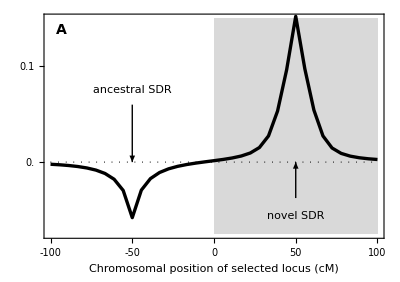

```mathematica
Clear[a]
positionplotA=
Show[

(*region of tighter linkage*)
RegionPlot[x>0,{x,xplotmin,xplotmax},{y,yplotmin,yplotmax},
PlotStyle->{LightGray},
BoundaryStyle->None,
PlotRange->{yplotmin,yplotmax},
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

(*neo-W into XY*)
ListPlot[Table[{a,invasionplotXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a,m],setR[x,a,m],setρ[x,a,m]]},{a,xplotmin,xplotmax,(xplotmax-xplotmin)/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

Plot[0,{x,xplotmin,xplotmax},PlotStyle->{Black, Dotted}],

PlotRange->{{xplotmin,xplotmax},{yplotmin,yplotmax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,-0.1,0.1,0.1}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Chromosomal position of selected locus (cM)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Rotate[Text[Style["Invasion fitness (λ-1)",14],Scaled@ylabpos],90 Degree],
(*Text[Style["tighter sex-linkage",14],{m,yplotmax*0.9}],*)
Text["ancestral SDR",{x,yplotmax*0.5}],
Text["novel SDR",{m,yplotmin*0.75}],
Arrow[{{x,yplotmax*0.4},{x,0}}],
Arrow[{{m,yplotmin*0.5},{m,0}}]
},
PlotRangeClipping->False
 ]
```

### Panel B - neo-W invasion fitness as function of selected locus location, with tighter linkage

#### Parameters

```mathematica
x=-5;
m=5;

tryt=0;
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.2;
tryMA=1+tryt;
tryMa=1;
tryFA=1;
tryFa=1;
tryMdA=0.5;
tryFdA=0.5;

xplotmin=-10;
xplotmax=10;
xplotinterval=5;
npoints=36;
```

#### Plot

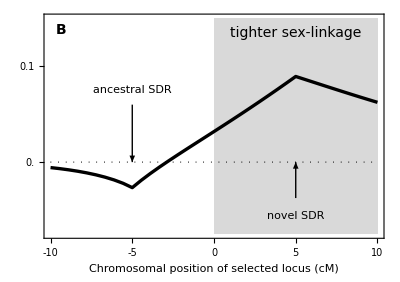

```mathematica
positionplotB=
Show[

(*region of tighter linkage*)
RegionPlot[x>0,{x,xplotmin,xplotmax},{y,yplotmin,yplotmax},
PlotStyle->{LightGray},
BoundaryStyle->None,
PlotRange->{yplotmin,yplotmax},
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

(*neo-W into XY*)
ListPlot[Table[{a,invasionplotXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,tryMA,tryMa,tryFA,tryFa,tryMdA,tryFdA,setr[x,a,m],setR[x,a,m],setρ[x,a,m]]},{a,xplotmin,xplotmax,(xplotmax-xplotmin)/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd]],
AxesOrigin->{xplotmin,yplotmin},
Frame->{True,True,False,False}
],

Plot[0,{x,xplotmin,xplotmax},PlotStyle->{Black, Dotted}],

PlotRange->{{xplotmin,xplotmax},{yplotmin,yplotmax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,-0.1,0.2,0.1}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Chromosomal position of selected locus (cM)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
Rotate[Text[Style[(*"Invasion fitness (λ-1)"*)"",14],Scaled@ylabpos],90 Degree],
Text[Style["tighter sex-linkage",14],{m,yplotmax*0.9}],
Text["ancestral SDR",{x,yplotmax*0.5}],
Text["novel SDR",{m,yplotmin*0.75}],
Arrow[{{x,yplotmax*0.4},{x,0}}],
Arrow[{{m,yplotmin*0.5},{m,0}}]
},
PlotRangeClipping->False

]
```

### Panel C - neo-W invasion fitness as function of recombination with selected locus, with inset of neo-W temporal dynamics

#### Parameters

```mathematica
tryFAA=1.05;
tryFAa=1;
tryFaa=0.85;
tryMAA=0.85;
tryMAa=1;
tryMaa=1.2;
trywAf=1;
trywaf=1;
trywAm=1;
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0.005;
tryR=0;
subpar1={FAA->tryFAA,FAa->tryFAa,Faa->tryFaa,MAA->tryMAA,MAa->tryMAa,Maa->tryMaa,wAf->trywAf,waf->trywaf,wAm->trywAm,wam->trywam,αf->tryαf,αm->tryαm};
```

```mathematica
modvec={0,0,1,1,0,0,1,1,0,0,0,0,0,0,0,0};
```

#### Plot of invasion fitness vs R

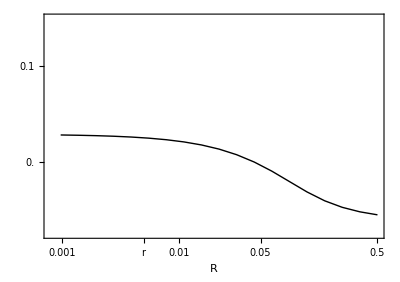

```mathematica
tab=Table[
equil=sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]];
λ/.Solve[(λ^2+(-(λmA1 +λma1)+(χmA1+χma1))λ +(λmA1-χmA1)( λma1-χma1)-χmA1 χma1/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.subpar1/.R->0.5^b/.{pXf->equil[[1]],pXm->equil[[2]],pYm->equil[[3]],q->equil[[4]]})==0,λ],{b,10,1,-1/2}];
eigen1=Transpose[Join[{Table[0.5^b,{b,10,1,-1/2}]},{Transpose[tab][[1]]-1}]];
eigen2=Transpose[Join[{Table[0.5^b,{b,10,1,-1/2}]},{Transpose[tab][[2]]-1}]];
plot1=Show[
ListLogLinearPlot[eigen2,Joined->True,PlotStyle->{Thick,Black},PlotRange->{{0.0008,0.5},{yplotmin,yplotmax}},
loglinearplotRλoptions]
]
```

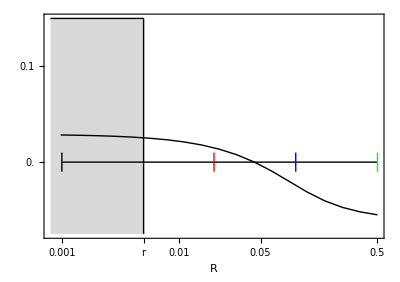

```mathematica
temp=Show[
ListLogLinearPlot[{{0.0008,yplotmax},{tryr,yplotmax}},Joined->True,PlotStyle->{Black,Thin},Filling->yplotmin,FillingStyle->LightGray,loglinearplotRλoptions,PlotRange->{{0.0008,0.5},{yplotmin,yplotmax}}],
plot1,
ListLogLinearPlot[{{tryr,yplotmax},{tryr,yplotmin}},Joined->True,PlotStyle->{Black,Thin}],
ListLogLinearPlot[{{0.001,0},{0.5,0}},Joined->True,PlotStyle->{Black}],
ListLogLinearPlot[{{0.001,-0.01},{0.001,0.01}},Joined->True,PlotStyle->{Black,Thick}],
ListLogLinearPlot[{{0.02,-0.01},{0.02,0.01}},Joined->True,PlotStyle->{Red}],
ListLogLinearPlot[{{0.1,-0.01},{0.1,0.01}},Joined->True,PlotStyle->{Blue}],
ListLogLinearPlot[{{0.5,-0.01},{0.5,0.01}},Joined->True,PlotStyle->{Green}],
GridLines->{{0.005},{1}}(*,
GridLinesStyle->Black*)]
```

#### Temporal invasion for 4 different R

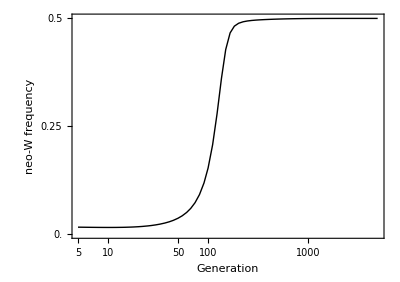

```mathematica
tryR=0.001;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Black=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Black=ListLogLinearPlot[MODtab1Black,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Black},loglinearplotINVoptions]
```

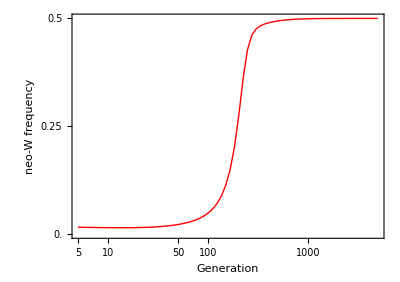

```mathematica
tryR=0.02;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Red=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Red=ListLogLinearPlot[MODtab1Red,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Red},loglinearplotINVoptions]
```

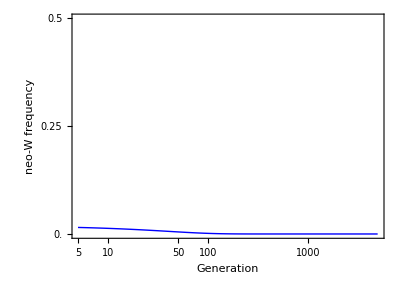

```mathematica
tryR=0.1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Blue=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Blue=ListLogLinearPlot[MODtab1Blue,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Blue},loglinearplotINVoptions]
```

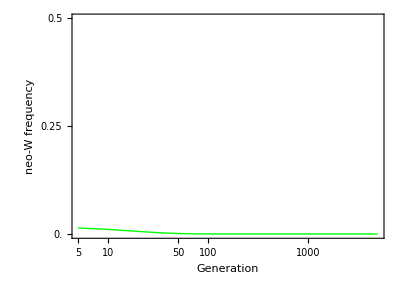

```mathematica
tryR=0.5;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr,tryR,tryr (1-tryR)+tryR (1-tryr),tryk};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
MODtab1Green=Table[{Round[Exp[exptime]],generation[param,run[Round[Exp[exptime]]]].modvec},{exptime,Log[startplot],Log[endtime],0.1}];
MOD1Green=ListLogLinearPlot[MODtab1Green,Joined->True,PlotRange->{{startplot,endtime},{0,0.5}},PlotStyle->{Green},loglinearplotINVoptions]
```

#### All together

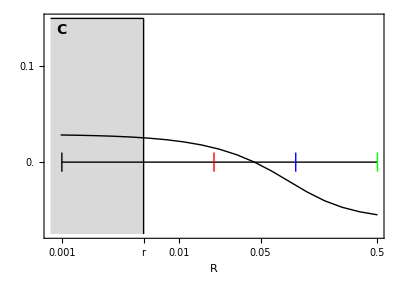

```mathematica
tempcomb=Show[temp,
(*Graphics[Text["R>r",{-4.55,-0.05},BaseStyle->{TextStyle->Bold,FontFamily->"Helvetica",FontSize->14}]],
Graphics[Text[Style["R<r",14],{-6.25,-0.05}]],*)
Graphics[Text[Style["C",14,Bold],Scaled@letpos]],
Epilog->Inset[Show[MOD1Black,MOD1Red,MOD1Blue,MOD1Green,(*ImageSize->150,*)BaseStyle->{TextStyle->Bold,FontFamily->"Helvetica",FontSize->6}],{-0,0.15},{Right,Top},{3.6,3.6*Sqrt[2]}]]
```

### All panels

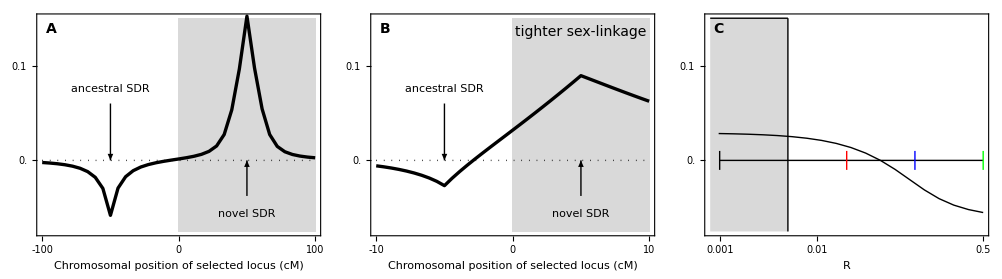

```mathematica
GraphicsRow[
{positionplotA,positionplotB,tempcomb},
Spacings->-30
]

Export[plotdir<>"PositionPlot_SexAntagTighter.pdf",%];
```

## Figure 2 - region plot of neo-W haplotype invasion with tight linkage and no haploid selection

### Panel A - A favoured in females

Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
Faa->0.85,
FAA->1.05
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WainvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

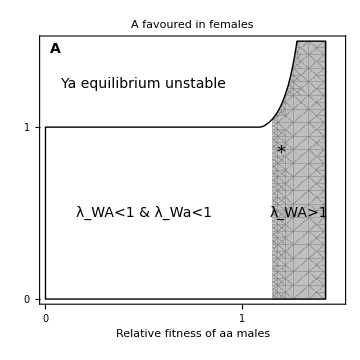

```mathematica
plotA=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@{0.05,0.95}],
Text[Style["λ_WA>1",14],{1.29,0.5}],
Text[Style["λ_WA<1 & λ_Wa<1",14],{0.5,0.5}],
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Text[Style["*",18],{1.2,0.85}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

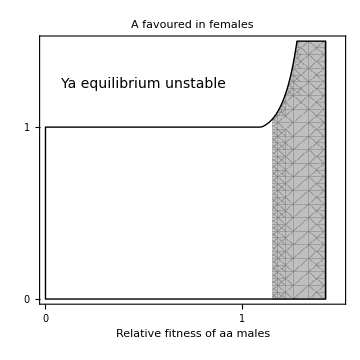

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]
},
PlotLabel->Style["A favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel B - a favoured in females

Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
Faa->1.05,
FAA->0.85
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyExt/.k->1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyExt/.k->1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WainvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

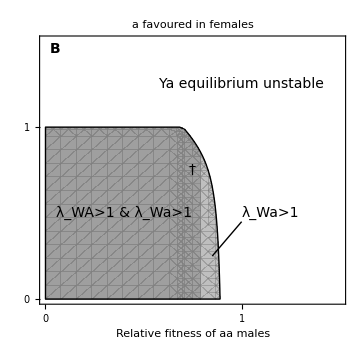

```mathematica
plotB=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

Graphics[{Thick,Black,Line[{{0.85,0.25},{1,0.45}}]}],
PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@{0.05,0.95}],
Text[Style["λ_Wa>1",14],{1,0.5},{-1,0}],
Text[Style["λ_WA>1 & λ_Wa>1",14],{0.4,0.5}],
Text[Style["Ya equilibrium unstable",14],{1,1.25}],
Text[Style["†",14],{0.75,0.75}]
(*,Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style["a favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

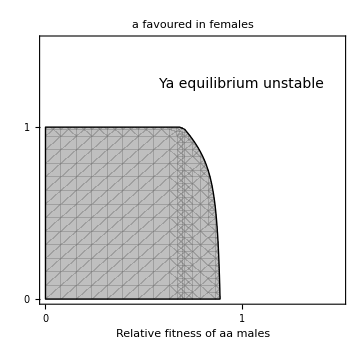

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{1,1.25}]
(*,Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style["a favoured in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### Panel C - overdominance in females

Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
Faa->0.6,
FAA->0.6
};
```

No recombination eigenvalues

```mathematica
WAinvA=λmA1/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WainvA=λma1/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilA0/.params//Simplify;
WAinvB=λmA1/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
WainvB=λma1/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilB0/.params//Simplify;
```

Maximum absolute no recombination eigenvalue from the full characteristic polynomial

```mathematica
λWsolA=Max[Abs[λ/.Solve[0==charpolyExt/.k->1/.r->0/.R->0/.ρ->0/.equilA0/.params,λ]//Simplify]];
λWsolB=Max[Abs[λ/.Solve[0==charpolyExt/.k->1/.r->0/.R->0/.ρ->0/.equilB0/.params,λ]//Simplify]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Region plots of invasion

```mathematica
(*neo-WA invades XY from equilA*)
plotWAinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<WAinvA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilA*)
plotWainvA=
RegionPlot[{
(validcondA/.params)&&
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&&
1<WainvA
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-WA invades XY from equilB*)
plotWAinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<WainvB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-Wa invades XY from equilB*)
plotWainvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&
1<WainvB
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*Ya equilibrium internally stable*)
plotYaStable=
RegionPlot[{
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)||
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->None,
BoundaryStyle->{Black,Thick}
];
```

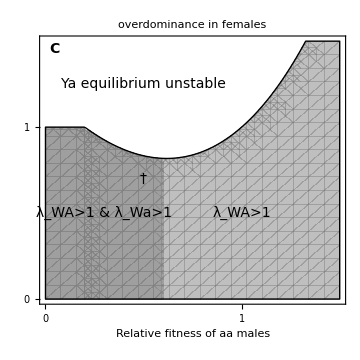

```mathematica
plotC=
Show[

plotWAinvA,
plotWainvA,
plotWAinvB,
plotWainvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["C",14,Bold],Scaled@{0.05,0.95}],
Text[Style["λ_WA>1",14],{1,0.5}],
Text[Style["λ_WA>1 & λ_Wa>1",14],{0.3,0.5}],
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}],
Text[Style["†",14],{0.5,0.7}]
(*,Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style["overdominance in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

Notice that this is consistent with the solution from the full characteristic polynomial (but here we don’t know which eigenvalue belongs to which haplotype)

```mathematica
(*neo-W invades XY from equilA*)
plotWinvA=
RegionPlot[{
(validcondA/.params)&& (*valid*)
(stabcondA/.Rf->0/.Rm->0/.equilA0/.params)&& (*internally stable*)
1<λWsolA (*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];

(*neo-W invades XY from equilB*)
plotWinvB=
RegionPlot[{
(stabcondB/.Rf->0/.Rm->0/.equilB0/.params)&&(*internally stable*)
1<λWsolB(*invasion*)
},
{Maa,0,3/2},{MAA,0,3/2},
PlotStyle->{Gray,Opacity[0.5]},
BoundaryStyle->None
];
```

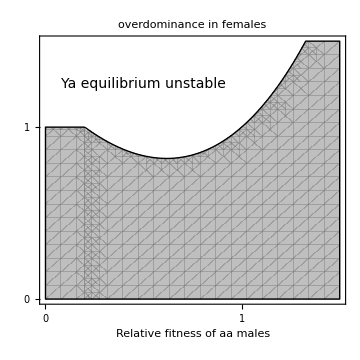

```mathematica
Show[

plotWinvA,
plotWinvB,
plotYaStable,

PlotRange->{{0,1.5},{0,1.5}},
ImageSize->{xsize,xsize},
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,0,1,1}],Table[{y,y,ticksize},{y,0,1,1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
FrameLabel->{"Relative fitness of aa males",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["Ya equilibrium unstable",14],{0.5,1.25}]
(*,Rotate[Text[Style["Relative fitness of AA males",14],Scaled@ylabpos],90 Degree]*)
},
PlotLabel->Style["overdominance in females", 16,Black,Bold],
PlotRangeClipping->False
]
```

### All panels

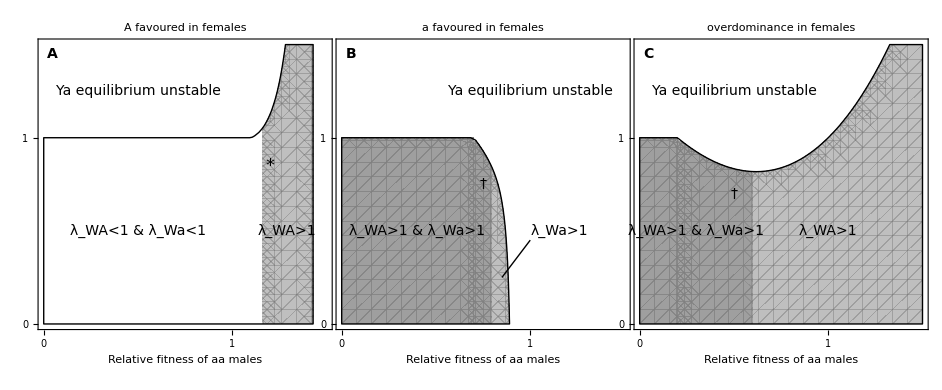

```mathematica
GraphicsRow[
{plotA,plotB,plotC},
Spacings->-50
]

Export[plotdir<>"Region_plot_combined.pdf",%//rasterTrick];
```

## Figure 3 - plot of neo-W invasion fitness as function of selected locus location, with haploid selection

### Plotting parameters

```mathematica
Pad={{40,20},{50,30}};  (*space around plot*)
xplotmin=-50;
xplotmax=50;
xplotinterval=25;
yplotmin=-0.04;
yplotmax=0.07;
yplotinterval=0.02;
npoints=20;
ylabpos={-0.1,0.5};  (*relative location of y axis label position*)
```

### Panel A - meiotic drive in males

#### Parameters

```mathematica
x=-25;
m=25;

trysAf=0.1;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.1;
tryt=0;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
trywAm=1+tryt;
trywam=1;
trywAf=1;
trywaf=1;
tryαm=0.45;
tryαf=0.5;
```

#### Plot

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

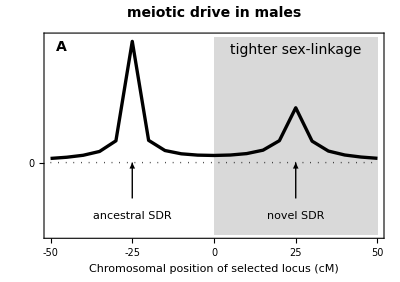

```mathematica
plotA=
Show[

(*region of tighter linkage*)
RegionPlot[x>0,{x,xplotmin,xplotmax},{y,yplotmin,yplotmax},
PlotStyle->{LightGray},
BoundaryStyle->None,
Frame->{True,True,False,False}
],

(*neo-W into XY*)
ListPlot[Table[{a,invasionplotXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAm,trywam,trywAf,trywaf,tryαm,tryαf,setr[x,a,m],setR[x,a,m],setρ[x,a,m]]},{a,xplotmin,xplotmax,(xplotmax-xplotmin)/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd]]
],

Plot[0,{x,xplotmin,xplotmax},PlotStyle->{Black, Dotted}],

PlotRange->{{xplotmin,xplotmax},{yplotmin,yplotmax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,0,0,0}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Chromosomal position of selected locus (cM)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["A",14,Bold],Scaled@letpos],
Rotate[Text[Style["Invasion fitness (λ-1)",14],Scaled@ylabpos],90 Degree],
Text[Style["tighter sex-linkage",14],{25,yplotmax*0.9}],
Text[Style["meiotic drive in males",14,Bold],(*{xplotmax,yplotmin*0.75}*)Scaled@{0.5,1.1},{0,0}],
Text["ancestral SDR",{-25,yplotmin*0.75}],
Text["novel SDR",{25,yplotmin*0.75}],
Arrow[{{-25,yplotmin*0.5},{-25,0}}],
Arrow[{{25,yplotmin*0.5},{25,0}}]
},
PlotRangeClipping->False

]
```

### Panel B - haploid competition in males

#### Parameters

```mathematica
x=-25;
m=25;

trysAf=0.05;
tryhAf=0.7;
tryhAm=0.7;
trysAm=0.15;
tryt=-0.1;
tryFAA=1+trysAf;
tryFAa=1+tryhAf trysAf;
tryFaa=1;
tryMAA=1+trysAm;
tryMAa=1+tryhAm trysAm;
tryMaa=1;
trywAm=1+tryt;
trywam=1;
trywAf=1;
trywaf=1;
tryαm=0.5;
tryαf=0.5;
```

#### Plot

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

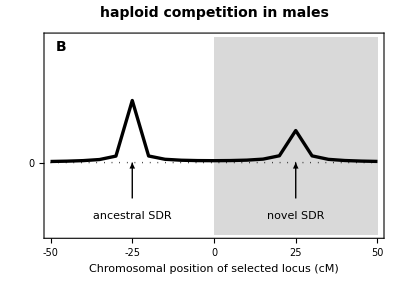

```mathematica
plotB=
Show[

(*region of tighter linkage*)
RegionPlot[x>0,{x,xplotmin,xplotmax},{y,yplotmin,yplotmax},
PlotStyle->{LightGray},
BoundaryStyle->None,
Frame->{True,True,False,False}
],

(*neo-W into XY*)
ListPlot[Table[{a,invasionplotXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAm,trywam,trywAf,trywaf,tryαm,tryαf,setr[x,a,m],setR[x,a,m],setρ[x,a,m]]},{a,xplotmin,xplotmax,(xplotmax-xplotmin)/npoints}],
Joined->True,
PlotRange->{yplotmin,All},
PlotStyle->Directive[Black,Thickness[lwd]]
],

Plot[0,{x,xplotmin,xplotmax},PlotStyle->{Black, Dotted}],

PlotRange->{{xplotmin,xplotmax},{yplotmin,yplotmax}},
ImageSize->{xsize,xsize aspectratio },
AspectRatio->aspectratio,
PlotRangePadding->0,
FrameTicks->{Table[{x,x,ticksize},{x,xplotmin,xplotmax,xplotinterval}],Table[{y,y,ticksize},{y,0,0,0}]},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},None,None},
FrameLabel->{"Chromosomal position of selected locus (cM)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14},
ImagePadding->Pad,
Epilog->{
Text[Style["B",14,Bold],Scaled@letpos],
(*Rotate[Text[Style["Invasion fitness (λ-1)",14],Scaled@ylabpos],90 Degree],*)
Text[Style["haploid competition in males",14,Bold],(*{xplotmax,yplotmin*0.75}*)Scaled@{0.5,1.1},{0,0}],
Text["ancestral SDR",{-25,yplotmin*0.75}],
Text["novel SDR",{25,yplotmin*0.75}],
Arrow[{{-25,yplotmin*0.5},{-25,0}}],
Arrow[{{25,yplotmin*0.5},{25,0}}]
},
PlotRangeClipping->False

]
```

### All panels

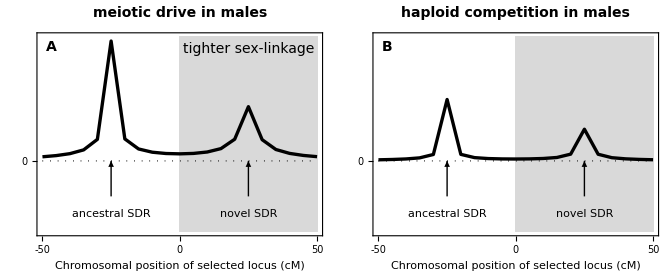

```mathematica
GraphicsRow[
{plotA,plotB},
Spacings->-30
]

Export[plotdir<>"PositionPlot.pdf",%];
```

## Figure 4

## Figure S.1

## Figure S.2

## Figure S.3

## Figure S.4

## Figure S.5

## Figure S.6

## Figure S.7

## Figure S.8

## Figure S.9

## Figure S.10

### Ploidally-antagonistic

Parameters

```mathematica
params={
wAm->0.76,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
Faa->0.9,FAA->1.1,
Maa->0.9,MAA->1.1
};
```

Eigenvalues from the quadratic of interest (of the characteristic polynomial) for both polymorphic ancestral equilibria

```mathematica
WinvA=λ/.Solve[0==λ^2+(-(λmA1+λma1)+(χmA1+χma1))λ+((λmA1-χmA1)(λma1-χma1)-χmA1 χma1)/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilA0/.params,λ];
WinvB=λ/.Solve[0==λ^2+(-(λmA1+λma1)+(χmA1+χma1))λ+((λmA1-χmA1)(λma1-χma1)-χmA1 χma1)/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilB0/.params,λ];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Plots of invasion fitness for haplotype WA vs recombination

```mathematica
plot1A=ListPlot[Table[{R,WinvA[[2]]-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->{Thick,Black},PlotRange->All,Axes->False];
plot1B=ListPlot[Table[{R,WinvB[[2]]-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->{Thick,Black},PlotRange->All,Axes->False];
```

Max in absolute value eigenvalue from the full characteristic polynomial

```mathematica
WinvAfull=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.ρ->0/.equilA0/.params,λ]]];
WinvBfull=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.ρ->0/.equilB0/.params,λ]]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

Plots of invasion fitness for the most favoured neo-W haplotype vs recombination

```mathematica
plot2=Show[
ListPlot[Table[{R,WinvAfull-1},{R,0,1/2,0.01}],Joined->True,PlotRange->All,PlotStyle->Red],
ListPlot[Table[{R,WinvBfull-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->Red],
PlotRange->All
];
```

Compare with the quadratic of interest results to ensure they are in agreement

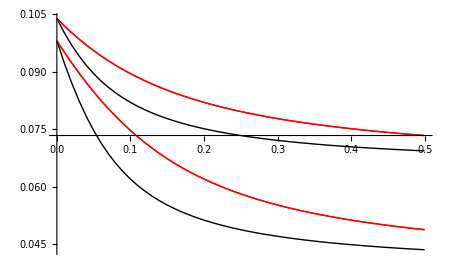

```mathematica
Show[plot2,plot1A,plot1B,plot2]
```

```mathematica
tryFAA=1.1;
tryFAa=1;
tryFaa=0.9;
tryMAA=1.1;
tryMAa=1;
tryMaa=0.9;
trywAf=1;
trywaf=1;
trywAm=0.76;(* Neo-W can invade if 0.7499999999999999 < wAm < 0.826483809980763 *)
trywam=1;
tryαf=0.5;
tryαm=0.5;
tryr=0;
tryR=0.5;
startplot=5;
endtime=500000;
trypm=0.01;
tryk=1;
param={tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr};
run[0]=generation[param,startgen[sieveXY[tryFAA,tryFAa,tryFaa,tryMAA,tryMAa,tryMaa,trywAf,trywaf,trywAm,trywam,tryαf,tryαm,tryr][[1]],trypm]];
For[time=1,time≤endtime,time++,run[time]=generation[param,run[time-1]]
]
```

### Overdominance in males, no haploid selection

Parameters

```mathematica
params={
wAm->1,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
Faa->1.1,FAA->0.99,
Maa->0.8,MAA->0.8
};
```

Eigenvalues from the quadratic of interest (of the characteristic polynomial)

```mathematica
WinvA=λ/.Solve[0==λ^2+(-(λmA1+λma1)+(χmA1+χma1))λ+((λmA1-χmA1)(λma1-χma1)-χmA1 χma1)/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilA0/.params,λ];
WinvB=λ/.Solve[0==λ^2+(-(λmA1+λma1)+(χmA1+χma1))λ+((λmA1-χmA1)(λma1-χma1)-χmA1 χma1)/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilB0/.params,λ];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
plot2A=ListPlot[Table[{R,WinvA[[2]]-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->{Thick,Black,Dashing[Large]},PlotRange->All,Axes->False];
```

```mathematica
plot2B=ListPlot[Table[{R,WinvB[[2]]-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->{Thick,Black,Dashing[Large]},PlotRange->All,Axes->False];
```

Max in absolute value eigenvalue from the full characteristic polynomial

```mathematica
WinvAfull=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.ρ->0/.equilA0/.params,λ]]];
WinvBfull=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.ρ->0/.equilB0/.params,λ]]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
plot2=Show[
ListPlot[Table[{R,WinvAfull-1},{R,0,1/2,0.01}],Joined->True,PlotRange->All,PlotStyle->Red],
ListPlot[Table[{R,WinvBfull-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->Red],
PlotRange->All
];
```

Compare with the quadratic of interest results

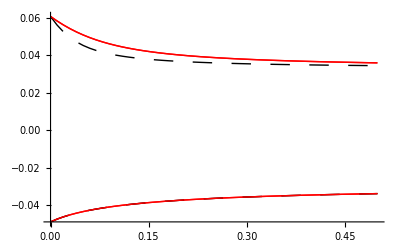

```mathematica
Show[plot2,plot2A,plot2B,plot2,PlotRange->All]
```

### Sexual antagonism with haploid competition in males

Parameters

```mathematica
params={
wAm->0.85,wam->1,wAf->1,waf->1,
αm->1/2,αf->1/2,
MAa->1,FAa->1,
Faa->0.98,FAA->1.1,
Maa->1.01,MAA->0.8
};
```

Eigenvalues from the quadratic of interest (of the characteristic polynomial)

```mathematica
WinvA=λ/.Solve[0==λ^2+(-(λmA1+λma1)+(χmA1+χma1))λ+((λmA1-χmA1)(λma1-χma1)-χmA1 χma1)/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilA0/.params,λ];
WinvB=λ/.Solve[0==λ^2+(-(λmA1+λma1)+(χmA1+χma1))λ+((λmA1-χmA1)(λma1-χma1)-χmA1 χma1)/.meanF->femaleMeanFit/.pAveM->(1-q)pXm+q pYm/.equilB0/.params,λ];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
plot3A=ListPlot[Table[{R,WinvA[[2]]-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->{Thick,Black,Dotted},PlotRange->All,Axes->False];
```

```mathematica
plot3B=ListPlot[Table[{R,WinvB[[2]]-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->{Thick,Black,Dotted},PlotRange->All,Axes->False];
```

Max in absolute value eigenvalue from the full characteristic polynomial

```mathematica
WinvAfull=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.ρ->0/.equilA0/.params,λ]]];
WinvBfull=Max[Abs[λ/.Solve[0==charpolyk1/.r->0/.ρ->0/.equilB0/.params,λ]]];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
plot2=Show[
ListPlot[Table[{R,WinvAfull-1},{R,0,1/2,0.01}],Joined->True,PlotRange->All,PlotStyle->Red],
ListPlot[Table[{R,WinvBfull-1},{R,0,1/2,0.01}],Joined->True,PlotStyle->Red],
PlotRange->All
];
```

Compare with the quadratic of interest results

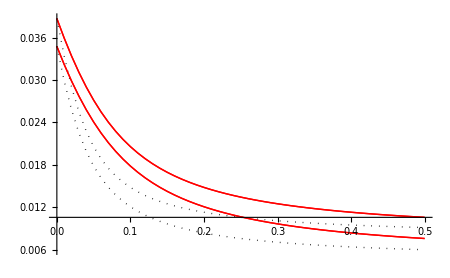

```mathematica
Show[plot2,plot3A,plot3B,plot2,PlotRange->All]
```

### All

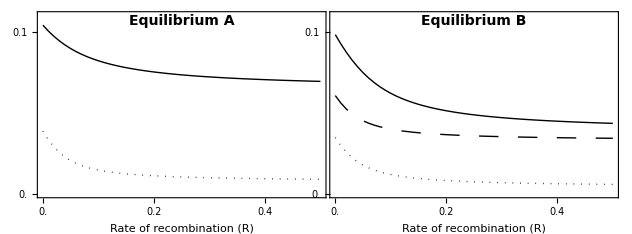

```mathematica
GraphicsRow[{

Show[

plot1A,(*plot2A,*)plot3A,

PlotRange->{{0,0.5},{0,0.11}},
Frame->{True,True,False,False},
FrameTicks->{Table[{x,x,ticksize},{x,0,1/2,0.1}],Table[{y,y,ticksize},{y,0,0.1,0.1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
Epilog->{
Rotate[Text[Style["Invasion fitness (λ_WA-1)",14],Scaled@{-0.15,0.5}],90 Degree],
Text[Style["Equilibrium A",14,Bold],Scaled@{0.5,0.95}]
},
PlotRangeClipping->False,
ImageSize->xsize,
ImagePadding->{{50,20},{50,20}},
FrameLabel->{"Rate of recombination (R)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14}
],

Legended[
Show[

plot1B,plot2B,plot3B,

PlotRange->{{0,0.5},{0,0.11}},
Frame->{True,True,False,False},
FrameTicks->{Table[{x,x,ticksize},{x,0,1/2,0.1}],Table[{y,y,ticksize},{y,0,0.1,0.1}],None,None},
FrameTicksStyle->{{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd]]},{Directive[Black,Thickness[lwd]],Directive[Black,Thickness[lwd],FontColor->White]}},
FrameStyle->{{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]},{Black,Thickness[lwd]}},
Epilog->{
Text[Style["Equilibrium B",14,Bold],Scaled@{0.5,0.95}]
},
ImageSize->xsize,
ImagePadding->{{30,20},{50,20}},
FrameLabel->{"Rate of recombination (R)",""},
BaseStyle->{FontFamily->"Helvetica",FontSize->14}
],
Placed[

]
]
},

Spacings->{-50,0}
]
```